```mathematica
Needs["HypExp`"]
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, mm2___List, x_] is Protected.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1___List, mm2 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$Assumptions=0<y<1&&0<z<1&&eps>0&&0<M<Q&&0<eps<1&&delta>0
```

0<y<1∧0<z<1∧ϵ>0∧0<M<Q∧0<ϵ<1∧δ>0

```mathematica
levi5[a_,b_,c_]:=Module[{ind},LC[a,b,c,ind]GAD[ind].GAD[5]]

cleanIndices[e_,var1_,var2_]:=e/.LC[a_,rho,sigma,b_]:> LC[a,b,rho,sigma]/.f_*LC[a_,b_,rho,sigma]:> (f/.a:>var1/.b:>var2)*LC[var1,var2,rho,sigma]/.f_*Eps[LorentzIndex[a_],LorentzIndex[b_],LorentzIndex[rho],LorentzIndex[sigma]]:>  (f/.a:>var1/.b->var2)*Eps[var1,var2,rho,sigma]
```

### Integral Definitions

```mathematica
(* three propagators, no numerator *)
L0QCDEuclidean[igrand_,deltaSqr_,dim_]:=(Gamma[(6-dim)/2]/((4*Pi)^(dim/2)) )*Inactive[integrateAndEpsSeriesTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-6)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]

(* three propagators, l^2 in numerator *)
L2QCDEuclidean[igrand_,deltaSqr_,dim_]:=(D*Gamma[(4-dim)/2]/(2(4*Pi)^(dim/2)) )*Inactive[integrateAndEpsSeriesTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-4)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]

waveZ=alphabar*(1/eps-1/2-LM)/2
```

1/2 ᾱ (-LM+1/ϵ-1/2)

### QCD Loop Graphs for 1⊗1

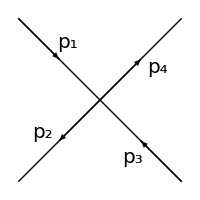

```mathematica
(* reproducting fig 5 of arXiv:0806.1240v2, rotated so time runs left to right*)
Graphics[{ Arrowheads[0.05],  (* --- *) Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}] ,Arrow[{{0,0},{0.5,0.5}}] ,Arrow[{{0,0},{-0.5,-0.5}}],Arrow[{{-1,1},{-0.5,0.5}}],Arrow[{{1,-1},{0.5,-0.5}}],
Text[Style[p4,20],{0.7,0.4}],Text[Style[p2,20],{-0.7,-0.4}],Text[Style[p1,20],{-0.4,0.7}],Text[Style[p3,20],{0.4,-0.7}](* --- *)    },ImageSize->200]
```

#### Graph 12

```mathematica
(* here we direct the loop momentum from 1 to 2 *)
```

```mathematica
amplitude12prefac=-I*(TensorProduct["1","1"])*g^2
amplitude12Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k-p2,k-p2])
amplitude12DiracStructure=SpinorUBar[p4].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[mu].GAD[rho].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k-p2,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime12=k+y*p1-z*p2;
amplitude12DiracStructureShifted=amplitude12DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime12),a]
amplitude12DiracStructureZero=SeriesCoefficient[amplitude12DiracStructureShifted,{lambda,0,0}]
amplitude12DiracStructureTwo=SeriesCoefficient[amplitude12DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 1⊗1

(k^2-M^2) (2 k·p_1+k^2) (k^2-2 k·p_2)

(k^rhoo-p_2^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo+z p_2^rhoo-p_2^rhoo) (λ l^sigmaa-y p_1^sigmaa+z p_2^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo+z p_2^rhoo-p_2^rhoo) (-y p_1^sigmaa+z p_2^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude12DiracStructureZero/.sigmaa->sigma/.rhoo->rho//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
zeroth12Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
%/(2SPD[p1,p2]*M0)//Expand
```

-1/4 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 y^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 y φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 y φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 y z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)-1/4 y z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 z^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)+1/4 z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)

-1/2 D y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/2 D y z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+1/2 D y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/2 D y z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

-2 D y z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)-4 p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

-2 D y z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)-4 p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

2 M0 p_1·p_2 (y (2-(D-2) z)+2 (z-1))

-D y z+2 y z+2 y+2 z-2

```mathematica
(amplitude12DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic12Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

(l^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^α.γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1))/(4 D)

1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3))/D-1/4 D l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-(l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1))/D-1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D+1/4 D l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+(l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D-l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

D l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+(4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3))/D-4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

D l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+(4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3))/D-4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

((D-2)^2 l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

zeroth12Term;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p2].PhatL->PhatR.GSD[p2]//Simplify;
rah12=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p2]->GSD[p2].PhatL

L0QCDEuclidean[rah12,x*M^2+SPD[kprime12-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p1,p2]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero12=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];

Series[preAnswerZero12,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude12prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero12=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero12//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.Ls->Lis-I*Pi/.alphaMS->alphabar*2*Pi//Expand
simpZero12=%//Expand
```

2 M0 p_1·p_2 (y (2-(D-2) z)+2 (z-1))

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateTermByTerm[M0 Q^2 (M^2 (-y-z+1)-Q^2 y z)^(1/2 (-2 ϵ-2)) (2 (z-1)+y (2-(D-2) z))z01-y,{y,0,1}]

(4 π)^(-ϵ-2) 1-ϵ integrateTermByTerm[(M0 Q^2 (y-1) M^(-2 ϵ) (1-y)^ϵ (M Q)^(2 ϵ) (M^(2 ϵ) Q^(-2 ϵ) (M^2 ((D-2) y+2 ϵ)+2 Q^2 y (ϵ+1))-ⅇ^(ⅈ π ϵ) y^(ϵ+1) ((D-2) M^2 (ϵ+1)+Q^2 ((D-2) y ϵ+2))))/(ϵ (ϵ+1) (M^2+Q^2 y)^2),{y,0,1}]

Integrating (D ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1) M^(2-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(2 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1) M^(2-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(D ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(2-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))+(2 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(2-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))+(D ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1) M^(2-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))-(2 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1) M^(2-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))-(D ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(2-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))+(2 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(2-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))+(2 ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1) M^(-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(2 ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(-2 ϵ))/((M^2+Q^2 y)^2 ϵ (ϵ+1))+(D ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))-(2 ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2) M^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))-(D ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+3) M^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))+(2 ⅇ^(ⅈ π ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+3) M^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ+1))+(D M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2 M^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2 M^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(D M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y M^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))+(2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y M^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ M^2)/((M^2+Q^2 y)^2 (ϵ+1))+(2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y M^2)/((M^2+Q^2 y)^2 (ϵ+1))+(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 ϵ (ϵ+1))+(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 (ϵ+1))-(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 (ϵ+1))

Integrating 24 terms.

Term 1 : -(2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ)/((M^2+Q^2 y)^2 (ϵ+1))

1 : (2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (ϵ ϵ+1 11ϵ+2-Q^2/M^2-1))/((M^2+Q^2) (ϵ+1))

Term 2 : (2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 (ϵ+1))

2 : (2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) ((((ϵ+1) M^2+Q^2) ϵ+2 11ϵ+3-Q^2/M^2)/M^2+1/(ϵ+1)-1))/((M^2+Q^2)^2 (ϵ+1))

Term 3 : -(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 (ϵ+1))

3 : -(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) ((((ϵ+1) M^2+Q^2) ϵ+2 11ϵ+3-Q^2/M^2)/M^2+1/(ϵ+1)-1))/((M^2+Q^2)^2 (ϵ+1))

Term 4 : (2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 (ϵ+1))

4 : (2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (-(2 M^2)/(ϵ+2)+M^2-((ϵ+2) M^2+2 Q^2) ϵ+3 11ϵ+4-Q^2/M^2+(M^2+Q^2)/(ϵ+1)))/((M^2+Q^2)^3 (ϵ+1))

Term 5 : -(2 ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1))/((M^2+Q^2 y)^2 (ϵ+1))

5 : (2^(-2 ϵ-1) ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 √π Q^2 (M Q)^(2 ϵ) ϵ+1 (((2 ϵ+1) M^2+Q^2 (ϵ+1)) 1ϵ+22 ϵ+3-Q^2/M^2-2 M^2 (ϵ+1)))/((M^2+Q^2) (ϵ+1) ϵ+3/2)

Term 6 : (D ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1))/((M^2+Q^2 y)^2 (ϵ+1))

6 : (4^(-ϵ-1) D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 √π Q^2 (M Q)^(2 ϵ) ϵ+1 (2 M^2 (ϵ+1)-((2 ϵ+1) M^2+Q^2 (ϵ+1)) 1ϵ+22 ϵ+3-Q^2/M^2))/((M^2+Q^2) (ϵ+1) ϵ+3/2)

Term 7 : (2 ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 (ϵ+1))

7 : (2 ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 Q^2 (M Q)^(2 ϵ) ϵ+1 ϵ+3 (M^2 (2 ϵ+3)-(2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2))/((M^2+Q^2) (ϵ+1) 2 ϵ+4)

Term 8 : -(D ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 (ϵ+1))

8 : (D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 Q^2 (M Q)^(2 ϵ) ϵ+1 ϵ+3 ((2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2-M^2 (2 ϵ+3)))/((M^2+Q^2) (ϵ+1) 2 ϵ+4)

Term 9 : -(2 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 (ϵ+1))

9 : (2 ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 Q^4 (M Q)^(2 ϵ) ϵ+1 ϵ+3 ((2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2-M^2 (2 ϵ+3)))/((M^2+Q^2) (ϵ+1) 2 ϵ+4)

Term 10 : (D ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 (ϵ+1))

10 : (D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 Q^4 (M Q)^(2 ϵ) ϵ+1 ϵ+3 (M^2 (2 ϵ+3)-(2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2))/((M^2+Q^2) (ϵ+1) 2 ϵ+4)

Term 11 : (2 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+3))/((M^2+Q^2 y)^2 (ϵ+1))

11 : (2 ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 Q^4 (M Q)^(2 ϵ) ϵ+1 ϵ+4 (2 M^2 (ϵ+2)-((2 ϵ+3) M^2+Q^2 (ϵ+3)) 1ϵ+42 ϵ+5-Q^2/M^2))/((M^2+Q^2) (ϵ+1) 2 ϵ+5)

Term 12 : -(D ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+3))/((M^2+Q^2 y)^2 (ϵ+1))

12 : (D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 Q^4 (M Q)^(2 ϵ) ϵ+1 ϵ+4 (((2 ϵ+3) M^2+Q^2 (ϵ+3)) 1ϵ+42 ϵ+5-Q^2/M^2-2 M^2 (ϵ+2)))/((M^2+Q^2) (ϵ+1) 2 ϵ+5)

Term 13 : (2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

13 : (2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (((ϵ+1) M^2+Q^2) ϵ 11ϵ+3-Q^2/M^2-M^2/(ϵ+1)^2))/((M^2+Q^2)^2)

Term 14 : -(D M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

14 : (D M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (M^2/(ϵ+1)^2-((ϵ+1) M^2+Q^2) ϵ 11ϵ+3-Q^2/M^2))/((M^2+Q^2)^2)

Term 15 : -(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

15 : -(2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) ((((ϵ+1) M^2+Q^2) ϵ+2 11ϵ+3-Q^2/M^2)/M^2+1/(ϵ+1)-1))/((M^2+Q^2)^2 ϵ (ϵ+1))

Term 16 : -(2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

16 : -(2 M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (-(2 M^2)/(ϵ+2)+M^2-((ϵ+2) M^2+2 Q^2) ϵ+3 11ϵ+4-Q^2/M^2+(M^2+Q^2)/(ϵ+1)))/((M^2+Q^2)^3 ϵ (ϵ+1))

Term 17 : (D M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

17 : (D M^2 M0 Q^(2-2 ϵ) (M Q)^(2 ϵ) (-(2 M^2)/(ϵ+2)+M^2-((ϵ+2) M^2+2 Q^2) ϵ+3 11ϵ+4-Q^2/M^2+(M^2+Q^2)/(ϵ+1)))/((M^2+Q^2)^3 ϵ (ϵ+1))

Term 18 : (2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (1-y)^ϵ y^2)/((M^2+Q^2 y)^2 ϵ (ϵ+1))

18 : (2 M0 Q^(4-2 ϵ) (M Q)^(2 ϵ) (-(2 M^2)/(ϵ+2)+M^2-((ϵ+2) M^2+2 Q^2) ϵ+3 11ϵ+4-Q^2/M^2+(M^2+Q^2)/(ϵ+1)))/((M^2+Q^2)^3 ϵ (ϵ+1))

Term 19 : -(2 ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

19 : (2^(-2 ϵ-1) ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 √π Q^2 (M Q)^(2 ϵ) ϵ+1 (((2 ϵ+1) M^2+Q^2 (ϵ+1)) 1ϵ+22 ϵ+3-Q^2/M^2-2 M^2 (ϵ+1)))/((M^2+Q^2) ϵ (ϵ+1) ϵ+3/2)

Term 20 : (D ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

20 : (4^(-ϵ-1) D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 √π Q^2 (M Q)^(2 ϵ) ϵ+1 (2 M^2 (ϵ+1)-((2 ϵ+1) M^2+Q^2 (ϵ+1)) 1ϵ+22 ϵ+3-Q^2/M^2))/((M^2+Q^2) ϵ (ϵ+1) ϵ+3/2)

Term 21 : (2 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+1))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

21 : (2^(-2 ϵ-1) ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 √π Q^4 (M Q)^(2 ϵ) ϵ+1 (2 M^2 (ϵ+1)-((2 ϵ+1) M^2+Q^2 (ϵ+1)) 1ϵ+22 ϵ+3-Q^2/M^2))/((M^2+Q^2) ϵ (ϵ+1) ϵ+3/2)

Term 22 : (2 ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

22 : (2 ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 Q^2 (M Q)^(2 ϵ) ϵ+1 ϵ+3 (M^2 (2 ϵ+3)-(2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2))/((M^2+Q^2) ϵ (ϵ+1) 2 ϵ+4)

Term 23 : -(D ⅇ^(ⅈ π ϵ) M^(2-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

23 : (D ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+1)) M0 Q^2 (M Q)^(2 ϵ) ϵ+1 ϵ+3 ((2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2-M^2 (2 ϵ+3)))/((M^2+Q^2) ϵ (ϵ+1) 2 ϵ+4)

Term 24 : -(2 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^4 (M Q)^(2 ϵ) (1-y)^ϵ y^(ϵ+2))/((M^2+Q^2 y)^2 ϵ (ϵ+1))

24 : (2 ⅇ^(ⅈ π ϵ) M^(-2 (ϵ+2)) M0 Q^4 (M Q)^(2 ϵ) ϵ+1 ϵ+3 ((2 (ϵ+1) M^2+Q^2 (ϵ+2)) 1ϵ+32 (ϵ+2)-Q^2/M^2-M^2 (2 ϵ+3)))/((M^2+Q^2) ϵ (ϵ+1) 2 ϵ+4)

$Aborted

$Aborted

$Aborted

«3 more identical outputs»

```mathematica
(* integrating the zeroth order term *)

quadratic12Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p2].PhatL->PhatR.GSD[p2]//Simplify;
rahrah12=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p2]->GSD[p2].PhatL

L2QCDEuclidean[rahrah12,x*M^2+SPD[kprime12-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p1,p2]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad12=Activate[%,integrateAndEps0SeriesTermByTerm];

Series[preAnswerQuad12//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude12prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad12=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad12//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad12=%/.Ls->Lis-I*Pi//Expand
```

((D-2)^2 M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateTermByTerm[((D-2)^2 M0 (M^2 (-y-z+1)-Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(-2 ϵ-5) π^(-ϵ-2) -ϵ integrateTermByTerm[((D-2)^2 M0 M^(-2 ϵ) Q^(-2 ϵ) (1-y)^(ϵ+1) (M Q)^(2 ϵ) (M^(2 ϵ+2)+ⅇ^(ⅈ π ϵ) Q^(2 ϵ+2) y^(ϵ+1)))/(D (ϵ+1) (M^2+Q^2 y)),{y,0,1}]

Integrating (D ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1) M^(-2 ϵ))/((M^2+Q^2 y) (ϵ+1))+(4 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1) M^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ+1))-(4 ⅇ^(ⅈ π ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1) M^(-2 ϵ))/((M^2+Q^2 y) (ϵ+1))+(D M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1) M^2)/((M^2+Q^2 y) (ϵ+1))+(4 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1) M^2)/(D (M^2+Q^2 y) (ϵ+1))-(4 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1) M^2)/((M^2+Q^2 y) (ϵ+1))

Integrating 6 terms.

Term 1 : -(4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1))/((M^2+Q^2 y) (ϵ+1))

1 : -4 M^(2 ϵ) M0 ϵ+1 11ϵ+3-Q^2/M^2

Term 2 : (4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1))/(D (M^2+Q^2 y) (ϵ+1))

2 : (4 M^(2 ϵ) M0 ϵ+1 11ϵ+3-Q^2/M^2)/D

Term 3 : (D M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (1-y)^(ϵ+1))/((M^2+Q^2 y) (ϵ+1))

3 : D M^(2 ϵ) M0 ϵ+1 11ϵ+3-Q^2/M^2

Term 4 : -(4 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1))/((M^2+Q^2 y) (ϵ+1))

4 : -(4 ⅇ^(ⅈ π ϵ) M0 Q^(2 ϵ+2) (ϵ+2)^2 1ϵ+22 (ϵ+2)-Q^2/M^2)/(M^2 (ϵ+1))

Term 5 : (4 ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1))/(D (M^2+Q^2 y) (ϵ+1))

5 : (4 ⅇ^(ⅈ π ϵ) M0 Q^(2 ϵ+2) (ϵ+2)^2 1ϵ+22 (ϵ+2)-Q^2/M^2)/(D M^2 (ϵ+1))

Term 6 : (D ⅇ^(ⅈ π ϵ) M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (1-y)^(ϵ+1) y^(ϵ+1))/((M^2+Q^2 y) (ϵ+1))

6 : (D ⅇ^(ⅈ π ϵ) M0 Q^(2 ϵ+2) (ϵ+2)^2 1ϵ+22 (ϵ+2)-Q^2/M^2)/(M^2 (ϵ+1))

((D-2)^2 M0 2^(2 ϵ-5) ⅇ^(-ⅈ π ϵ) π^(ϵ-2) M^(2 ϵ) (2-ϵ)^2 ϵ (M Q)^(-2 ϵ))/((ϵ-1)^2 3-2 ϵ)

(M0 1⊗1 α_OverBar[MS])/(4 π ϵ)+(2 M0 1⊗1 log(M) α_OverBar[MS]-2 M0 1⊗1 α_OverBar[MS] log(M Q)+M0 1⊗1 α_OverBar[MS]-ⅈ π M0 1⊗1 α_OverBar[MS]+M0 1⊗1 α_OverBar[MS] log(μ_OverBar[MS]^2))/(4 π)

(M0 1⊗1 α_OverBar[MS])/(4 π ϵ)-1/4 ⅈ M0 1⊗1 α_OverBar[MS]+(M0 1⊗1 α_OverBar[MS])/(4 π)-(M0 1⊗1 α_OverBar[MS] log(Q))/(2 π)+(M0 1⊗1 α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 Ls M0 ᾱ 1⊗1+(M0 ᾱ 1⊗1)/(2 ϵ)+1/2 M0 ᾱ 1⊗1-1/2 ⅈ π M0 ᾱ 1⊗1

-1/2 Lis M0 ᾱ 1⊗1+(M0 ᾱ 1⊗1)/(2 ϵ)+1/2 M0 ᾱ 1⊗1

#### Graph 13

```mathematica
(* here we direct the loop momentum from 3 to 1 *)
```

```mathematica
amplitude13prefac=-g^2
amplitude13Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k+p3,k+p3])
amplitude13DiracStructure=SpinorUBar[p4].GAD[tau].PhatL.GAD[rho].GAD[mu].SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p3,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime13=k+y*p1+z*p3;
amplitude13DiracStructureShifted=amplitude13DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime13),a]
amplitude13DiracStructureZero=SeriesCoefficient[amplitude13DiracStructureShifted,{lambda,0,0}]
amplitude13DiracStructureTwo=SeriesCoefficient[amplitude13DiracStructureShifted,{lambda,0,2}]
```

-g^2

(k^2-M^2) (2 k·p_1+k^2) (2 k·p_3+k^2)

(k^rhoo+p_3^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo-z p_3^rhoo+p_3^rhoo) (λ l^sigmaa-y p_1^sigmaa-z p_3^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo-z p_3^rhoo+p_3^rhoo) (-y p_1^sigmaa-z p_3^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude13DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE;
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu];  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE;

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE;
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL;
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand;
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p3].PhatL->PhatR.GSD[p3]//DiracSimplify//FCE
(* use spinor helicity to derive fact that Ubar4.GSD[p1].V3 Vbar2.GSD[3].U1 = -SPD{p1,p4] M0 *)
zeroth13Term=%/.Spinor[Momentum[p2],___].PhatR.GSD[p3].Spinor[Momentum[p1],___]Spinor[Momentum[p4],___].PhatR.GSD[p1].Spinor[Momentum[p3],___]->-SPD[p1,p4]*M0
```

1/4 p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_3^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

(D-4) (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D-4) y z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D-4) (y-1) (z-1) φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+(D-4) (z-1) z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

(D-4) y z φ(p_2).(P̂)_R.(γ·p_3).φ(p_1) φ(p_4).(P̂)_R.(γ·p_1).φ(p_3)+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

```mathematica
(amplitude13DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

(* need to put feyncalc-simplified amplitude back in left-chiral basis *)
%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL

quadratic13Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^τ.γ^α.γ^μ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10674.γ^5 ϵ^ταμind$10674).φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10675.γ^5 ϵ^ταμind$10675).φ(p_3))/(4 D)-(l^2 φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10676.γ^5 ϵ^ταμind$10676).φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10677.γ^5 ϵ^ταμind$10677).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10678.γ^5 ϵ^ταμind$10678).φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10679.γ^5 ϵ^ταμind$10679).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10680.γ^5 ϵ^ταμind$10680).γ^5.φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$10681.γ^5 ϵ^ταμind$10681).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_2).γ^ind$10675.γ^5.φ(p_1) φ(p_4).γ^ind$10675.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$10676.φ(p_1) φ(p_4).γ^ind$10676.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$10678.φ(p_3) φ(p_2).γ^ind$10678.γ^5.φ(p_1))/(2 D)+(3 l^2 φ(p_2).γ^ind$10681.φ(p_1) φ(p_4).γ^ind$10681.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

-(3 l^2 φ(p_4).γ^ind$10676.γ^5.φ(p_3) φ(p_2).γ^ind$10676.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$10678.γ^5.φ(p_1) φ(p_4).γ^ind$10678.Inactive[γ^AL].φ(p_3))/D+(6 l^2 φ(p_2).γ^ind$10681.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$10681.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$10681.γ^5.φ(p_3) φ(p_2).γ^ind$10681.Inactive[γ^AL].φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$10681.γ^5.φ(p_1) φ(p_4).γ^ind$10681.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$10675.γ^5.φ(p_1) φ(p_4).γ^ind$10675.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$10676.γ^5.φ(p_1) φ(p_4).γ^ind$10676.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$10678.γ^5.φ(p_1) φ(p_4).γ^ind$10678.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$10681.γ^5.φ(p_1) φ(p_4).γ^ind$10681.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$10675.γ^5.φ(p_1) φ(p_4).γ^ind$10675.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$10676.γ^5.φ(p_3) φ(p_2).γ^ind$10676.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$10676.γ^5.φ(p_1) φ(p_4).γ^ind$10676.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$10678.γ^5.φ(p_1) φ(p_4).γ^ind$10678.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$10678.γ^5.φ(p_1) φ(p_4).γ^ind$10678.γ^5.φ(p_3))/(2 D)+(6 l^2 φ(p_2).γ^ind$10681.(P̂)_L.φ(p_1) φ(p_4).γ^ind$10681.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$10681.γ^5.φ(p_1) φ(p_4).γ^ind$10681.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$10681.γ^5.φ(p_3) φ(p_2).γ^ind$10681.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$10681.γ^5.φ(p_1) φ(p_4).γ^ind$10681.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D+4) l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth13Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;

rah13=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L0QCDEuclidean[rah13,x*M^2+SPD[kprime13-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p1,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)

(* since the integral prefactor has no pole in epsilon, can expand the integrals up to zeroth order *)
preAnswerZero13=Activate[%/.integrateAndEpsSeriesTermByTerm:> integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (2 M0 Q^2-2 M0 y Q^2-2 M0 z Q^2+4 M0 y z Q^2-(D-4) M0 y z p_1·p_4)z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[(M0 (y-1) Q^(-2 ϵ) (-(y-1) y)^-ϵ ((D-4) y p_1·p_4 (M^2 (y^ϵ (M/Q)^(-2 ϵ)+ϵ-1)-Q^2 y ϵ)+2 Q^2 (y^ϵ (M/Q)^(-2 ϵ) (M^2 (ϵ-2 y)-Q^2 y (ϵ-1))+y (Q^2 (2 y ϵ-1)-2 M^2 (ϵ-1)))))/((ϵ-1) ϵ (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(D M0 y^3 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M0 y^3 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(D M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(2 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M0 y^3 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 y (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

Integrating 32 terms.

Term 1 : (4 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

1 : -(4 M0 Q^(2-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2)/M^2

1 : -(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))

Term 2 : -(4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

2 : -(4 M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

2 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2))

Term 3 : -(4 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

3 : -(4 M0 Q^(4-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

3 : (4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))

Term 4 : (4 M0 Q^(4-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

4 : (4 M0 Q^(4-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

4 : -(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))

Term 5 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

5 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (112-ϵQ^2/M^2 ϵ-ϵ+1))/((M^2-Q^2) (ϵ-1)^2)

5 : (2 M0 Q^2)/(M^2-Q^2)

Term 6 : (2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

6 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (((ϵ-1) M^2+Q^2) 1-ϵ 113-ϵQ^2/M^2-(M^2 ϵ)/(ϵ-1)^2))/((M-Q)^2 (M+Q)^2)

6 : -(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))

Term 7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^3-M Q^2)^2 (ϵ-2) (ϵ-1)^2)

7 : -(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1))

8 : (2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))

Term 9 : -(4 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

9 : -(4 M0 Q^(2-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^2

9 : (4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2) ϵ)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))

Term 10 : (2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

10 : (2 M0 Q^(4-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^4

10 : (-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)

Term 11 : (4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

11 : -(4 M0 Q^(2-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

11 : (4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^4 (M^2-Q^2))-(4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2) ϵ)

Term 12 : -(2 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

12 : (2 M0 Q^(4-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

12 : (2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))

Term 13 : (4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

13 : -(4 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M-Q)^2 (M+Q)^2)

13 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))-(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M-Q) Q^2 (M+Q) ϵ)

Term 14 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

14 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (M^2/(ϵ-1)^2+(ϵ M^2-M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M^3-M Q^2)^2)

14 : (2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)

Term 15 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

15 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

15 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^4 (M+Q) ϵ)-(4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^4 (M+Q))

Term 16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

16 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)

Term 17 : (4 M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

17 : -(4 M0 Q^(-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

17 : -(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 18 : -(D M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

18 : (D M0 Q^(-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

18 : (D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 19 : -(4 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

19 : -(4 M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

19 : (4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))

Term 20 : (D M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

20 : (D M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

20 : -(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))

Term 21 : -(4 M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

21 : -(4 M0 Q^(-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

21 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 22 : (D M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

22 : (D M0 Q^(-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

22 : -(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 23 : (4 M0 Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

23 : (4 M0 Q^(2-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

23 : -(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))

Term 24 : -(D M0 Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

24 : -(D M0 Q^(2-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

24 : (D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))

Term 25 : -(4 M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

25 : -(4 M0 Q^(-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

25 : (4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2) ϵ)-(2 M^2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 26 : (D M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

26 : (D M0 Q^(-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

26 : (D M^2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4)/(2 Q^4 (M^2-Q^2))-(D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2) ϵ)

Term 27 : (4 M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

27 : -(4 M0 Q^(-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

27 : (4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4)/(Q^6 (M^2-Q^2))-(4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2) ϵ)

Term 28 : -(D M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

28 : (D M0 Q^(-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

28 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2) ϵ)-(D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 29 : (4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

29 : (4 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) (-M^2/(ϵ-1)^2-((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2) p_1·p_4)/((M-Q)^2 (M+Q)^2)

29 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))-(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/((M-Q) Q^4 (M+Q) ϵ)

Term 30 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

30 : (D M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2) p_1·p_4)/((M-Q)^2 (M+Q)^2)

30 : (D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/((M-Q) Q^4 (M+Q) ϵ)-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))

Term 31 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

31 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)) p_1·p_4)/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

31 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/((M-Q) Q^6 (M+Q) ϵ)-(4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4)/((M-Q) Q^6 (M+Q))

Term 32 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

32 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)) p_1·p_4)/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

32 : (D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4)/((M-Q) Q^6 (M+Q))-(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/((M-Q) Q^6 (M+Q) ϵ)

(4 π)^(ϵ-2) ϵ+1 (-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) M^2)/((M-Q) Q^2 (M+Q) ϵ)+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/((M-Q) Q^4 (M+Q) ϵ)-(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2) ϵ)+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) M^2)/(Q^4 (M^2-Q^2))-1/((M-Q) Q^4 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) M^2+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/((M-Q) Q^4 (M+Q) ϵ)-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/((M-Q) Q^4 (M+Q) ϵ)-(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2) ϵ)+(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2) ϵ)-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/((M-Q) Q^6 (M+Q) ϵ)+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/((M-Q) Q^6 (M+Q) ϵ)+(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2) ϵ)-(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2) ϵ)+(D M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(2 Q^4 (M^2-Q^2))-(2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+1/((M-Q) Q^6 (M+Q))D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-1/((M-Q) Q^6 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)+(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)+(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)-(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))+(2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))+(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))+1/((M-Q) Q^2 (M+Q))2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))+(-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))-(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))+(2 M0 Q^2)/(M^2-Q^2))

```mathematica
Series[preAnswerZero13,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude13prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero13=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero13//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero13=%//Expand
```

1/(16 π^2)((4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) M^2)/(Q^4 (M^2-Q^2))-1/((M-Q) Q^4 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) M^2+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(D M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(2 Q^4 (M^2-Q^2))-(2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+1/((M-Q) Q^6 (M+Q))D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-1/((M-Q) Q^6 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)+(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))-(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))-(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))+1/((M-Q) Q^2 (M+Q))2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))+(-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))-(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))+(2 M0 Q^2)/(M^2-Q^2))

(-3 D M0 p_1·p_4+24 M0 Q^2 log^2(M)+48 M0 Q^2 log(M)+48 M0 Q^2 log(M) log(1/Q)+12 M0 p_1·p_4+36 M0 Q^2-2 π^2 M0 Q^2-6 M0 Q^2 log^2(-Q^2)+48 M0 Q^2 log(1/Q)-24 M0 Q^2 log(1/Q) log(-Q^2))/(96 π^2 Q^2)

-(ⅈ α_OverBar[MS] (-24 M0 log(M) log(1/Q)-12 M0 log^2(M)-24 M0 log(M)+3 M0 log^2(-Q^2)+12 M0 log(1/Q) log(-Q^2)-24 M0 log(1/Q)-18 M0+π^2 M0))/(12 π)

(ⅈ M0 log^2(M) α_OverBar[MS])/π+(2 ⅈ M0 log(M) α_OverBar[MS])/π-(2 ⅈ M0 log(M) α_OverBar[MS] log(Q))/π+1/6 ⅈ π M0 α_OverBar[MS]+(3 ⅈ M0 α_OverBar[MS])/(2 π)+(ⅈ M0 α_OverBar[MS] log^2(Q))/π-(2 ⅈ M0 α_OverBar[MS] log(Q))/π

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

```mathematica
(* integrating the quadratic term *)

quadratic13Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
rahrah13=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L2QCDEuclidean[rahrah13,x*M^2+SPD[kprime13-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p1,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad13=Activate[%,integrateAndEpsSeriesTermByTerm];

Series[preAnswerQuad13//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude13prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad13=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad13//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad13=%//Expand
```

((3 D+4) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ-Q^2 y M^(2 ϵ)))/(D (ϵ-1) (M^2-Q^2 y)),{y,0,1}]

Integrating -(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(4 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))

Integrating 8 terms.

Term 1 : (3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

1 : -3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2

1 : (3 M0 log(1-Q^2/M^2) M^2)/Q^2+3 M0+(3 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(2 Q^2)

Term 2 : (4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

2 : -(4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2)/D

2 : (4 M0 (log(1-Q^2/M^2) M^2+Q^2))/(D Q^2)+(2 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

3 : (3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(ϵ-1)

3 : -(3 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(2 Q^4)-(3 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(2 Q^4)

Term 4 : -(4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

4 : (4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(D (ϵ-1))

4 : -(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(D Q^4)-(2 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(D Q^4)

Term 5 : -(3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

5 : (3 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(ϵ-1)^2

5 : (3 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(2 Q^2)-(3 M^2 M0 log(1-Q^2/M^2))/Q^2

Term 6 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

6 : (4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(D (ϵ-1)^2)

6 : (2 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(D Q^2)-(4 M^2 M0 log(1-Q^2/M^2))/(D Q^2)

Term 7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

$Aborted

preAnswerQuad13

-4 ⅈ π preAnswerQuad13 α_OverBar[MS]

-4 ⅈ π preAnswerQuad13 α_OverBar[MS]

-8 ⅈ π^2 preAnswerQuad13 ᾱ

-8 ⅈ π^2 preAnswerQuad13 ᾱ

```mathematica
simpQuad13
simpZero13
simpQuad13+simpZero13
Collect2[%/I/M0/.Pi^2->6zeta2,{eps,LM}]/.alphabar->2a
```

2 ⅈ Lu M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-21/4 ⅈ M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-9/4 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

a LM^2-2 a LM (Lu-2)+1/2 a (8 ζ_2+2 Lu^2-9)-(4 a)/ϵ

#### Graph 14

```mathematica
(* here we direct the loop momentum from 4 to 1 *)
```

```mathematica
amplitude14prefac=-I*(TensorProduct["N","N"])*g^2
amplitude14Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k+p4,k+p4])
amplitude14DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime14=k+y*p1+z*p4;
amplitude14DiracStructureShifted=amplitude14DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime14),a]
amplitude14DiracStructureZero=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,0}]
amplitude14DiracStructureTwo=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_1+k^2) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude14DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
(*%/.GAD[tau,a_,mu]:>DiracMatrix[tau,a,mu]/.GAD[mu,a_,tau]:>DiracMatrix[mu,a,tau]//DiracReduce//FCE*)

%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:>MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)


%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
hello=cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth14Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$2497606.γ^5 ϵ^τσμind$2497606+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2497608.γ^5 ϵ^τσμind$2497608+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2497610.γ^5 ϵ^τσμind$2497610+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$2497612.γ^5 ϵ^τσμind$2497612+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2497605.γ^5 ϵ^τσμind$2497605+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2497607.γ^5 ϵ^τσμind$2497607+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2497609.γ^5 ϵ^τσμind$2497609+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2497611.γ^5 ϵ^τσμind$2497611+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2497614.γ^5 ϵ^τσμind$2497614+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497616.γ^5 ϵ^τσμind$2497616+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2497618.γ^5 ϵ^τσμind$2497618+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2497620.γ^5 ϵ^τσμind$2497620+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2497622.γ^5 ϵ^τσμind$2497622+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2497624.γ^5 ϵ^τσμind$2497624+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$2497626.γ^5 ϵ^τσμind$2497626+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497628.γ^5 ϵ^τσμind$2497628+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497629.γ^5 ϵ^τσμind$2497629+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2497630.γ^5 ϵ^τσμind$2497630+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2497631.γ^5 ϵ^τσμind$2497631+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$2497632.γ^5 ϵ^τσμind$2497632+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2497613.γ^5 ϵ^τσμind$2497613+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497615.γ^5 ϵ^τσμind$2497615+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2497617.γ^5 ϵ^τσμind$2497617+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2497619.γ^5 ϵ^τσμind$2497619+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2497621.γ^5 ϵ^τσμind$2497621+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2497623.γ^5 ϵ^τσμind$2497623+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$2497625.γ^5 ϵ^τσμind$2497625+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497627.γ^5 ϵ^τσμind$2497627+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497633.γ^5 ϵ^τσμind$2497633+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2497634.γ^5 ϵ^τσμind$2497634+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2497635.γ^5 ϵ^τσμind$2497635+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2497636.γ^5 ϵ^τσμind$2497636+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2497637.γ^5 ϵ^τσμind$2497637+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2497638.γ^5 ϵ^τσμind$2497638+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$2497639.γ^5 ϵ^τσμind$2497639+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2497640.γ^5 ϵ^τσμind$2497640+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$2497606.γ^5 ϵ^τσμind$2497606+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497643.γ^5 ϵ^μρτind$2497643+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$2497645.γ^5 ϵ^μρτind$2497645+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497608.γ^5 ϵ^τσμind$2497608+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2497610.γ^5 ϵ^τσμind$2497610+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497647.γ^5 ϵ^μρτind$2497647+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$2497612.γ^5 ϵ^τσμind$2497612+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497649.γ^5 ϵ^μρτind$2497649+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2497605.γ^5 ϵ^τσμind$2497605+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497642.γ^5 ϵ^μρτind$2497642+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$2497644.γ^5 ϵ^μρτind$2497644+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497607.γ^5 ϵ^τσμind$2497607+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2497609.γ^5 ϵ^τσμind$2497609+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497646.γ^5 ϵ^μρτind$2497646+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2497611.γ^5 ϵ^τσμind$2497611+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497648.γ^5 ϵ^μρτind$2497648+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2497614.γ^5 ϵ^τσμind$2497614+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497651.γ^5 ϵ^μρτind$2497651+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497616.γ^5 ϵ^τσμind$2497616+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497653.γ^5 ϵ^μρτind$2497653+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$2497655.γ^5 ϵ^μρτind$2497655+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497618.γ^5 ϵ^τσμind$2497618+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$2497657.γ^5 ϵ^μρτind$2497657+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497620.γ^5 ϵ^τσμind$2497620+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2497622.γ^5 ϵ^τσμind$2497622+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497659.γ^5 ϵ^μρτind$2497659+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2497624.γ^5 ϵ^τσμind$2497624+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497661.γ^5 ϵ^μρτind$2497661+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$2497626.γ^5 ϵ^τσμind$2497626+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497663.γ^5 ϵ^μρτind$2497663+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497628.γ^5 ϵ^τσμind$2497628+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497665.γ^5 ϵ^μρτind$2497665+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2497629.γ^5 ϵ^τσμind$2497629+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497666.γ^5 ϵ^μρτind$2497666+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$2497667.γ^5 ϵ^μρτind$2497667+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497630.γ^5 ϵ^τσμind$2497630+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2497631.γ^5 ϵ^τσμind$2497631+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497668.γ^5 ϵ^μρτind$2497668+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$2497632.γ^5 ϵ^τσμind$2497632+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497669.γ^5 ϵ^μρτind$2497669+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2497613.γ^5 ϵ^τσμind$2497613+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497650.γ^5 ϵ^μρτind$2497650+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497615.γ^5 ϵ^τσμind$2497615+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497652.γ^5 ϵ^μρτind$2497652+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).(ⅈ γ^ind$2497654.γ^5 ϵ^μρτind$2497654+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497617.γ^5 ϵ^τσμind$2497617+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$2497656.γ^5 ϵ^μρτind$2497656+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497619.γ^5 ϵ^τσμind$2497619+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2497621.γ^5 ϵ^τσμind$2497621+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497658.γ^5 ϵ^μρτind$2497658+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2497623.γ^5 ϵ^τσμind$2497623+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497660.γ^5 ϵ^μρτind$2497660+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$2497625.γ^5 ϵ^τσμind$2497625+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497662.γ^5 ϵ^μρτind$2497662+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497627.γ^5 ϵ^τσμind$2497627+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497664.γ^5 ϵ^μρτind$2497664+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2497633.γ^5 ϵ^τσμind$2497633+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497670.γ^5 ϵ^μρτind$2497670+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2497634.γ^5 ϵ^τσμind$2497634+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497671.γ^5 ϵ^μρτind$2497671+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$2497672.γ^5 ϵ^μρτind$2497672+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497635.γ^5 ϵ^τσμind$2497635+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$2497673.γ^5 ϵ^μρτind$2497673+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2497636.γ^5 ϵ^τσμind$2497636+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2497637.γ^5 ϵ^τσμind$2497637+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497674.γ^5 ϵ^μρτind$2497674+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2497638.γ^5 ϵ^τσμind$2497638+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2497675.γ^5 ϵ^μρτind$2497675+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$2497639.γ^5 ϵ^τσμind$2497639+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497676.γ^5 ϵ^μρτind$2497676+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2497640.γ^5 ϵ^τσμind$2497640+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2497677.γ^5 ϵ^μρτind$2497677+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_1^rhoo p_1^sigmaa y^2+φ(p_2).γ^ρ.φ(p_1) φ(p_4).γ^σ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-φ(p_4).γ^σ.φ(p_3) φ(p_2).γ^ρ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+468+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2+4 φ(p_2).γ^ρ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^σ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$2497606.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa ϵ^ind$2497606μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$2497606.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa ϵ^ind$2497606μρσ y^2+650+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_1^rhoo p_1^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_1^rhoo p_1^sigmaa y^2+655+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

(D y^2-D y) φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D z y-4 y-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+φ(p_2).γ^ind$2497621.γ^5.φ(p_1) φ(p_4).γ^ind$2497621.(P̂)_L.φ(p_3) p_1·p_4+1/2 φ(p_2).γ^ind$2497621.γ^5.φ(p_1) φ(p_4).γ^ind$2497621.γ^5.φ(p_3) p_1·p_4-y φ(p_2).γ^ind$2497622.γ^5.φ(p_1) φ(p_4).γ^ind$2497622.(P̂)_L.φ(p_3) p_1·p_4-1/2 y φ(p_2).γ^ind$2497622.γ^5.φ(p_1) φ(p_4).γ^ind$2497622.γ^5.φ(p_3) p_1·p_4-z φ(p_2).γ^ind$2497623.γ^5.φ(p_1) φ(p_4).γ^ind$2497623.(P̂)_L.φ(p_3) p_1·p_4-1/2 z φ(p_2).γ^ind$2497623.γ^5.φ(p_1) φ(p_4).γ^ind$2497623.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$2497624.γ^5.φ(p_1) φ(p_4).γ^ind$2497624.(P̂)_L.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$2497624.γ^5.φ(p_1) φ(p_4).γ^ind$2497624.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$2497631.γ^5.φ(p_1) φ(p_4).γ^ind$2497631.(P̂)_L.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$2497631.γ^5.φ(p_1) φ(p_4).γ^ind$2497631.γ^5.φ(p_3) p_1·p_4-1/2 φ(p_2).γ^ind$2497650.γ^5.φ(p_1) φ(p_4).γ^ind$2497650.γ^5.φ(p_3) p_1·p_4+1/2 y φ(p_2).γ^ind$2497651.γ^5.φ(p_1) φ(p_4).γ^ind$2497651.γ^5.φ(p_3) p_1·p_4+1/2 z φ(p_2).γ^ind$2497652.γ^5.φ(p_1) φ(p_4).γ^ind$2497652.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$2497653.γ^5.φ(p_1) φ(p_4).γ^ind$2497653.γ^5.φ(p_3) p_1·p_4+φ(p_2).γ^ind$2497654.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497654.γ^5.φ(p_3) p_1·p_4+1/2 φ(p_2).γ^ind$2497654.γ^5.φ(p_1) φ(p_4).γ^ind$2497654.γ^5.φ(p_3) p_1·p_4-y φ(p_2).γ^ind$2497655.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497655.γ^5.φ(p_3) p_1·p_4-1/2 y φ(p_2).γ^ind$2497655.γ^5.φ(p_1) φ(p_4).γ^ind$2497655.γ^5.φ(p_3) p_1·p_4-z φ(p_2).γ^ind$2497656.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497656.γ^5.φ(p_3) p_1·p_4-1/2 z φ(p_2).γ^ind$2497656.γ^5.φ(p_1) φ(p_4).γ^ind$2497656.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$2497657.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497657.γ^5.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$2497657.γ^5.φ(p_1) φ(p_4).γ^ind$2497657.γ^5.φ(p_3) p_1·p_4-φ(p_2).γ^ind$2497662.γ^5.φ(p_1) φ(p_4).γ^ind$2497662.(P̂)_L.φ(p_3) p_1·p_4-φ(p_2).γ^ind$2497662.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497662.γ^5.φ(p_3) p_1·p_4-1/2 φ(p_2).γ^ind$2497662.γ^5.φ(p_1) φ(p_4).γ^ind$2497662.γ^5.φ(p_3) p_1·p_4+y φ(p_2).γ^ind$2497663.γ^5.φ(p_1) φ(p_4).γ^ind$2497663.(P̂)_L.φ(p_3) p_1·p_4+y φ(p_2).γ^ind$2497663.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497663.γ^5.φ(p_3) p_1·p_4+1/2 y φ(p_2).γ^ind$2497663.γ^5.φ(p_1) φ(p_4).γ^ind$2497663.γ^5.φ(p_3) p_1·p_4+z φ(p_2).γ^ind$2497664.γ^5.φ(p_1) φ(p_4).γ^ind$2497664.(P̂)_L.φ(p_3) p_1·p_4+z φ(p_2).γ^ind$2497664.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497664.γ^5.φ(p_3) p_1·p_4+1/2 z φ(p_2).γ^ind$2497664.γ^5.φ(p_1) φ(p_4).γ^ind$2497664.γ^5.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$2497665.γ^5.φ(p_1) φ(p_4).γ^ind$2497665.(P̂)_L.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$2497665.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497665.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$2497665.γ^5.φ(p_1) φ(p_4).γ^ind$2497665.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$2497666.γ^5.φ(p_1) φ(p_4).γ^ind$2497666.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$2497667.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497667.γ^5.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$2497667.γ^5.φ(p_1) φ(p_4).γ^ind$2497667.γ^5.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$2497669.γ^5.φ(p_1) φ(p_4).γ^ind$2497669.(P̂)_L.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$2497669.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2497669.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$2497669.γ^5.φ(p_1) φ(p_4).γ^ind$2497669.γ^5.φ(p_3) p_1·p_4

φ(p_4).(γ·p_1).(P̂)_L.φ(p_3) (D (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1)+(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1))

```mathematica
(amplitude14DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic14Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506637.γ^5 ϵ^ταμind$2506637).φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506638.γ^5 ϵ^ταμind$2506638).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506639.γ^5 ϵ^ταμind$2506639).φ(p_1))/(4 D)+(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506640.γ^5 ϵ^ταμind$2506640).γ^5.φ(p_1))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506637.γ^5 ϵ^ταμind$2506637).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2506700.γ^5 ϵ^ματind$2506700).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506638.γ^5 ϵ^ταμind$2506638).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2506701.γ^5 ϵ^ματind$2506701).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506639.γ^5 ϵ^ταμind$2506639).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2506702.γ^5 ϵ^ματind$2506702).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2506640.γ^5 ϵ^ταμind$2506640).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2506703.γ^5 ϵ^ματind$2506703).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_4).γ^ind$2506639.φ(p_3) φ(p_2).γ^ind$2506639.γ^5.φ(p_1))/(2 D)-(3 l^2 φ(p_2).γ^ind$2506700.γ^5.φ(p_1) φ(p_4).γ^ind$2506700.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$2506701.φ(p_1) φ(p_4).γ^ind$2506701.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2506703.φ(p_1) φ(p_4).γ^ind$2506703.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

(3 l^2 φ(p_2).γ^ind$2506639.γ^5.φ(p_1) φ(p_4).γ^ind$2506639.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$2506701.γ^5.φ(p_3) φ(p_2).γ^ind$2506701.Inactive[γ^AL].φ(p_1))/D-(6 l^2 φ(p_2).γ^ind$2506703.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$2506703.Inactive[γ^AL].φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$2506703.γ^5.φ(p_3) φ(p_2).γ^ind$2506703.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$2506703.γ^5.φ(p_1) φ(p_4).γ^ind$2506703.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$2506639.γ^5.φ(p_1) φ(p_4).γ^ind$2506639.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2506700.γ^5.φ(p_1) φ(p_4).γ^ind$2506700.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$2506701.γ^5.φ(p_1) φ(p_4).γ^ind$2506701.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2506703.γ^5.φ(p_1) φ(p_4).γ^ind$2506703.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$2506639.γ^5.φ(p_1) φ(p_4).γ^ind$2506639.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$2506639.γ^5.φ(p_1) φ(p_4).γ^ind$2506639.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2506700.γ^5.φ(p_1) φ(p_4).γ^ind$2506700.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_4).γ^ind$2506701.γ^5.φ(p_3) φ(p_2).γ^ind$2506701.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$2506701.γ^5.φ(p_1) φ(p_4).γ^ind$2506701.γ^5.φ(p_3))/(2 D)-(6 l^2 φ(p_2).γ^ind$2506703.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2506703.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$2506703.γ^5.φ(p_1) φ(p_4).γ^ind$2506703.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$2506703.γ^5.φ(p_3) φ(p_2).γ^ind$2506703.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$2506703.γ^5.φ(p_1) φ(p_4).γ^ind$2506703.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D-8) l^2 M0)/D

```mathematica
(* rah14 =  4 M1 (y-1) (z-1)  *)
```

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth14Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL/.GSD[p2]->-GSD[p1]/.GSD[p3]->-GSD[p4]/.Spinor[___].a_ .Spinor[___]->Sqrt[M1]//Simplify
rah14=%/.M1->M0*SPD[p1,p4] (* see Feige and Kolodrubetz 1703.03411 A.12 and A.13. ==> M0 = -2[13]<24> = SpinorU[p4].GSD[p1].PhatL.SpinorV[p3]*SpinorU[p2].GSD[p4].PhatL.SpinorV[p1]/SPD[p1,p4] = M1/SPD[p1,p4] *)

L0QCDEuclidean[rah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero14=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

φ(p_4).(γ·p_1).(P̂)_L.φ(p_3) (D (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1)+(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1))

(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)

M1 (y (D z-4)-4 z+4)

M0 p_1·p_4 (y (D z-4)-4 z+4)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateTermByTerm[1/2 M0 Q^2 ((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (-4 z+y (D z-4)+4)z01-y,{y,0,1}]

(4 π)^(-ϵ-2) 1-ϵ integrateTermByTerm[(M0 (y-1) Q^(2 ϵ+2) (-(y-1) y)^ϵ (y^-ϵ (M/Q)^(2 ϵ) (4 (Q^2 y (ϵ+1)-M^2 ϵ)-D M^2 y)+y (D (M^2 (ϵ+1)-Q^2 y ϵ)-4 Q^2)))/(2 ϵ (ϵ+1) (M^2-Q^2 y)^2),{y,0,1}]

Integrating (D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(1-ϵ))/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))-(D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(2-ϵ))/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(2-ϵ))/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(2-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))+(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^-ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(D M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^3)/(2 (M^2-Q^2 y)^2 (ϵ+1))+(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^2)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 (ϵ+1))+(D M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 (ϵ+1))-(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y)/(2 (M^2-Q^2 y)^2 (ϵ+1))

Integrating 16 terms.

Term 1 : -(D M^2 M0 Q^(2 ϵ+2) y (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

1 : -(D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/(2 (Q^2-M^2) (ϵ+1) 1-ϵ 2 ϵ+1)

Term 2 : (D M^2 M0 Q^(2 ϵ+2) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

2 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 3 : (D M0 Q^(2 ϵ+4) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

3 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 4 : -(D M0 Q^(2 ϵ+4) y^3 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

4 : -(2^(-2 ϵ-3) D ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4^(ϵ+1) ϵ+3/2 (ⅈ π Q^(4 ϵ+4) ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2))-M^(2 ϵ+4) (Q^2-M^2)^ϵ (M^2 (2 ϵ+3)-Q^2 (ϵ+3)) -ϵ-1 -ϵ 2 ϵ+3) Q^(-4 ϵ)+√π cos(π ϵ) -ϵ-1 2 ϵ+3 ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2)) Q^4))/((Q^2-M^2) (ϵ+1) -ϵ-1 ϵ+3/2 2 ϵ+3)

Term 5 : -(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

5 : -(2 M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^2 (ϵ+1))

Term 6 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

6 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ+1)

Term 7 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(2-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

7 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 (ϵ+1))

Term 8 : (2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^-ϵ (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

8 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1))/ϵ-(G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,1,1/2))/M^2))/(ϵ+1)

Term 9 : -(D M^2 M0 Q^(2 ϵ+2) y (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

9 : -(D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/(2 (Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 10 : (2 M0 Q^(2 ϵ+4) y (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

10 : (2 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 11 : (D M^2 M0 Q^(2 ϵ+2) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

11 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 12 : -(2 M0 Q^(2 ϵ+4) y^2 (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

12 : -(4^-ϵ ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 13 : (D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(1-ϵ) (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

13 : (D M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(2 Q^2 ϵ (ϵ+1))

Term 14 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

14 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ (ϵ+1))

Term 15 : -(D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(2-ϵ) (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

15 : -(D M^(2 ϵ+4) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(2 Q^4 ϵ (ϵ+1))

Term 16 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(2-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

16 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 ϵ (ϵ+1))

(4 π)^(ϵ-2) ϵ+1 (-(2^(2 ϵ-3) D ⅇ^(ⅈ π ϵ) M0 1-ϵ (4^(1-ϵ) 3/2-ϵ (ⅈ π Q^(4-4 ϵ) ((Q^2 (3-ϵ)-M^2 (3-2 ϵ)) 1-2 (1-ϵ)ϵ-1M^2/Q^2-Q^2 (2-ϵ))-M^(4-2 ϵ) (Q^2-M^2)^-ϵ (M^2 (3-2 ϵ)-Q^2 (3-ϵ)) 3-2 ϵ ϵ-1 ϵ) Q^(4 ϵ)+√π cos(π ϵ) 3-2 ϵ ϵ-1 ((Q^2 (3-ϵ)-M^2 (3-2 ϵ)) 1-2 (1-ϵ)ϵ-1M^2/Q^2-Q^2 (2-ϵ)) Q^4) Q^(-2 ϵ-4))/((Q^2-M^2) (1-ϵ) 3-2 ϵ 3/2-ϵ ϵ-1)-(D ⅇ^(ⅈ π ϵ) M^2 M0 1-ϵ (ϵ+1 (Q^(-4 ϵ) cos(π ϵ) -ϵ (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)-M^(-2 ϵ) (Q^2-M^2)^-ϵ (M^2 (1-2 ϵ)-Q^2 (1-ϵ)) 1-2 ϵ ϵ) Q^(4 ϵ)+ⅈ π (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)) Q^(-2 ϵ-2))/(2 (Q^2-M^2) (1-ϵ) 1-2 ϵ ϵ+1)+(D ⅇ^(ⅈ π ϵ) M^2 M0 1-ϵ (ϵ+1 (Q^(-4 ϵ) cos(π ϵ) -ϵ (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)-M^(-2 ϵ) (Q^2-M^2)^-ϵ (M^2 (1-2 ϵ)-Q^2 (1-ϵ)) 1-2 ϵ ϵ) Q^(4 ϵ)+ⅈ π (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)) Q^(-2 ϵ-2))/(2 (Q^2-M^2) (1-ϵ) ϵ 1-2 ϵ ϵ+1)+(2^(-2 (1-ϵ)) D ⅇ^(ⅈ π ϵ) M0 1-ϵ (√π Q^(2-4 ϵ) cos(π ϵ) 2-2 ϵ ϵ ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ))-2^(1-2 ϵ) Q^(2 ϵ) 3/2-ϵ (ⅈ π ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ)) Q^(2-6 ϵ)+M^2 (M Q)^(-2 ϵ) (Q^2-M^2)^-ϵ (2 M^2 (1-ϵ)-Q^2 (2-ϵ)) 2-2 ϵ ϵ^2)) Q^(-2 (1-ϵ)))/((Q^2-M^2) (1-ϵ) 2-2 ϵ 3/2-ϵ ϵ)+(4^ϵ ⅇ^(ⅈ π ϵ) M0 1-ϵ (√π Q^(2-4 ϵ) cos(π ϵ) 2-2 ϵ ϵ ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ))-2^(1-2 ϵ) Q^(2 ϵ) 3/2-ϵ (ⅈ π ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ)) Q^(2-6 ϵ)+M^2 (M Q)^(-2 ϵ) (Q^2-M^2)^-ϵ (2 M^2 (1-ϵ)-Q^2 (2-ϵ)) 2-2 ϵ ϵ^2)) Q^(-2 (1-ϵ)))/((Q^2-M^2) (1-ϵ) ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2^(-2 (1-ϵ)) D ⅇ^(ⅈ π ϵ) M^2 M0 1-ϵ (√π Q^(2-4 ϵ) cos(π ϵ) 2-2 ϵ ϵ ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ))-2^(1-2 ϵ) Q^(2 ϵ) 3/2-ϵ (ⅈ π ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ)) Q^(2-6 ϵ)+M^2 (M Q)^(-2 ϵ) (Q^2-M^2)^-ϵ (2 M^2 (1-ϵ)-Q^2 (2-ϵ)) 2-2 ϵ ϵ^2)) Q^(-2 (2-ϵ)))/((Q^2-M^2) (1-ϵ) 2-2 ϵ 3/2-ϵ ϵ)-(2^(-2 (1-ϵ)) D ⅇ^(ⅈ π ϵ) M^2 M0 1-ϵ (√π Q^(2-4 ϵ) cos(π ϵ) 2-2 ϵ ϵ ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ))-2^(1-2 ϵ) Q^(2 ϵ) 3/2-ϵ (ⅈ π ((Q^2 (2-ϵ)-2 M^2 (1-ϵ)) 12 ϵ-1ϵM^2/Q^2-Q^2 (1-ϵ)) Q^(2-6 ϵ)+M^2 (M Q)^(-2 ϵ) (Q^2-M^2)^-ϵ (2 M^2 (1-ϵ)-Q^2 (2-ϵ)) 2-2 ϵ ϵ^2)) Q^(-2 (2-ϵ)))/((Q^2-M^2) (1-ϵ) ϵ 2-2 ϵ 3/2-ϵ ϵ)-(2 ⅇ^(ⅈ π ϵ) M0 1-ϵ (ϵ+1 (Q^(-4 ϵ) cos(π ϵ) -ϵ (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)-M^(-2 ϵ) (Q^2-M^2)^-ϵ (M^2 (1-2 ϵ)-Q^2 (1-ϵ)) 1-2 ϵ ϵ) Q^(4 ϵ)+ⅈ π (ϵ Q^2+(Q^2 (1-ϵ)-M^2 (1-2 ϵ)) 12 ϵϵ+1M^2/Q^2)) Q^(-2 ϵ))/((Q^2-M^2) (1-ϵ) ϵ 1-2 ϵ ϵ+1)-(2 M^(-2 ϵ) M0 π 1-ϵ (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,1-ϵ
0,0,1/2)-(ⅈ Q^(2 ϵ) (Q^2-M^2)^(-ϵ-1) (M^2 (1-ϵ)-Q^2))/(1-ϵ)))/(1-ϵ)+(2 M^(-2 ϵ) M0 π 1-ϵ (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,1-ϵ
0,0,1/2)-(ⅈ Q^(2 ϵ) (Q^2-M^2)^(-ϵ-1) (M^2 (1-ϵ)-Q^2))/(1-ϵ)))/((1-ϵ) ϵ)+(2 M^(2-2 ϵ) M0 π 1-ϵ (-(ⅈ Q^(2 ϵ) (Q^2-M^2)^(-ϵ-1))/-ϵ-(G_(3,3)^(2,1)(M^2/Q^2|0,1/2,1-ϵ
0,1,1/2))/M^2))/(1-ϵ)+(2 M^(2-2 ϵ) M0 π 1-ϵ (-(ⅈ Q^(2 ϵ) (M^2 (2-ϵ)-2 Q^2) (Q^2-M^2)^(-ϵ-1))/(1-ϵ)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,1-ϵ
-1,0,1/2)))/((1-ϵ) Q^2)-(2 M^(2-2 ϵ) M0 π 1-ϵ (-(ⅈ Q^(2 ϵ) (M^2 (2-ϵ)-2 Q^2) (Q^2-M^2)^(-ϵ-1))/(1-ϵ)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,1-ϵ
-1,0,1/2)))/((1-ϵ) ϵ Q^2)-(2 M^(2-2 ϵ) M0 π 1-ϵ (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,1-ϵ
0,0,1/2)-(ⅈ Q^(2 ϵ) (Q^2-M^2)^(-ϵ-1) (M^2 (1-ϵ)-Q^2))/(1-ϵ)))/((1-ϵ) Q^2)-(D M^(2-2 ϵ) M0 π 1-ϵ (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,1-ϵ
0,0,1/2)-(ⅈ Q^(2 ϵ) (Q^2-M^2)^(-ϵ-1) (M^2 (1-ϵ)-Q^2))/(1-ϵ)))/(2 (1-ϵ) ϵ Q^2)+(D M^(4-2 ϵ) M0 π 1-ϵ (-(ⅈ Q^(2 ϵ) (M^2 (2-ϵ)-2 Q^2) (Q^2-M^2)^(-ϵ-1))/(1-ϵ)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,1-ϵ
-1,0,1/2)))/(2 (1-ϵ) ϵ Q^4))

M^(-2 ϵ) (M Q)^(-2 ϵ) (-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/(ϵ-1)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/((ϵ-1) ϵ)-2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ-(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ+1)/(Q^2 (ϵ-1) ϵ 2-ϵ)+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M0 π^(ϵ-2) Q^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ)+M^(2 ϵ) (M Q)^(2 ϵ) (1/(1-ϵ)2^(2 ϵ-7) M0 π^(ϵ-2) 1-ϵ ϵ+1 (-(4 D ⅇ^(ⅈ π ϵ) √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(3-2 ϵ 3/2-ϵ ϵ-1)+(4 D ⅇ^(ⅈ π ϵ) √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(16 ⅇ^(ⅈ π ϵ) √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ^2 2-2 ϵ 3/2-ϵ ϵ)-(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2-2 ϵ 3/2-ϵ ϵ)-(4 D ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(1-2 ϵ ϵ+1)+(4 D ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(ϵ 1-2 ϵ ϵ+1)-(64 ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/((ϵ+1) 1-2 ϵ ϵ+1)) M^2+(2^(2 ϵ-7) M0 π^(ϵ-2) 1-ϵ ϵ+1 (-(D ⅇ^(ⅈ π ϵ) √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ))/(3-2 ϵ 3/2-ϵ ϵ-1)+(8 ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(2-2 ϵ 3/2-ϵ ϵ)-(16 ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ))/(ϵ 1-2 ϵ ϵ+1)))/(1-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/(ϵ-1)-(2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) 2-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) ϵ 2-ϵ)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/((ϵ-1) ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 log(M)-2 log(Q)+0-ϵ-03/2+0-1/2+ℽ)/(π Q^2 -ϵ)-(ⅈ Q^(2 ϵ) (Q^2)^(-ϵ-1))/-ϵ) M^2)/(1-ϵ)+(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1)/(ϵ-1))+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/(1-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/((1-ϵ) ϵ)))

-(D M0 M^4)/(16 π^2 Q^4 ϵ^2)+1/(32 π^2 Q^4 ϵ)(D M0 M^4+2 D ℽ M0 M^4-8 D M0 log(Q) M^4+4 D M0 log(M Q) M^4+2 D M0 log(Q^2) M^4-2 D M0 log(π) M^4-4 D M0 log(2) M^4-2 ⅈ D M0 π M^4-8 ℽ M0 Q^2 M^2+16 M0 Q^2 M^2+16 M0 Q^2 log(M) M^2+2 D M0 Q^2 log(Q) M^2+32 M0 Q^2 log(Q) M^2-16 M0 Q^2 log(M Q) M^2-D M0 Q^2 log(Q^2) M^2-8 M0 Q^2 log(Q^2) M^2-8 M0 Q^2 03/2 M^2-16 M0 Q^2 log(2) M^2-8 M0 Q^4 log(Q)+4 M0 Q^4 log(Q^2))+1/(192 π^2 Q^4)(-96 D M0 log^2(Q) M^4-24 D M0 log^2(M Q) M^4-6 D M0 log^2(Q^2) M^4-6 D ℽ^2 M0 M^4-6 D ℽ M0 M^4+24 D M0 log(Q) M^4+48 D ℽ M0 log(Q) M^4-48 D M0 log(π) log(Q) M^4-96 D M0 log(2) log(Q) M^4-48 ⅈ D M0 π log(Q) M^4-12 D M0 log(M Q) M^4-24 D ℽ M0 log(M Q) M^4+96 D M0 log(Q) log(M Q) M^4+24 D M0 log(π) log(M Q) M^4+48 D M0 log(2) log(M Q) M^4+24 ⅈ D M0 π log(M Q) M^4-6 D M0 log(Q^2) M^4-12 D ℽ M0 log(Q^2) M^4+48 D M0 log(Q) log(Q^2) M^4-24 D M0 log(M Q) log(Q^2) M^4+12 D M0 log(π) log(Q^2) M^4+24 D M0 log(2) log(Q^2) M^4+12 ⅈ D M0 π log(Q^2) M^4-6 D M0 log^2(π) M^4+6 D M0 log(π) M^4+12 D ℽ M0 log(π) M^4-24 D M0 log(2) log(π) M^4-12 ⅈ D M0 π log(π) M^4-24 D M0 log^2(2) M^4+12 D M0 log(2) M^4+24 D ℽ M0 log(2) M^4-24 ⅈ D M0 π log(2) M^4+3 D M0 π^2 M^4+6 ⅈ D M0 π M^4+12 ⅈ D ℽ M0 π M^4+24 D M0 Q^2 M^2+24 ℽ^2 M0 Q^2 M^2-18 D ℽ M0 Q^2 M^2-48 ℽ M0 Q^2 M^2-24 M0 Q^2 M^2-2 D M0 π^2 Q^2 M^2-16 M0 π^2 Q^2 M^2-48 ⅈ ℽ M0 π Q^2 M^2+96 ⅈ M0 π Q^2 M^2-12 D M0 Q^2 log^2(M) M^2-192 M0 Q^2 log^2(M) M^2+288 M0 Q^2 log^2(Q) M^2+96 M0 Q^2 log^2(M Q) M^2+3 D M0 Q^2 log^2(Q^2) M^2+24 M0 Q^2 log^2(Q^2) M^2-96 ℽ M0 Q^2 log(M) M^2+96 M0 Q^2 log(M) M^2+96 ⅈ M0 π Q^2 log(M) M^2+192 M0 Q^2 log(2) log(M) M^2+60 D M0 Q^2 log(Q) M^2-12 D ℽ M0 Q^2 log(Q) M^2-96 ℽ M0 Q^2 log(Q) M^2-240 M0 Q^2 log(Q) M^2+96 ⅈ M0 π Q^2 log(Q) M^2+192 M0 Q^2 log(M) log(Q) M^2+12 D M0 Q^2 log(π) log(Q) M^2+192 M0 Q^2 log(π) log(Q) M^2+24 D M0 Q^2 log(2) log(Q) M^2+576 M0 Q^2 log(2) log(Q) M^2-24 D M0 Q^2 log(M Q) M^2+96 ℽ M0 Q^2 log(M Q) M^2-48 M0 Q^2 log(M Q) M^2-96 ⅈ M0 π Q^2 log(M Q) M^2-384 M0 Q^2 log(Q) log(M Q) M^2-96 M0 Q^2 log(π) log(M Q) M^2-192 M0 Q^2 log(2) log(M Q) M^2-6 D M0 Q^2 log(Q^2) M^2+6 D ℽ M0 Q^2 log(Q^2) M^2+48 ℽ M0 Q^2 log(Q^2) M^2+24 M0 Q^2 log(Q^2) M^2+12 D M0 Q^2 log(M) log(Q^2) M^2-12 D M0 Q^2 log(Q) log(Q^2) M^2-192 M0 Q^2 log(Q) log(Q^2) M^2+96 M0 Q^2 log(M Q) log(Q^2) M^2-6 D M0 Q^2 log(π) log(Q^2) M^2-48 M0 Q^2 log(π) log(Q^2) M^2-12 D M0 Q^2 log(2) log(Q^2) M^2-96 M0 Q^2 log(2) log(Q^2) M^2-24 M0 Q^2 (03/2)^2 M^2-18 D M0 Q^2 03/2 M^2+96 M0 Q^2 03/2 M^2-48 ⅈ M0 π Q^2 03/2 M^2+96 M0 Q^2 log(Q) 03/2 M^2-48 M0 Q^2 log(π) 03/2 M^2-192 M0 Q^2 log(2) 03/2 M^2-48 M0 Q^2 0-1/2 M^2-48 ℽ M0 Q^2 log(π) M^2+96 M0 Q^2 log(π) M^2+96 M0 Q^2 log(M) log(π) M^2-96 M0 Q^2 log(2) log(π) M^2-288 M0 Q^2 log^2(2) M^2-36 D M0 Q^2 log(2) M^2-96 ℽ M0 Q^2 log(2) M^2+288 M0 Q^2 log(2) M^2-96 ⅈ M0 π Q^2 log(2) M^2+3 D M0 Q^4+24 ℽ M0 Q^4+8 M0 π^2 Q^4+48 M0 Q^4 log^2(M)-12 M0 Q^4 log^2(Q^2)+96 M0 Q^4 log(M)+48 ℽ M0 Q^4 log(Q)-96 M0 Q^4 log(Q)-48 M0 Q^4 log(π) log(Q)-96 M0 Q^4 log(2) log(Q)-24 ℽ M0 Q^4 log(Q^2)-48 M0 Q^4 log(M) log(Q^2)+48 M0 Q^4 log(Q) log(Q^2)+24 M0 Q^4 log(π) log(Q^2)+48 M0 Q^4 log(2) log(Q^2)+24 M0 Q^4 03/2+48 M0 Q^4 log(2))

(3 D M0-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+8 π^2 M0+48 M0 log(2)+24 M0 03/2)/(192 π^2)

-(N⊗N α_OverBar[MS] (-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+12 M0+8 π^2 M0+48 M0 log(2)+24 M0 03/2))/(48 π)

-(M0 log^2(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π-1/6 π M0 N⊗N α_OverBar[MS]-(5 M0 N⊗N α_OverBar[MS])/(4 π)-(M0 N⊗N α_OverBar[MS] log^2(Q))/π+(2 M0 N⊗N α_OverBar[MS] log(Q))/π

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

```mathematica
Series[preAnswerZero14//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->L14/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero14=%//Expand
```

M^(-2 ϵ) (M Q)^(-2 ϵ) (-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/(ϵ-1)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/((ϵ-1) ϵ)-2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ-(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ+1)/(Q^2 (ϵ-1) ϵ 2-ϵ)+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M0 π^(ϵ-2) Q^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ)+M^(2 ϵ) (M Q)^(2 ϵ) (1/(1-ϵ)2^(2 ϵ-7) M0 π^(ϵ-2) 1-ϵ ϵ+1 (-(4 D ⅇ^(ⅈ π ϵ) √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(3-2 ϵ 3/2-ϵ ϵ-1)+(4 D ⅇ^(ⅈ π ϵ) √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(16 ⅇ^(ⅈ π ϵ) √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ^2 2-2 ϵ 3/2-ϵ ϵ)-(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2-2 ϵ 3/2-ϵ ϵ)-(4 D ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(1-2 ϵ ϵ+1)+(4 D ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(ϵ 1-2 ϵ ϵ+1)-(64 ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/((ϵ+1) 1-2 ϵ ϵ+1)) M^2+(2^(2 ϵ-7) M0 π^(ϵ-2) 1-ϵ ϵ+1 (-(D ⅇ^(ⅈ π ϵ) √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ))/(3-2 ϵ 3/2-ϵ ϵ-1)+(8 ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2 D ⅇ^(ⅈ π ϵ) √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(2-2 ϵ 3/2-ϵ ϵ)-(16 ⅇ^(ⅈ π ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ))/(ϵ 1-2 ϵ ϵ+1)))/(1-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/(ϵ-1)-(2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) 2-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) ϵ 2-ϵ)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/((ϵ-1) ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 log(M)-2 log(Q)+0-ϵ-03/2+0-1/2+ℽ)/(π Q^2 -ϵ)-(ⅈ Q^(2 ϵ) (Q^2)^(-ϵ-1))/-ϵ) M^2)/(1-ϵ)+(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1)/(ϵ-1))+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/(1-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/((1-ϵ) ϵ)))

-(D M0 M^4)/(16 π^2 Q^4 ϵ^2)+1/(32 π^2 Q^4 ϵ)(D M0 M^4+2 D ℽ M0 M^4-8 D M0 log(Q) M^4+4 D M0 log(M Q) M^4+2 D M0 log(Q^2) M^4-2 D M0 log(π) M^4-4 D M0 log(2) M^4-2 ⅈ D M0 π M^4-8 ℽ M0 Q^2 M^2+16 M0 Q^2 M^2+16 M0 Q^2 log(M) M^2+2 D M0 Q^2 log(Q) M^2+32 M0 Q^2 log(Q) M^2-16 M0 Q^2 log(M Q) M^2-D M0 Q^2 log(Q^2) M^2-8 M0 Q^2 log(Q^2) M^2-8 M0 Q^2 03/2 M^2-16 M0 Q^2 log(2) M^2-8 M0 Q^4 log(Q)+4 M0 Q^4 log(Q^2))+1/(192 π^2 Q^4)(-96 D M0 log^2(Q) M^4-24 D M0 log^2(M Q) M^4-6 D M0 log^2(Q^2) M^4-6 D ℽ^2 M0 M^4-6 D ℽ M0 M^4+24 D M0 log(Q) M^4+48 D ℽ M0 log(Q) M^4-48 D M0 log(π) log(Q) M^4-96 D M0 log(2) log(Q) M^4-48 ⅈ D M0 π log(Q) M^4-12 D M0 log(M Q) M^4-24 D ℽ M0 log(M Q) M^4+96 D M0 log(Q) log(M Q) M^4+24 D M0 log(π) log(M Q) M^4+48 D M0 log(2) log(M Q) M^4+24 ⅈ D M0 π log(M Q) M^4-6 D M0 log(Q^2) M^4-12 D ℽ M0 log(Q^2) M^4+48 D M0 log(Q) log(Q^2) M^4-24 D M0 log(M Q) log(Q^2) M^4+12 D M0 log(π) log(Q^2) M^4+24 D M0 log(2) log(Q^2) M^4+12 ⅈ D M0 π log(Q^2) M^4-6 D M0 log^2(π) M^4+6 D M0 log(π) M^4+12 D ℽ M0 log(π) M^4-24 D M0 log(2) log(π) M^4-12 ⅈ D M0 π log(π) M^4-24 D M0 log^2(2) M^4+12 D M0 log(2) M^4+24 D ℽ M0 log(2) M^4-24 ⅈ D M0 π log(2) M^4+3 D M0 π^2 M^4+6 ⅈ D M0 π M^4+12 ⅈ D ℽ M0 π M^4+24 D M0 Q^2 M^2+24 ℽ^2 M0 Q^2 M^2-18 D ℽ M0 Q^2 M^2-48 ℽ M0 Q^2 M^2-24 M0 Q^2 M^2-2 D M0 π^2 Q^2 M^2-16 M0 π^2 Q^2 M^2-48 ⅈ ℽ M0 π Q^2 M^2+96 ⅈ M0 π Q^2 M^2-12 D M0 Q^2 log^2(M) M^2-192 M0 Q^2 log^2(M) M^2+288 M0 Q^2 log^2(Q) M^2+96 M0 Q^2 log^2(M Q) M^2+3 D M0 Q^2 log^2(Q^2) M^2+24 M0 Q^2 log^2(Q^2) M^2-96 ℽ M0 Q^2 log(M) M^2+96 M0 Q^2 log(M) M^2+96 ⅈ M0 π Q^2 log(M) M^2+192 M0 Q^2 log(2) log(M) M^2+60 D M0 Q^2 log(Q) M^2-12 D ℽ M0 Q^2 log(Q) M^2-96 ℽ M0 Q^2 log(Q) M^2-240 M0 Q^2 log(Q) M^2+96 ⅈ M0 π Q^2 log(Q) M^2+192 M0 Q^2 log(M) log(Q) M^2+12 D M0 Q^2 log(π) log(Q) M^2+192 M0 Q^2 log(π) log(Q) M^2+24 D M0 Q^2 log(2) log(Q) M^2+576 M0 Q^2 log(2) log(Q) M^2-24 D M0 Q^2 log(M Q) M^2+96 ℽ M0 Q^2 log(M Q) M^2-48 M0 Q^2 log(M Q) M^2-96 ⅈ M0 π Q^2 log(M Q) M^2-384 M0 Q^2 log(Q) log(M Q) M^2-96 M0 Q^2 log(π) log(M Q) M^2-192 M0 Q^2 log(2) log(M Q) M^2-6 D M0 Q^2 log(Q^2) M^2+6 D ℽ M0 Q^2 log(Q^2) M^2+48 ℽ M0 Q^2 log(Q^2) M^2+24 M0 Q^2 log(Q^2) M^2+12 D M0 Q^2 log(M) log(Q^2) M^2-12 D M0 Q^2 log(Q) log(Q^2) M^2-192 M0 Q^2 log(Q) log(Q^2) M^2+96 M0 Q^2 log(M Q) log(Q^2) M^2-6 D M0 Q^2 log(π) log(Q^2) M^2-48 M0 Q^2 log(π) log(Q^2) M^2-12 D M0 Q^2 log(2) log(Q^2) M^2-96 M0 Q^2 log(2) log(Q^2) M^2-24 M0 Q^2 (03/2)^2 M^2-18 D M0 Q^2 03/2 M^2+96 M0 Q^2 03/2 M^2-48 ⅈ M0 π Q^2 03/2 M^2+96 M0 Q^2 log(Q) 03/2 M^2-48 M0 Q^2 log(π) 03/2 M^2-192 M0 Q^2 log(2) 03/2 M^2-48 M0 Q^2 0-1/2 M^2-48 ℽ M0 Q^2 log(π) M^2+96 M0 Q^2 log(π) M^2+96 M0 Q^2 log(M) log(π) M^2-96 M0 Q^2 log(2) log(π) M^2-288 M0 Q^2 log^2(2) M^2-36 D M0 Q^2 log(2) M^2-96 ℽ M0 Q^2 log(2) M^2+288 M0 Q^2 log(2) M^2-96 ⅈ M0 π Q^2 log(2) M^2+3 D M0 Q^4+24 ℽ M0 Q^4+8 M0 π^2 Q^4+48 M0 Q^4 log^2(M)-12 M0 Q^4 log^2(Q^2)+96 M0 Q^4 log(M)+48 ℽ M0 Q^4 log(Q)-96 M0 Q^4 log(Q)-48 M0 Q^4 log(π) log(Q)-96 M0 Q^4 log(2) log(Q)-24 ℽ M0 Q^4 log(Q^2)-48 M0 Q^4 log(M) log(Q^2)+48 M0 Q^4 log(Q) log(Q^2)+24 M0 Q^4 log(π) log(Q^2)+48 M0 Q^4 log(2) log(Q^2)+24 M0 Q^4 03/2+48 M0 Q^4 log(2))

(3 D M0-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+8 π^2 M0+48 M0 log(2)+24 M0 03/2)/(192 π^2)

-(N⊗N α_OverBar[MS] (-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+12 M0+8 π^2 M0+48 M0 log(2)+24 M0 03/2))/(48 π)

-(M0 log^2(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π-1/6 π M0 N⊗N α_OverBar[MS]-(5 M0 N⊗N α_OverBar[MS])/(4 π)-(M0 N⊗N α_OverBar[MS] log^2(Q))/π+(2 M0 N⊗N α_OverBar[MS] log(Q))/π

-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+2 L14 M0 ᾱ N⊗N-1/2 LM^2 M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+2 L14 M0 ᾱ N⊗N-1/2 LM^2 M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic14Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rahrah14=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad14=Activate[%,integrateAndEpsSeriesTermByTerm];
```

((3 D-8) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateTermByTerm[((3 D-8) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(-2 ϵ-5) π^(-ϵ-2) -ϵ integrateTermByTerm[((3 D-8) M0 (y-1) (-(y-1) y)^ϵ (M Q)^(2 ϵ) (Q^2 y M^(-2 ϵ)-M^2 Q^(-2 ϵ) y^-ϵ))/(D (ϵ+1) (M^2-Q^2 y)),{y,0,1}]

Integrating (8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/(D (M^2-Q^2 y) (ϵ+1))-(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y) (ϵ+1))-(8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/((M^2-Q^2 y) (ϵ+1))-(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/((M^2-Q^2 y) (ϵ+1))+(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/(D (M^2-Q^2 y) (ϵ+1))-(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/((M^2-Q^2 y) (ϵ+1))

Integrating 8 terms.

Term 1 : -(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

1 : -(3 ⅈ M0 π Q^(2 ϵ-2) (2 M^(2 ϵ+2) (Q^2-M^2)^ϵ Q^(-4 ϵ)+(4^-ϵ ⅇ^(ⅈ π ϵ) √π 1-2 ϵ-1-ϵM^2/Q^2 Q^2)/(-ϵ ϵ+3/2)))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ+1))

Term 2 : (8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

2 : (4^(1-ϵ) ⅇ^(-ⅈ π ϵ) M0 π Q^(-2 (ϵ+1)) (2^(2 ϵ+1) M^(2 ϵ+2) csc(π ϵ) -ϵ ϵ+3/2 (Q^2-M^2)^ϵ+√π Q^(4 ϵ+2) (cot(π ϵ)+ⅈ) 1-2 ϵ-1-ϵM^2/Q^2))/(D (ϵ+1) -ϵ ϵ+3/2)

Term 3 : (3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

3 : -(3 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4 M^(2 ϵ+4) (Q^2-M^2)^ϵ -ϵ Q^(-4 ϵ)+√π ((4^-ϵ cos(π ϵ))/(ϵ+3/2)+(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2 Q^4))/(4 (ϵ+1))

Term 4 : -(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

4 : -(2 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (√π Q^4 (-(4^-ϵ cos(π ϵ))/(ϵ+3/2)-(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-4 M^(2 ϵ+4) Q^(-4 ϵ) (Q^2-M^2)^ϵ -ϵ))/(D (ϵ+1))

Term 5 : -(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

5 : (3 ⅈ M^(2 ϵ+4) M0 π Q^(-2 (ϵ+2)) ((Q^2-M^2)^ϵ+ⅈ Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)))/(ϵ+1)

Term 6 : (8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

6 : (8 M0 π (M/Q)^(2 (ϵ+2)) (Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)-ⅈ (Q^2-M^2)^ϵ))/(D (ϵ+1))

Term 7 : (3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

7 : (3 M^(2 ϵ+2) M0 π (-ⅈ (Q^2-M^2)^ϵ Q^(-2 ϵ)-ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(Q^2 (ϵ+1))

Term 8 : -(8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

8 : (8 M0 π (M/Q)^(2 (ϵ+1)) (ⅈ (Q^2-M^2)^ϵ+Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(D (ϵ+1))

M^(-2 ϵ) (((2^(2 ϵ-7) D M0 π^(ϵ-2) (-(3 ⅈ 4^(ϵ+1) ⅇ^(-ⅈ π ϵ) π^(3/2) (2 ϵ-1) Q^(2-2 ϵ))/((-1+ⅇ^(-2 ⅈ π ϵ)) ϵ 3/2-ϵ ϵ)-(4^(ϵ+2) ⅇ^(ⅈ π ϵ) π^(3/2) (2 ϵ-1) (cot(π ϵ)-ⅈ) Q^(2-2 ϵ))/(D ϵ 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) 1-ϵ (-(2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)-(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ))/D-3 ⅇ^(ⅈ π ϵ) 1-ϵ ((2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)+(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ)) ϵ M^2)/(Q^4 (1-ϵ))+(2^(2 ϵ-7) D M0 π^(ϵ-2) (-(4^(ϵ+2) ⅇ^(ⅈ π ϵ) π^(3/2) (cot(π ϵ)-ⅈ) Q^(4-2 ϵ))/(D 3/2-ϵ ϵ)-(3 ⅈ 4^(ϵ+1) ⅇ^(-ⅈ π ϵ) π^(3/2) Q^(4-2 ϵ))/((-1+ⅇ^(-2 ⅈ π ϵ)) 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) 1-ϵ (-(4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)-(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ))/D-3 ⅇ^(ⅈ π ϵ) 1-ϵ ((4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)+(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ)) ϵ)/(Q^4 (1-ϵ))) M^(2 ϵ)+(2^(2 ϵ-7) D M0 π^(ϵ-2) ϵ (-(24 ⅈ π Q^(2 ϵ+2) (Q^2)^-ϵ)/(-1+ⅇ^(-2 ⅈ π ϵ))-(32 ⅇ^(ⅈ π ϵ) π Q^(2 ϵ+2) csc(π ϵ) (Q^2)^-ϵ)/D+12 π Q^2 ((2 log(M)-2 log(Q)+01-ϵ+ℽ)/π-ⅈ Q^(2 ϵ) (Q^2)^-ϵ)+(32 π Q^(2 ϵ+2) (ⅈ (Q^2)^-ϵ-(Q^(-2 ϵ) (2 log(M)-2 log(Q)+01-ϵ+ℽ))/π))/D-(32 Q^2 1-ϵ)/(D 2-ϵ)+(12 Q^2 1-ϵ)/(2-ϵ)) M^2)/(Q^4 (1-ϵ)))

(12 D M0 M^2-6 D ℽ M0 M^2+16 ℽ M0 M^2-32 M0 M^2+12 D M0 log(Q) M^2-32 M0 log(Q) M^2-6 D M0 log(Q^2) M^2+16 M0 log(Q^2) M^2-6 D M0 03/2 M^2+16 M0 03/2 M^2-6 D M0 log(4) M^2+16 M0 log(4) M^2+3 D M0 Q^2-8 M0 Q^2)/(64 π^2 Q^2 ϵ)+1/(192 π^2 Q^2)(-36 D M0 log^2(M) M^2+96 M0 log^2(M) M^2+9 D M0 log^2(Q^2) M^2-24 M0 log^2(Q^2) M^2+18 D M0 M^2+9 D ℽ^2 M0 M^2-24 ℽ^2 M0 M^2-36 D ℽ M0 M^2+96 ℽ M0 M^2-48 M0 M^2-36 D M0 log(M) M^2+96 M0 log(M) M^2+36 D M0 log(π) log(Q) M^2-96 M0 log(π) log(Q) M^2+36 D M0 log(4) log(Q) M^2-96 M0 log(4) log(Q) M^2+72 D M0 log(2) log(Q) M^2-192 M0 log(2) log(Q) M^2-18 D M0 log(Q^2) M^2+18 D ℽ M0 log(Q^2) M^2-48 ℽ M0 log(Q^2) M^2+48 M0 log(Q^2) M^2+36 D M0 log(M) log(Q^2) M^2-96 M0 log(M) log(Q^2) M^2-36 D M0 log(Q) log(Q^2) M^2+96 M0 log(Q) log(Q^2) M^2-18 D M0 log(π) log(Q^2) M^2+48 M0 log(π) log(Q^2) M^2-36 D M0 log(2) log(Q^2) M^2+96 M0 log(2) log(Q^2) M^2-9 D M0 (03/2)^2 M^2+24 M0 (03/2)^2 M^2+36 D M0 log(Q) 03/2 M^2-96 M0 log(Q) 03/2 M^2-18 D M0 log(π) 03/2 M^2+48 M0 log(π) 03/2 M^2-18 D M0 log(4) 03/2 M^2+48 M0 log(4) 03/2 M^2-36 D M0 log(2) 03/2 M^2+96 M0 log(2) 03/2 M^2+36 D M0 log(π) M^2-18 D ℽ M0 log(π) M^2+48 ℽ M0 log(π) M^2-96 M0 log(π) M^2-18 D M0 log(4) log(π) M^2+48 M0 log(4) log(π) M^2-9 D M0 log^2(4) M^2+24 M0 log^2(4) M^2+18 D M0 log(4) M^2-48 M0 log(4) M^2-36 D M0 log(2) log(4) M^2+96 M0 log(2) log(4) M^2+36 D M0 log(2) M^2-36 D ℽ M0 log(2) M^2+96 ℽ M0 log(2) M^2-96 M0 log(2) M^2-6 D M0 π^2 M^2+16 M0 π^2 M^2+9 D M0 Q^2-24 M0 Q^2-18 D M0 Q^2 log(Q)+48 M0 Q^2 log(Q)+9 D M0 Q^2 03/2-24 M0 Q^2 03/2+9 D M0 Q^2 log(π)-24 M0 Q^2 log(π)+9 D M0 Q^2 log(4)-24 M0 Q^2 log(4)+18 D M0 Q^2 log(2)-48 M0 Q^2 log(2))

((3 D-8) M0 (-6 ϵ log(Q)+3 ϵ+3 ϵ log(π)+ϵ log(4096)+3 ϵ 03/2+3))/(192 π^2 ϵ)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(-3 M0 N⊗N α_OverBar[MS]+6 ℽ M0 N⊗N α_OverBar[MS]+2 M0 log(4096) N⊗N α_OverBar[MS]-12 M0 log(2) N⊗N α_OverBar[MS]+6 M0 03/2 N⊗N α_OverBar[MS]-12 M0 N⊗N α_OverBar[MS] log(Q)+6 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(24 π)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS])/(8 π)-(M0 N⊗N α_OverBar[MS] log(Q))/(2 π)+(M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

```mathematica
Series[preAnswerQuad14//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->L14/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad14=%//Expand
```

M^(-2 ϵ) (((2^(2 ϵ-7) D M0 π^(ϵ-2) (-(3 ⅈ 4^(ϵ+1) ⅇ^(-ⅈ π ϵ) π^(3/2) (2 ϵ-1) Q^(2-2 ϵ))/((-1+ⅇ^(-2 ⅈ π ϵ)) ϵ 3/2-ϵ ϵ)-(4^(ϵ+2) ⅇ^(ⅈ π ϵ) π^(3/2) (2 ϵ-1) (cot(π ϵ)-ⅈ) Q^(2-2 ϵ))/(D ϵ 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) 1-ϵ (-(2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)-(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ))/D-3 ⅇ^(ⅈ π ϵ) 1-ϵ ((2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)+(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ)) ϵ M^2)/(Q^4 (1-ϵ))+(2^(2 ϵ-7) D M0 π^(ϵ-2) (-(4^(ϵ+2) ⅇ^(ⅈ π ϵ) π^(3/2) (cot(π ϵ)-ⅈ) Q^(4-2 ϵ))/(D 3/2-ϵ ϵ)-(3 ⅈ 4^(ϵ+1) ⅇ^(-ⅈ π ϵ) π^(3/2) Q^(4-2 ϵ))/((-1+ⅇ^(-2 ⅈ π ϵ)) 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) 1-ϵ (-(4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)-(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ))/D-3 ⅇ^(ⅈ π ϵ) 1-ϵ ((4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)+(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ)) ϵ)/(Q^4 (1-ϵ))) M^(2 ϵ)+(2^(2 ϵ-7) D M0 π^(ϵ-2) ϵ (-(24 ⅈ π Q^(2 ϵ+2) (Q^2)^-ϵ)/(-1+ⅇ^(-2 ⅈ π ϵ))-(32 ⅇ^(ⅈ π ϵ) π Q^(2 ϵ+2) csc(π ϵ) (Q^2)^-ϵ)/D+12 π Q^2 ((2 log(M)-2 log(Q)+01-ϵ+ℽ)/π-ⅈ Q^(2 ϵ) (Q^2)^-ϵ)+(32 π Q^(2 ϵ+2) (ⅈ (Q^2)^-ϵ-(Q^(-2 ϵ) (2 log(M)-2 log(Q)+01-ϵ+ℽ))/π))/D-(32 Q^2 1-ϵ)/(D 2-ϵ)+(12 Q^2 1-ϵ)/(2-ϵ)) M^2)/(Q^4 (1-ϵ)))

(12 D M0 M^2-6 D ℽ M0 M^2+16 ℽ M0 M^2-32 M0 M^2+12 D M0 log(Q) M^2-32 M0 log(Q) M^2-6 D M0 log(Q^2) M^2+16 M0 log(Q^2) M^2-6 D M0 03/2 M^2+16 M0 03/2 M^2-6 D M0 log(4) M^2+16 M0 log(4) M^2+3 D M0 Q^2-8 M0 Q^2)/(64 π^2 Q^2 ϵ)+1/(192 π^2 Q^2)(-36 D M0 log^2(M) M^2+96 M0 log^2(M) M^2+9 D M0 log^2(Q^2) M^2-24 M0 log^2(Q^2) M^2+18 D M0 M^2+9 D ℽ^2 M0 M^2-24 ℽ^2 M0 M^2-36 D ℽ M0 M^2+96 ℽ M0 M^2-48 M0 M^2-36 D M0 log(M) M^2+96 M0 log(M) M^2+36 D M0 log(π) log(Q) M^2-96 M0 log(π) log(Q) M^2+36 D M0 log(4) log(Q) M^2-96 M0 log(4) log(Q) M^2+72 D M0 log(2) log(Q) M^2-192 M0 log(2) log(Q) M^2-18 D M0 log(Q^2) M^2+18 D ℽ M0 log(Q^2) M^2-48 ℽ M0 log(Q^2) M^2+48 M0 log(Q^2) M^2+36 D M0 log(M) log(Q^2) M^2-96 M0 log(M) log(Q^2) M^2-36 D M0 log(Q) log(Q^2) M^2+96 M0 log(Q) log(Q^2) M^2-18 D M0 log(π) log(Q^2) M^2+48 M0 log(π) log(Q^2) M^2-36 D M0 log(2) log(Q^2) M^2+96 M0 log(2) log(Q^2) M^2-9 D M0 (03/2)^2 M^2+24 M0 (03/2)^2 M^2+36 D M0 log(Q) 03/2 M^2-96 M0 log(Q) 03/2 M^2-18 D M0 log(π) 03/2 M^2+48 M0 log(π) 03/2 M^2-18 D M0 log(4) 03/2 M^2+48 M0 log(4) 03/2 M^2-36 D M0 log(2) 03/2 M^2+96 M0 log(2) 03/2 M^2+36 D M0 log(π) M^2-18 D ℽ M0 log(π) M^2+48 ℽ M0 log(π) M^2-96 M0 log(π) M^2-18 D M0 log(4) log(π) M^2+48 M0 log(4) log(π) M^2-9 D M0 log^2(4) M^2+24 M0 log^2(4) M^2+18 D M0 log(4) M^2-48 M0 log(4) M^2-36 D M0 log(2) log(4) M^2+96 M0 log(2) log(4) M^2+36 D M0 log(2) M^2-36 D ℽ M0 log(2) M^2+96 ℽ M0 log(2) M^2-96 M0 log(2) M^2-6 D M0 π^2 M^2+16 M0 π^2 M^2+9 D M0 Q^2-24 M0 Q^2-18 D M0 Q^2 log(Q)+48 M0 Q^2 log(Q)+9 D M0 Q^2 03/2-24 M0 Q^2 03/2+9 D M0 Q^2 log(π)-24 M0 Q^2 log(π)+9 D M0 Q^2 log(4)-24 M0 Q^2 log(4)+18 D M0 Q^2 log(2)-48 M0 Q^2 log(2))

((3 D-8) M0 (-6 ϵ log(Q)+3 ϵ+3 ϵ log(π)+ϵ log(4096)+3 ϵ 03/2+3))/(192 π^2 ϵ)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(-3 M0 N⊗N α_OverBar[MS]+6 ℽ M0 N⊗N α_OverBar[MS]+2 M0 log(4096) N⊗N α_OverBar[MS]-12 M0 log(2) N⊗N α_OverBar[MS]+6 M0 03/2 N⊗N α_OverBar[MS]-12 M0 N⊗N α_OverBar[MS] log(Q)+6 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(24 π)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS])/(8 π)-(M0 N⊗N α_OverBar[MS] log(Q))/(2 π)+(M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 L14 M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

-1/2 L14 M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

#### Graph 23

```mathematica
(* here we direct the loop momentum from 3 to 2 *)
```

```mathematica
amplitude23prefac=-I*(TensorProduct["N","N"])*g^2
amplitude23Denominator=(SPD[k,k]-M^2)(SPD[k+p2,k+p2])(SPD[k+p3,k+p3])
amplitude23DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p3,rhoo]*FVD[k+p2,sigmaa]
(* shifted momentum l equals *)kprime23=k+y*p2+z*p3;
amplitude23DiracStructureShifted=amplitude23DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime23),a]
amplitude23DiracStructureZero=SeriesCoefficient[amplitude23DiracStructureShifted,{lambda,0,0}]
amplitude23DiracStructureTwo=SeriesCoefficient[amplitude23DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_2+k^2) (2 k·p_3+k^2)

(k^rhoo+p_3^rhoo) (k^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_2^rhoo-z p_3^rhoo+p_3^rhoo) (λ l^sigmaa-y p_2^sigmaa-z p_3^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_2^rhoo-z p_3^rhoo+p_3^rhoo) (-y p_2^sigmaa-z p_3^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude23DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
(*%/.GAD[tau,a_,mu]:>DiracMatrix[tau,a,mu]/.GAD[mu,a_,tau]:>DiracMatrix[mu,a,tau]//DiracReduce//FCE*)

%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)


%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth23Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_2^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_3^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_3^rhoo p_3^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$2745794.γ^5 ϵ^τσμind$2745794+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2745796.γ^5 ϵ^τσμind$2745796+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2745798.γ^5 ϵ^τσμind$2745798+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$2745800.γ^5 ϵ^τσμind$2745800+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2745793.γ^5 ϵ^τσμind$2745793+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2745795.γ^5 ϵ^τσμind$2745795+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2745797.γ^5 ϵ^τσμind$2745797+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2745799.γ^5 ϵ^τσμind$2745799+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2745802.γ^5 ϵ^τσμind$2745802+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745804.γ^5 ϵ^τσμind$2745804+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2745806.γ^5 ϵ^τσμind$2745806+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2745808.γ^5 ϵ^τσμind$2745808+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2745810.γ^5 ϵ^τσμind$2745810+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2745812.γ^5 ϵ^τσμind$2745812+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$2745814.γ^5 ϵ^τσμind$2745814+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745816.γ^5 ϵ^τσμind$2745816+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745817.γ^5 ϵ^τσμind$2745817+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2745818.γ^5 ϵ^τσμind$2745818+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2745819.γ^5 ϵ^τσμind$2745819+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$2745820.γ^5 ϵ^τσμind$2745820+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2745801.γ^5 ϵ^τσμind$2745801+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745803.γ^5 ϵ^τσμind$2745803+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2745805.γ^5 ϵ^τσμind$2745805+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2745807.γ^5 ϵ^τσμind$2745807+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2745809.γ^5 ϵ^τσμind$2745809+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2745811.γ^5 ϵ^τσμind$2745811+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).(ⅈ γ^ind$2745813.γ^5 ϵ^τσμind$2745813+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745815.γ^5 ϵ^τσμind$2745815+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745821.γ^5 ϵ^τσμind$2745821+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2745822.γ^5 ϵ^τσμind$2745822+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2745823.γ^5 ϵ^τσμind$2745823+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2745824.γ^5 ϵ^τσμind$2745824+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2745825.γ^5 ϵ^τσμind$2745825+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2745826.γ^5 ϵ^τσμind$2745826+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$2745827.γ^5 ϵ^τσμind$2745827+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2745828.γ^5 ϵ^τσμind$2745828+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$2745794.γ^5 ϵ^τσμind$2745794+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745831.γ^5 ϵ^μρτind$2745831+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$2745833.γ^5 ϵ^μρτind$2745833+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745796.γ^5 ϵ^τσμind$2745796+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2745798.γ^5 ϵ^τσμind$2745798+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745835.γ^5 ϵ^μρτind$2745835+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$2745800.γ^5 ϵ^τσμind$2745800+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745837.γ^5 ϵ^μρτind$2745837+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$2745793.γ^5 ϵ^τσμind$2745793+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745830.γ^5 ϵ^μρτind$2745830+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$2745832.γ^5 ϵ^μρτind$2745832+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745795.γ^5 ϵ^τσμind$2745795+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2745797.γ^5 ϵ^τσμind$2745797+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745834.γ^5 ϵ^μρτind$2745834+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2745799.γ^5 ϵ^τσμind$2745799+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745836.γ^5 ϵ^μρτind$2745836+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$2745802.γ^5 ϵ^τσμind$2745802+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745839.γ^5 ϵ^μρτind$2745839+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745804.γ^5 ϵ^τσμind$2745804+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745841.γ^5 ϵ^μρτind$2745841+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$2745843.γ^5 ϵ^μρτind$2745843+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745806.γ^5 ϵ^τσμind$2745806+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$2745845.γ^5 ϵ^μρτind$2745845+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745808.γ^5 ϵ^τσμind$2745808+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$2745810.γ^5 ϵ^τσμind$2745810+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745847.γ^5 ϵ^μρτind$2745847+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$2745812.γ^5 ϵ^τσμind$2745812+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745849.γ^5 ϵ^μρτind$2745849+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$2745814.γ^5 ϵ^τσμind$2745814+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745851.γ^5 ϵ^μρτind$2745851+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745816.γ^5 ϵ^τσμind$2745816+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745853.γ^5 ϵ^μρτind$2745853+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$2745817.γ^5 ϵ^τσμind$2745817+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745854.γ^5 ϵ^μρτind$2745854+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$2745855.γ^5 ϵ^μρτind$2745855+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745818.γ^5 ϵ^τσμind$2745818+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$2745819.γ^5 ϵ^τσμind$2745819+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745856.γ^5 ϵ^μρτind$2745856+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$2745820.γ^5 ϵ^τσμind$2745820+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745857.γ^5 ϵ^μρτind$2745857+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$2745801.γ^5 ϵ^τσμind$2745801+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745838.γ^5 ϵ^μρτind$2745838+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745803.γ^5 ϵ^τσμind$2745803+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745840.γ^5 ϵ^μρτind$2745840+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_4).(ⅈ γ^ind$2745842.γ^5 ϵ^μρτind$2745842+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745805.γ^5 ϵ^τσμind$2745805+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$2745844.γ^5 ϵ^μρτind$2745844+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745807.γ^5 ϵ^τσμind$2745807+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$2745809.γ^5 ϵ^τσμind$2745809+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745846.γ^5 ϵ^μρτind$2745846+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$2745811.γ^5 ϵ^τσμind$2745811+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745848.γ^5 ϵ^μρτind$2745848+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).(ⅈ γ^ind$2745813.γ^5 ϵ^τσμind$2745813+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745850.γ^5 ϵ^μρτind$2745850+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745815.γ^5 ϵ^τσμind$2745815+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745852.γ^5 ϵ^μρτind$2745852+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$2745821.γ^5 ϵ^τσμind$2745821+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745858.γ^5 ϵ^μρτind$2745858+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2745822.γ^5 ϵ^τσμind$2745822+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745859.γ^5 ϵ^μρτind$2745859+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$2745860.γ^5 ϵ^μρτind$2745860+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745823.γ^5 ϵ^τσμind$2745823+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$2745861.γ^5 ϵ^μρτind$2745861+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$2745824.γ^5 ϵ^τσμind$2745824+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$2745825.γ^5 ϵ^τσμind$2745825+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745862.γ^5 ϵ^μρτind$2745862+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$2745826.γ^5 ϵ^τσμind$2745826+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$2745863.γ^5 ϵ^μρτind$2745863+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$2745827.γ^5 ϵ^τσμind$2745827+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745864.γ^5 ϵ^μρτind$2745864+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$2745828.γ^5 ϵ^τσμind$2745828+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$2745865.γ^5 ϵ^μρτind$2745865+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2+φ(p_2).γ^ρ.φ(p_1) φ(p_4).γ^σ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_4).γ^σ.φ(p_3) φ(p_2).γ^ρ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+468+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2+4 φ(p_2).γ^ρ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^σ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$2745794.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$2745794μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$2745794.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$2745794μρσ y^2+650+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2+655+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2+624+1/2 z φ(p_2).γ^ind$2745864.γ^5.φ(p_1) φ(p_4).γ^ind$2745864.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-z^2 φ(p_2).γ^ind$2745865.γ^5.φ(p_1) φ(p_4).γ^ind$2745865.(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-z^2 φ(p_2).γ^ind$2745865.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745865.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^ind$2745865.γ^5.φ(p_1) φ(p_4).γ^ind$2745865.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

(D z y-4 y-4 z+4) φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+(D z^2-D z) φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+φ(p_2).γ^ind$2745809.γ^5.φ(p_1) φ(p_4).γ^ind$2745809.(P̂)_L.φ(p_3) p_2·p_3+1/2 φ(p_2).γ^ind$2745809.γ^5.φ(p_1) φ(p_4).γ^ind$2745809.γ^5.φ(p_3) p_2·p_3-y φ(p_2).γ^ind$2745810.γ^5.φ(p_1) φ(p_4).γ^ind$2745810.(P̂)_L.φ(p_3) p_2·p_3-1/2 y φ(p_2).γ^ind$2745810.γ^5.φ(p_1) φ(p_4).γ^ind$2745810.γ^5.φ(p_3) p_2·p_3-z φ(p_2).γ^ind$2745811.γ^5.φ(p_1) φ(p_4).γ^ind$2745811.(P̂)_L.φ(p_3) p_2·p_3-1/2 z φ(p_2).γ^ind$2745811.γ^5.φ(p_1) φ(p_4).γ^ind$2745811.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$2745812.γ^5.φ(p_1) φ(p_4).γ^ind$2745812.(P̂)_L.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$2745812.γ^5.φ(p_1) φ(p_4).γ^ind$2745812.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$2745819.γ^5.φ(p_1) φ(p_4).γ^ind$2745819.(P̂)_L.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$2745819.γ^5.φ(p_1) φ(p_4).γ^ind$2745819.γ^5.φ(p_3) p_2·p_3-1/2 φ(p_2).γ^ind$2745838.γ^5.φ(p_1) φ(p_4).γ^ind$2745838.γ^5.φ(p_3) p_2·p_3+1/2 y φ(p_2).γ^ind$2745839.γ^5.φ(p_1) φ(p_4).γ^ind$2745839.γ^5.φ(p_3) p_2·p_3+1/2 z φ(p_2).γ^ind$2745840.γ^5.φ(p_1) φ(p_4).γ^ind$2745840.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$2745841.γ^5.φ(p_1) φ(p_4).γ^ind$2745841.γ^5.φ(p_3) p_2·p_3+φ(p_2).γ^ind$2745842.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745842.γ^5.φ(p_3) p_2·p_3+1/2 φ(p_2).γ^ind$2745842.γ^5.φ(p_1) φ(p_4).γ^ind$2745842.γ^5.φ(p_3) p_2·p_3-y φ(p_2).γ^ind$2745843.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745843.γ^5.φ(p_3) p_2·p_3-1/2 y φ(p_2).γ^ind$2745843.γ^5.φ(p_1) φ(p_4).γ^ind$2745843.γ^5.φ(p_3) p_2·p_3-z φ(p_2).γ^ind$2745844.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745844.γ^5.φ(p_3) p_2·p_3-1/2 z φ(p_2).γ^ind$2745844.γ^5.φ(p_1) φ(p_4).γ^ind$2745844.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$2745845.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745845.γ^5.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$2745845.γ^5.φ(p_1) φ(p_4).γ^ind$2745845.γ^5.φ(p_3) p_2·p_3-φ(p_2).γ^ind$2745850.γ^5.φ(p_1) φ(p_4).γ^ind$2745850.(P̂)_L.φ(p_3) p_2·p_3-φ(p_2).γ^ind$2745850.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745850.γ^5.φ(p_3) p_2·p_3-1/2 φ(p_2).γ^ind$2745850.γ^5.φ(p_1) φ(p_4).γ^ind$2745850.γ^5.φ(p_3) p_2·p_3+y φ(p_2).γ^ind$2745851.γ^5.φ(p_1) φ(p_4).γ^ind$2745851.(P̂)_L.φ(p_3) p_2·p_3+y φ(p_2).γ^ind$2745851.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745851.γ^5.φ(p_3) p_2·p_3+1/2 y φ(p_2).γ^ind$2745851.γ^5.φ(p_1) φ(p_4).γ^ind$2745851.γ^5.φ(p_3) p_2·p_3+z φ(p_2).γ^ind$2745852.γ^5.φ(p_1) φ(p_4).γ^ind$2745852.(P̂)_L.φ(p_3) p_2·p_3+z φ(p_2).γ^ind$2745852.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745852.γ^5.φ(p_3) p_2·p_3+1/2 z φ(p_2).γ^ind$2745852.γ^5.φ(p_1) φ(p_4).γ^ind$2745852.γ^5.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$2745853.γ^5.φ(p_1) φ(p_4).γ^ind$2745853.(P̂)_L.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$2745853.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745853.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$2745853.γ^5.φ(p_1) φ(p_4).γ^ind$2745853.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$2745854.γ^5.φ(p_1) φ(p_4).γ^ind$2745854.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$2745855.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745855.γ^5.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$2745855.γ^5.φ(p_1) φ(p_4).γ^ind$2745855.γ^5.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$2745857.γ^5.φ(p_1) φ(p_4).γ^ind$2745857.(P̂)_L.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$2745857.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2745857.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$2745857.γ^5.φ(p_1) φ(p_4).γ^ind$2745857.γ^5.φ(p_3) p_2·p_3

φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) ((y (D z-4)-4 z+4) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+D (z-1) z φ(p_4).(γ·p_3).(P̂)_L.φ(p_3))

```mathematica
(amplitude23DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic23Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754827.γ^5 ϵ^ταμind$2754827).φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754828.γ^5 ϵ^ταμind$2754828).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754829.γ^5 ϵ^ταμind$2754829).φ(p_1))/(4 D)+(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754830.γ^5 ϵ^ταμind$2754830).γ^5.φ(p_1))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754827.γ^5 ϵ^ταμind$2754827).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2754890.γ^5 ϵ^ματind$2754890).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754828.γ^5 ϵ^ταμind$2754828).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2754891.γ^5 ϵ^ματind$2754891).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754829.γ^5 ϵ^ταμind$2754829).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2754892.γ^5 ϵ^ματind$2754892).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$2754830.γ^5 ϵ^ταμind$2754830).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$2754893.γ^5 ϵ^ματind$2754893).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_4).γ^ind$2754829.φ(p_3) φ(p_2).γ^ind$2754829.γ^5.φ(p_1))/(2 D)-(3 l^2 φ(p_2).γ^ind$2754890.γ^5.φ(p_1) φ(p_4).γ^ind$2754890.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$2754891.φ(p_1) φ(p_4).γ^ind$2754891.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2754893.φ(p_1) φ(p_4).γ^ind$2754893.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

(3 l^2 φ(p_2).γ^ind$2754829.γ^5.φ(p_1) φ(p_4).γ^ind$2754829.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$2754891.γ^5.φ(p_3) φ(p_2).γ^ind$2754891.Inactive[γ^AL].φ(p_1))/D-(6 l^2 φ(p_2).γ^ind$2754893.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$2754893.Inactive[γ^AL].φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$2754893.γ^5.φ(p_3) φ(p_2).γ^ind$2754893.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$2754893.γ^5.φ(p_1) φ(p_4).γ^ind$2754893.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$2754829.γ^5.φ(p_1) φ(p_4).γ^ind$2754829.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2754890.γ^5.φ(p_1) φ(p_4).γ^ind$2754890.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$2754891.γ^5.φ(p_1) φ(p_4).γ^ind$2754891.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2754893.γ^5.φ(p_1) φ(p_4).γ^ind$2754893.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$2754829.γ^5.φ(p_1) φ(p_4).γ^ind$2754829.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$2754829.γ^5.φ(p_1) φ(p_4).γ^ind$2754829.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$2754890.γ^5.φ(p_1) φ(p_4).γ^ind$2754890.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_4).γ^ind$2754891.γ^5.φ(p_3) φ(p_2).γ^ind$2754891.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$2754891.γ^5.φ(p_1) φ(p_4).γ^ind$2754891.γ^5.φ(p_3))/(2 D)-(6 l^2 φ(p_2).γ^ind$2754893.(P̂)_L.φ(p_1) φ(p_4).γ^ind$2754893.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$2754893.γ^5.φ(p_1) φ(p_4).γ^ind$2754893.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$2754893.γ^5.φ(p_3) φ(p_2).γ^ind$2754893.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$2754893.γ^5.φ(p_1) φ(p_4).γ^ind$2754893.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D-8) l^2 M0)/D

```mathematica
(* rah23 = 4 M1 (y-1) (z-1) *)
```

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth23Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL/.GSD[p2]->-GSD[p1]/.GSD[p3]->-GSD[p4]/.Spinor[___].a_ .Spinor[___]->Sqrt[M1]//Simplify
rah23=%/.M1->M0*SPD[p2,p3] (* see Feige and Kolodrubetz 1703.03411 A.12 and A.13. ==> M0 = -2[13]<24> = SpinorU[p4].GSD[p1].PhatL.SpinorV[p3]*SpinorU[p2].GSD[p4].PhatL.SpinorV[p1]/SPD[p1,p4] = M1/SPD[p1,p4] *)

L0QCDEuclidean[rah23,x*M^2+SPD[kprime23-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p2,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero23=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];

Series[preAnswerZero23,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude23prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero23=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero23//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero23=%//Expand
```

φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) ((y (D z-4)-4 z+4) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+D (z-1) z φ(p_4).(γ·p_3).(P̂)_L.φ(p_3))

D y z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)-4 y φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)-4 z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)

M1 (y (D z-4)-4 z+4)

M0 p_2·p_3 (y (D z-4)-4 z+4)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateTermByTerm[1/2 M0 Q^2 ((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (-4 z+y (D z-4)+4)z01-y,{y,0,1}]

(4 π)^(-ϵ-2) 1-ϵ integrateTermByTerm[(M0 (y-1) Q^(2 ϵ+2) (-(y-1) y)^ϵ (y^-ϵ (M/Q)^(2 ϵ) (4 (Q^2 y (ϵ+1)-M^2 ϵ)-D M^2 y)+y (D (M^2 (ϵ+1)-Q^2 y ϵ)-4 Q^2)))/(2 ϵ (ϵ+1) (M^2-Q^2 y)^2),{y,0,1}]

Integrating (D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(1-ϵ))/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))-(D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^(2-ϵ))/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(2-ϵ))/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (-(y-1) y)^ϵ y^(2-ϵ))/((M^2-Q^2 y)^2 (ϵ+1))+(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (-(y-1) y)^ϵ y^-ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(D M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^3)/(2 (M^2-Q^2 y)^2 (ϵ+1))+(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^2)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 (ϵ+1))+(D M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y^2)/(2 (M^2-Q^2 y)^2 (ϵ+1))-(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 Q^(2 ϵ+4) (-(y-1) y)^ϵ y)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(D M^2 M0 Q^(2 ϵ+2) (-(y-1) y)^ϵ y)/(2 (M^2-Q^2 y)^2 (ϵ+1))

Integrating 16 terms.

Term 1 : -(D M^2 M0 Q^(2 ϵ+2) y (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

1 : -(D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/(2 (Q^2-M^2) (ϵ+1) 1-ϵ 2 ϵ+1)

Term 2 : (D M^2 M0 Q^(2 ϵ+2) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

2 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 3 : (D M0 Q^(2 ϵ+4) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

3 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 4 : -(D M0 Q^(2 ϵ+4) y^3 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 (ϵ+1))

4 : -(2^(-2 ϵ-3) D ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4^(ϵ+1) ϵ+3/2 (ⅈ π Q^(4 ϵ+4) ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2))-M^(2 ϵ+4) (Q^2-M^2)^ϵ (M^2 (2 ϵ+3)-Q^2 (ϵ+3)) -ϵ-1 -ϵ 2 ϵ+3) Q^(-4 ϵ)+√π cos(π ϵ) -ϵ-1 2 ϵ+3 ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2)) Q^4))/((Q^2-M^2) (ϵ+1) -ϵ-1 ϵ+3/2 2 ϵ+3)

Term 5 : -(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

5 : -(2 M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^2 (ϵ+1))

Term 6 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

6 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ+1)

Term 7 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(2-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

7 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 (ϵ+1))

Term 8 : (2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^-ϵ (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

8 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1))/ϵ-(G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,1,1/2))/M^2))/(ϵ+1)

Term 9 : -(D M^2 M0 Q^(2 ϵ+2) y (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

9 : -(D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/(2 (Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 10 : (2 M0 Q^(2 ϵ+4) y (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

10 : (2 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 11 : (D M^2 M0 Q^(2 ϵ+2) y^2 (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

11 : (2^(-2 (ϵ+1)) D ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 12 : -(2 M0 Q^(2 ϵ+4) y^2 (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

12 : -(4^-ϵ ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 13 : (D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(1-ϵ) (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

13 : (D M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(2 Q^2 ϵ (ϵ+1))

Term 14 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

14 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ (ϵ+1))

Term 15 : -(D M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^(2-ϵ) (-(y-1) y)^ϵ)/(2 (M^2-Q^2 y)^2 ϵ (ϵ+1))

15 : -(D M^(2 ϵ+4) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(2 Q^4 ϵ (ϵ+1))

Term 16 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^(2-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

16 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 ϵ (ϵ+1))

M^(-2 ϵ) (M Q)^(-2 ϵ) (-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/(ϵ-1)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^(-ϵ-1))/((ϵ-1) ϵ)-2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)+(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ-(2^(2 ϵ-5) D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 π^(ϵ-2) Q^(4 ϵ-4) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 π^(ϵ-2) Q^(4 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/((ϵ-1) ϵ)-(2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M Q)^(2 ϵ) 1-ϵ ϵ+1)/(Q^2 (ϵ-1) ϵ 2-ϵ)+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-2) Q^(2 ϵ-2) (ϵ-2) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) ⅇ^(ⅈ π ϵ) M0 π^(ϵ-2) Q^(2 ϵ) 1-ϵ ϵ ϵ+1 (Q^2)^-ϵ)/ϵ)+M^(2 ϵ) (M Q)^(2 ϵ) (M^2 (4 π)^(ϵ-2) ϵ+1 ((D ⅇ^(ⅈ π ϵ) M0 √π 1-ϵ (4 ⅈ √π 3/2-ϵ+2^(2 ϵ) cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(2 (ϵ-1) 3-2 ϵ 3/2-ϵ ϵ-1)-(D ⅇ^(ⅈ π ϵ) M0 √π (2 ϵ-1) 1-ϵ (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2 (ϵ-1) ϵ 2-2 ϵ 3/2-ϵ ϵ)-(2 ⅇ^(ⅈ π ϵ) M0 √π (2 ϵ-1) 1-ϵ (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/((ϵ-1) ϵ^2 2-2 ϵ 3/2-ϵ ϵ)-(D ⅇ^(ⅈ π ϵ) M0 √π 1-ϵ (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(4 (ϵ-1) 2-2 ϵ 3/2-ϵ ϵ)+(D ⅇ^(ⅈ π ϵ) M0 √π 1-ϵ (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(4 (ϵ-1) ϵ 2-2 ϵ 3/2-ϵ ϵ)+(D ⅇ^(ⅈ π ϵ) M0 1-ϵ (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(2 (ϵ-1) 1-2 ϵ ϵ+1)-(D ⅇ^(ⅈ π ϵ) M0 1-ϵ (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(2 (ϵ-1) ϵ 1-2 ϵ ϵ+1)+(8 ⅇ^(ⅈ π ϵ) M0 1-ϵ (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/((ϵ-1) (ϵ+1) 1-2 ϵ ϵ+1))-1/((ϵ-1) ϵ 1-2 ϵ 2-2 ϵ 3-2 ϵ 3/2-ϵ ϵ-1 ϵ)2^(2 ϵ-7) ⅇ^(ⅈ π ϵ) M0 π^(ϵ-2) Q^(-2 ϵ) 1-ϵ (-16 ⅈ π 2-2 ϵ 3-2 ϵ 3/2-ϵ ϵ-1 ϵ-4 ⅈ D π ϵ 1-2 ϵ 2-2 ϵ 3/2-ϵ ϵ+1 ϵ+2^(2 ϵ) D √π ϵ cos(π ϵ) 1-2 ϵ 2-2 ϵ 3-2 ϵ ϵ-1 ϵ+1 ϵ+2^(2 ϵ+3) √π cos(π ϵ) 1-2 ϵ 2-2 ϵ 3-2 ϵ ϵ-1 ϵ+1 ϵ-16 cos(π ϵ) 2-2 ϵ 3-2 ϵ 3/2-ϵ ϵ-1 -ϵ ϵ+1 ϵ-4 ⅈ D π ϵ 1-2 ϵ 3-2 ϵ 3/2-ϵ ϵ-1 ϵ+1-16 ⅈ π 1-2 ϵ 3-2 ϵ 3/2-ϵ ϵ-1 ϵ+1))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/(ϵ-1)-(2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) 2-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) 1-ϵ ϵ+1)/((ϵ-1) ϵ 2-ϵ)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-2) (Q^2)^(-ϵ-1) ϵ+1 (4 log(M) (Q^2)^ϵ-4 log(Q) (Q^2)^ϵ+2 01-ϵ (Q^2)^ϵ+2 ℽ (Q^2)^ϵ+(Q^2)^ϵ-2 ⅈ π Q^(2 ϵ)))/((ϵ-1) ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 log(M)-2 log(Q)+0-ϵ-03/2+0-1/2+ℽ)/(π Q^2 -ϵ)-(ⅈ Q^(2 ϵ) (Q^2)^(-ϵ-1))/-ϵ) M^2)/(1-ϵ)+(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1)/(ϵ-1))+(M Q)^(2 ϵ) (-(2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/(ϵ-1)-(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/(1-ϵ))+(M Q)^(2 ϵ) ((2^(2 ϵ-3) M0 π^(ϵ-2) ϵ+1 (2 log(M) (Q^2)^ϵ-2 log(Q) (Q^2)^ϵ+01-ϵ (Q^2)^ϵ+ℽ (Q^2)^ϵ+(Q^2)^ϵ-ⅈ π Q^(2 ϵ)) (Q^2)^-ϵ)/((ϵ-1) ϵ)+(2^(2 ϵ-3) M^2 M0 π^(ϵ-1) 1-ϵ ϵ+1 ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)))/((1-ϵ) ϵ)))

-(D M0 M^4)/(16 π^2 Q^4 ϵ^2)+1/(32 π^2 Q^4 ϵ)(D M0 M^4+2 D ℽ M0 M^4-8 D M0 log(Q) M^4+4 D M0 log(M Q) M^4+2 D M0 log(Q^2) M^4-2 D M0 log(π) M^4-4 D M0 log(2) M^4-2 ⅈ D M0 π M^4-8 ℽ M0 Q^2 M^2+16 M0 Q^2 M^2+16 M0 Q^2 log(M) M^2+2 D M0 Q^2 log(Q) M^2+32 M0 Q^2 log(Q) M^2-16 M0 Q^2 log(M Q) M^2-D M0 Q^2 log(Q^2) M^2-8 M0 Q^2 log(Q^2) M^2-8 M0 Q^2 03/2 M^2-D M0 Q^2 log(4 π) M^2-8 M0 Q^2 log(4 π) M^2+D M0 Q^2 log(π) M^2+8 M0 Q^2 log(π) M^2+2 D M0 Q^2 log(2) M^2-8 M0 Q^4 log(Q)+4 M0 Q^4 log(Q^2))+1/(192 π^2 Q^4)(-96 D M0 log^2(Q) M^4-24 D M0 log^2(M Q) M^4-6 D M0 log^2(Q^2) M^4-6 D ℽ^2 M0 M^4-6 D ℽ M0 M^4+24 D M0 log(Q) M^4+48 D ℽ M0 log(Q) M^4-48 D M0 log(π) log(Q) M^4-96 D M0 log(2) log(Q) M^4-48 ⅈ D M0 π log(Q) M^4-12 D M0 log(M Q) M^4-24 D ℽ M0 log(M Q) M^4+96 D M0 log(Q) log(M Q) M^4+24 D M0 log(π) log(M Q) M^4+48 D M0 log(2) log(M Q) M^4+24 ⅈ D M0 π log(M Q) M^4-6 D M0 log(Q^2) M^4-12 D ℽ M0 log(Q^2) M^4+48 D M0 log(Q) log(Q^2) M^4-24 D M0 log(M Q) log(Q^2) M^4+12 D M0 log(π) log(Q^2) M^4+24 D M0 log(2) log(Q^2) M^4+12 ⅈ D M0 π log(Q^2) M^4-6 D M0 log^2(π) M^4+6 D M0 log(π) M^4+12 D ℽ M0 log(π) M^4-24 D M0 log(2) log(π) M^4-12 ⅈ D M0 π log(π) M^4-24 D M0 log^2(2) M^4+12 D M0 log(2) M^4+24 D ℽ M0 log(2) M^4-24 ⅈ D M0 π log(2) M^4+3 D M0 π^2 M^4+6 ⅈ D M0 π M^4+12 ⅈ D ℽ M0 π M^4+24 D M0 Q^2 M^2+24 ℽ^2 M0 Q^2 M^2-18 D ℽ M0 Q^2 M^2-48 ℽ M0 Q^2 M^2-24 M0 Q^2 M^2-2 D M0 π^2 Q^2 M^2-16 M0 π^2 Q^2 M^2-48 ⅈ ℽ M0 π Q^2 M^2+96 ⅈ M0 π Q^2 M^2-12 D M0 Q^2 log^2(M) M^2-192 M0 Q^2 log^2(M) M^2+288 M0 Q^2 log^2(Q) M^2+96 M0 Q^2 log^2(M Q) M^2+3 D M0 Q^2 log^2(Q^2) M^2+24 M0 Q^2 log^2(Q^2) M^2-96 ℽ M0 Q^2 log(M) M^2+96 M0 Q^2 log(M) M^2+96 ⅈ M0 π Q^2 log(M) M^2+192 M0 Q^2 log(2) log(M) M^2+60 D M0 Q^2 log(Q) M^2-12 D ℽ M0 Q^2 log(Q) M^2-96 ℽ M0 Q^2 log(Q) M^2-240 M0 Q^2 log(Q) M^2+96 ⅈ M0 π Q^2 log(Q) M^2+192 M0 Q^2 log(M) log(Q) M^2+12 D M0 Q^2 log(4 π) log(Q) M^2+96 M0 Q^2 log(4 π) log(Q) M^2+96 M0 Q^2 log(π) log(Q) M^2+384 M0 Q^2 log(2) log(Q) M^2-24 D M0 Q^2 log(M Q) M^2+96 ℽ M0 Q^2 log(M Q) M^2-48 M0 Q^2 log(M Q) M^2-96 ⅈ M0 π Q^2 log(M Q) M^2-384 M0 Q^2 log(Q) log(M Q) M^2-96 M0 Q^2 log(π) log(M Q) M^2-192 M0 Q^2 log(2) log(M Q) M^2-6 D M0 Q^2 log(Q^2) M^2+6 D ℽ M0 Q^2 log(Q^2) M^2+48 ℽ M0 Q^2 log(Q^2) M^2+24 M0 Q^2 log(Q^2) M^2+12 D M0 Q^2 log(M) log(Q^2) M^2-12 D M0 Q^2 log(Q) log(Q^2) M^2-192 M0 Q^2 log(Q) log(Q^2) M^2+96 M0 Q^2 log(M Q) log(Q^2) M^2-6 D M0 Q^2 log(π) log(Q^2) M^2-48 M0 Q^2 log(π) log(Q^2) M^2-12 D M0 Q^2 log(2) log(Q^2) M^2-96 M0 Q^2 log(2) log(Q^2) M^2-24 M0 Q^2 (03/2)^2 M^2-18 D M0 Q^2 03/2 M^2+96 M0 Q^2 03/2 M^2-48 ⅈ M0 π Q^2 03/2 M^2+96 M0 Q^2 log(Q) 03/2 M^2-48 M0 Q^2 log(4 π) 03/2 M^2-96 M0 Q^2 log(2) 03/2 M^2-48 M0 Q^2 0-1/2 M^2-3 D M0 Q^2 log^2(4 π) M^2-24 M0 Q^2 log^2(4 π) M^2-18 D M0 Q^2 log(4 π) M^2+6 D ℽ M0 Q^2 log(4 π) M^2+144 M0 Q^2 log(4 π) M^2-96 M0 Q^2 log(2) log(4 π) M^2+3 D M0 Q^2 log^2(π) M^2+24 M0 Q^2 log^2(π) M^2+18 D M0 Q^2 log(π) M^2-6 D ℽ M0 Q^2 log(π) M^2-48 ℽ M0 Q^2 log(π) M^2-48 M0 Q^2 log(π) M^2+96 M0 Q^2 log(M) log(π) M^2+12 D M0 Q^2 log(2) log(π) M^2+96 M0 Q^2 log(2) log(π) M^2+12 D M0 Q^2 log^2(2) M^2-12 D ℽ M0 Q^2 log(2) M^2-96 ℽ M0 Q^2 log(2) M^2-96 ⅈ M0 π Q^2 log(2) M^2+3 D M0 Q^4+24 ℽ M0 Q^4+8 M0 π^2 Q^4+48 M0 Q^4 log^2(M)-12 M0 Q^4 log^2(Q^2)+96 M0 Q^4 log(M)+48 ℽ M0 Q^4 log(Q)-96 M0 Q^4 log(Q)-48 M0 Q^4 log(π) log(Q)-96 M0 Q^4 log(2) log(Q)-24 ℽ M0 Q^4 log(Q^2)-48 M0 Q^4 log(M) log(Q^2)+48 M0 Q^4 log(Q) log(Q^2)+24 M0 Q^4 log(π) log(Q^2)+48 M0 Q^4 log(2) log(Q^2)+24 M0 Q^4 03/2+48 M0 Q^4 log(2))

(3 D M0-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+8 π^2 M0+M0 log(281474976710656)+24 M0 03/2)/(192 π^2)

-(N⊗N α_OverBar[MS] (-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)+48 M0 log^2(Q)-96 M0 log(Q)+24 ℽ M0+12 M0+8 π^2 M0+M0 log(281474976710656)+24 M0 03/2))/(48 π)

-(M0 log^2(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π-1/6 π M0 N⊗N α_OverBar[MS]-(5 M0 N⊗N α_OverBar[MS])/(4 π)-(M0 N⊗N α_OverBar[MS] log^2(Q))/π+(2 M0 N⊗N α_OverBar[MS] log(Q))/π

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic23Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
rahrah23=(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L2QCDEuclidean[rahrah23,x*M^2+SPD[kprime23-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p2,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad23=Activate[%,integrateAndEpsSeriesTermByTerm];

Series[preAnswerQuad23,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude23prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad23=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad23//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad23=%//Expand
```

((3 D-8) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateTermByTerm[((3 D-8) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(-2 ϵ-5) π^(-ϵ-2) -ϵ integrateTermByTerm[((3 D-8) M0 (y-1) (-(y-1) y)^ϵ (M Q)^(2 ϵ) (Q^2 y M^(-2 ϵ)-M^2 Q^(-2 ϵ) y^-ϵ))/(D (ϵ+1) (M^2-Q^2 y)),{y,0,1}]

Integrating (8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/(D (M^2-Q^2 y) (ϵ+1))-(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y) (ϵ+1))-(8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/((M^2-Q^2 y) (ϵ+1))-(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/((M^2-Q^2 y) (ϵ+1))+(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/(D (M^2-Q^2 y) (ϵ+1))-(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/((M^2-Q^2 y) (ϵ+1))

Integrating 8 terms.

Term 1 : -(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

1 : -(3 ⅈ M0 π Q^(2 ϵ-2) (2 M^(2 ϵ+2) (Q^2-M^2)^ϵ Q^(-4 ϵ)+(4^-ϵ ⅇ^(ⅈ π ϵ) √π 1-2 ϵ-1-ϵM^2/Q^2 Q^2)/(-ϵ ϵ+3/2)))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ+1))

Term 2 : (8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

2 : (4^(1-ϵ) ⅇ^(-ⅈ π ϵ) M0 π Q^(-2 (ϵ+1)) (2^(2 ϵ+1) M^(2 ϵ+2) csc(π ϵ) -ϵ ϵ+3/2 (Q^2-M^2)^ϵ+√π Q^(4 ϵ+2) (cot(π ϵ)+ⅈ) 1-2 ϵ-1-ϵM^2/Q^2))/(D (ϵ+1) -ϵ ϵ+3/2)

Term 3 : (3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

3 : -(3 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4 M^(2 ϵ+4) (Q^2-M^2)^ϵ -ϵ Q^(-4 ϵ)+√π ((4^-ϵ cos(π ϵ))/(ϵ+3/2)+(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2 Q^4))/(4 (ϵ+1))

Term 4 : -(8 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

4 : -(2 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (√π Q^4 (-(4^-ϵ cos(π ϵ))/(ϵ+3/2)-(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-4 M^(2 ϵ+4) Q^(-4 ϵ) (Q^2-M^2)^ϵ -ϵ))/(D (ϵ+1))

Term 5 : -(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

5 : (3 ⅈ M^(2 ϵ+4) M0 π Q^(-2 (ϵ+2)) ((Q^2-M^2)^ϵ+ⅈ Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)))/(ϵ+1)

Term 6 : (8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

6 : (8 M0 π (M/Q)^(2 (ϵ+2)) (Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)-ⅈ (Q^2-M^2)^ϵ))/(D (ϵ+1))

Term 7 : (3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

7 : (3 M^(2 ϵ+2) M0 π (-ⅈ (Q^2-M^2)^ϵ Q^(-2 ϵ)-ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(Q^2 (ϵ+1))

Term 8 : -(8 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

8 : (8 M0 π (M/Q)^(2 (ϵ+1)) (ⅈ (Q^2-M^2)^ϵ+Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(D (ϵ+1))

M^(-2 ϵ) (M/Q)^(-2 ϵ) ((2^(2 ϵ-2) M^(2 ϵ+2) M0 π^(ϵ-2) 1-ϵ ϵ Q^(-2 ϵ-2))/((ϵ-1) 2-ϵ)+(2^(2 ϵ-2) ⅇ^(ⅈ π ϵ) M^2 M0 π^(ϵ-1) (M/Q)^(2 ϵ) (Q^2)^-ϵ csc(π ϵ) ϵ Q^(2 ϵ-2))/(ϵ-1)-(3 ⅈ 2^(2 ϵ-4) D M^2 M0 π^(ϵ-1) (M/Q)^(2 ϵ) (Q^2)^-ϵ ϵ Q^(2 ϵ-2))/((-1+ⅇ^(-2 ⅈ π ϵ)) (1-ϵ))+M^(2 ϵ) (M/Q)^(2 ϵ) (2^(2 ϵ-5) D π^(ϵ-2) (-(2 ⅇ^(ⅈ π ϵ) M0 1-ϵ (-(2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)-(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(D (1-ϵ))-(3 ⅇ^(ⅈ π ϵ) M0 1-ϵ ((2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)+(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(4 (1-ϵ))-(3 ⅈ 4^ϵ ⅇ^(ⅈ π ϵ) M0 π^(3/2) (2 ϵ-1) Q^(-2 ϵ-2))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ-1) ϵ 3/2-ϵ ϵ)+(4^(ϵ+1) ⅇ^(ⅈ π ϵ) M0 π^(3/2) (2 ϵ-1) (cot(π ϵ)-ⅈ) Q^(-2 ϵ-2))/(D (ϵ-1) ϵ 3/2-ϵ ϵ)) ϵ M^2+2^(2 ϵ-5) D π^(ϵ-2) (-(2 ⅇ^(ⅈ π ϵ) M0 1-ϵ (-(4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)-(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(D (1-ϵ))-(3 ⅇ^(ⅈ π ϵ) M0 1-ϵ ((4^ϵ √π cos(π ϵ) Q^4)/(3/2-ϵ)+(4 ⅈ π Q^4)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(4 (1-ϵ))+(4^(ϵ+1) ⅇ^(ⅈ π ϵ) M0 π^(3/2) (cot(π ϵ)-ⅈ) Q^(-2 ϵ))/(D (ϵ-1) 3/2-ϵ ϵ)-(3 ⅈ 4^ϵ ⅇ^(ⅈ π ϵ) M0 π^(3/2) Q^(-2 ϵ))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ-1) 3/2-ϵ ϵ)) ϵ)-(3 2^(2 ϵ-5) D M^2 M0 π^(ϵ-2) (M/Q)^(2 ϵ) 1-ϵ ϵ)/((ϵ-1) 2-ϵ Q^2)+(3 2^(2 ϵ-5) D M^2 M0 π^(ϵ-1) (M/Q)^(2 ϵ) ϵ ((2 log(M)-2 log(Q)+01-ϵ+ℽ)/π-ⅈ Q^(2 ϵ) (Q^2)^-ϵ))/((1-ϵ) Q^2)+(2^(2 ϵ-2) M^(2 ϵ+2) M0 π^(ϵ-1) ϵ (ⅈ (Q^2)^-ϵ-(Q^(-2 ϵ) (2 log(M)-2 log(Q)+01-ϵ+ℽ))/π))/((1-ϵ) Q^2))

(12 D M0 M^2-6 D ℽ M0 M^2+16 ℽ M0 M^2-32 M0 M^2+12 D M0 log(Q) M^2-32 M0 log(Q) M^2-6 D M0 log(Q^2) M^2+16 M0 log(Q^2) M^2-6 D M0 03/2 M^2+16 M0 03/2 M^2-6 D M0 log(4) M^2+16 M0 log(4) M^2+3 D M0 Q^2-8 M0 Q^2)/(64 π^2 Q^2 ϵ)+1/(192 π^2 Q^2)(-36 D M0 log^2(M) M^2-96 M0 log^2(M) M^2-192 M0 log^2(Q) M^2+9 D M0 log^2(Q^2) M^2-24 M0 log^2(Q^2) M^2+18 D M0 M^2+9 D ℽ^2 M0 M^2-24 ℽ^2 M0 M^2-36 D ℽ M0 M^2+96 ℽ M0 M^2-48 M0 M^2-36 D M0 log(M) M^2+96 ⅈ M0 π log(M) M^2+96 M0 log(M/Q) M^2+192 M0 log(M) log(M/Q) M^2-96 ⅈ M0 π log(M/Q) M^2+96 M0 log(Q) M^2+384 M0 log(M) log(Q) M^2-192 M0 log(M/Q) log(Q) M^2+36 D M0 log(π) log(Q) M^2-96 M0 log(π) log(Q) M^2+36 D M0 log(4) log(Q) M^2-96 M0 log(4) log(Q) M^2+72 D M0 log(2) log(Q) M^2-192 M0 log(2) log(Q) M^2-96 ⅈ M0 π log(Q) M^2-18 D M0 log(Q^2) M^2+18 D ℽ M0 log(Q^2) M^2-48 ℽ M0 log(Q^2) M^2+48 M0 log(Q^2) M^2+36 D M0 log(M) log(Q^2) M^2-96 M0 log(M) log(Q^2) M^2-36 D M0 log(Q) log(Q^2) M^2+96 M0 log(Q) log(Q^2) M^2-18 D M0 log(π) log(Q^2) M^2+48 M0 log(π) log(Q^2) M^2-36 D M0 log(2) log(Q^2) M^2+96 M0 log(2) log(Q^2) M^2-9 D M0 (03/2)^2 M^2+24 M0 (03/2)^2 M^2+36 D M0 log(Q) 03/2 M^2-96 M0 log(Q) 03/2 M^2-18 D M0 log(π) 03/2 M^2+48 M0 log(π) 03/2 M^2-18 D M0 log(4) 03/2 M^2+48 M0 log(4) 03/2 M^2-36 D M0 log(2) 03/2 M^2+96 M0 log(2) 03/2 M^2+36 D M0 log(π) M^2-18 D ℽ M0 log(π) M^2+48 ℽ M0 log(π) M^2-96 M0 log(π) M^2-18 D M0 log(4) log(π) M^2+48 M0 log(4) log(π) M^2-9 D M0 log^2(4) M^2+24 M0 log^2(4) M^2+18 D M0 log(4) M^2-48 M0 log(4) M^2-36 D M0 log(2) log(4) M^2+96 M0 log(2) log(4) M^2+36 D M0 log(2) M^2-36 D ℽ M0 log(2) M^2+96 ℽ M0 log(2) M^2-96 M0 log(2) M^2-6 D M0 π^2 M^2+16 M0 π^2 M^2+9 D M0 Q^2-24 M0 Q^2-18 D M0 Q^2 log(Q)+48 M0 Q^2 log(Q)+9 D M0 Q^2 03/2-24 M0 Q^2 03/2+9 D M0 Q^2 log(π)-24 M0 Q^2 log(π)+9 D M0 Q^2 log(4)-24 M0 Q^2 log(4)+18 D M0 Q^2 log(2)-48 M0 Q^2 log(2))

(-6 D M0 ϵ log(Q)+3 D M0 ϵ+3 D M0 ϵ log(π)+3 D M0 ϵ log(4)+6 D M0 ϵ log(2)+3 D M0 ϵ 03/2+3 D M0+16 M0 ϵ log(Q)-8 M0 ϵ-8 M0 ϵ log(π)-8 M0 ϵ log(4)-16 M0 ϵ log(2)-8 M0 ϵ 03/2-8 M0)/(64 π^2 ϵ)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(M0 N⊗N (-α_OverBar[MS])+2 ℽ M0 N⊗N α_OverBar[MS]+2 M0 log(4) N⊗N α_OverBar[MS]+2 M0 03/2 N⊗N α_OverBar[MS]-4 M0 N⊗N α_OverBar[MS] log(Q)+2 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(8 π)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS])/(8 π)-(M0 N⊗N α_OverBar[MS] log(Q))/(2 π)+(M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

#### Graph 24

```mathematica
(* here we direct the loop momentum from 3 to 1 *)
```

```mathematica
amplitude24prefac=I*(TensorProduct["N","N"])*g^2
amplitude24Denominator=(SPD[k,k]-M^2)(SPD[k+p2,k+p2])(SPD[k+p4,k+p4])
amplitude24DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[mu].GAD[sigma].GAD[tau].PhatL.SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k+p2,sigmaa]
(* shifted momentum l equals *)kprime24=k+y*p2+z*p4;
amplitude24DiracStructureShifted=amplitude24DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime24),a]
amplitude24DiracStructureZero=SeriesCoefficient[amplitude24DiracStructureShifted,{lambda,0,0}]
amplitude24DiracStructureTwo=SeriesCoefficient[amplitude24DiracStructureShifted,{lambda,0,2}]
```

ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_2+k^2) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

(λ l^rhoo-y p_2^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa-y p_2^sigmaa-z p_4^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

(-y p_2^rhoo-z p_4^rhoo+p_4^rhoo) (-y p_2^sigmaa-z p_4^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

```mathematica
amplitude24DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth24Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y^2 p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 y p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 y p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y z p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y z p_2^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 z p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)

1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1653696.γ^5 ϵ^τσμind$1653696+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653697.γ^5 ϵ^τρμind$1653697+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$1653700.γ^5 ϵ^τρμind$1653700+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653701.γ^5 ϵ^τσμind$1653701+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1653704.γ^5 ϵ^τσμind$1653704+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653705.γ^5 ϵ^τρμind$1653705+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1653708.γ^5 ϵ^τσμind$1653708+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653709.γ^5 ϵ^τρμind$1653709+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1653694.γ^5 ϵ^τσμind$1653694+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653695.γ^5 ϵ^τρμind$1653695+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$1653698.γ^5 ϵ^τρμind$1653698+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653699.γ^5 ϵ^τσμind$1653699+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1653702.γ^5 ϵ^τσμind$1653702+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653703.γ^5 ϵ^τρμind$1653703+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1653706.γ^5 ϵ^τσμind$1653706+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653707.γ^5 ϵ^τρμind$1653707+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1653712.γ^5 ϵ^τσμind$1653712+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653713.γ^5 ϵ^τρμind$1653713+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1653716.γ^5 ϵ^τσμind$1653716+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653717.γ^5 ϵ^τρμind$1653717+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$1653720.γ^5 ϵ^τρμind$1653720+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653721.γ^5 ϵ^τσμind$1653721+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$1653724.γ^5 ϵ^τρμind$1653724+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653725.γ^5 ϵ^τσμind$1653725+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1653728.γ^5 ϵ^τσμind$1653728+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653729.γ^5 ϵ^τρμind$1653729+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1653732.γ^5 ϵ^τσμind$1653732+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653733.γ^5 ϵ^τρμind$1653733+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1653736.γ^5 ϵ^τσμind$1653736+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653737.γ^5 ϵ^τρμind$1653737+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1653740.γ^5 ϵ^τσμind$1653740+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653741.γ^5 ϵ^τρμind$1653741+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1653742.γ^5 ϵ^τσμind$1653742+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653743.γ^5 ϵ^τρμind$1653743+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$1653744.γ^5 ϵ^τρμind$1653744+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653745.γ^5 ϵ^τσμind$1653745+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1653746.γ^5 ϵ^τσμind$1653746+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653747.γ^5 ϵ^τρμind$1653747+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1653748.γ^5 ϵ^τσμind$1653748+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653749.γ^5 ϵ^τρμind$1653749+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1653710.γ^5 ϵ^τσμind$1653710+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653711.γ^5 ϵ^τρμind$1653711+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1653714.γ^5 ϵ^τσμind$1653714+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653715.γ^5 ϵ^τρμind$1653715+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo-1/4 φ(p_4).(ⅈ γ^ind$1653718.γ^5 ϵ^τρμind$1653718+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653719.γ^5 ϵ^τσμind$1653719+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$1653722.γ^5 ϵ^τρμind$1653722+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653723.γ^5 ϵ^τσμind$1653723+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1653726.γ^5 ϵ^τσμind$1653726+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653727.γ^5 ϵ^τρμind$1653727+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1653730.γ^5 ϵ^τσμind$1653730+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653731.γ^5 ϵ^τρμind$1653731+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1653734.γ^5 ϵ^τσμind$1653734+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653735.γ^5 ϵ^τρμind$1653735+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1653738.γ^5 ϵ^τσμind$1653738+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653739.γ^5 ϵ^τρμind$1653739+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1653750.γ^5 ϵ^τσμind$1653750+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653751.γ^5 ϵ^τρμind$1653751+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1653752.γ^5 ϵ^τσμind$1653752+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653753.γ^5 ϵ^τρμind$1653753+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$1653754.γ^5 ϵ^τρμind$1653754+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653755.γ^5 ϵ^τσμind$1653755+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$1653756.γ^5 ϵ^τρμind$1653756+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1653757.γ^5 ϵ^τσμind$1653757+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1653758.γ^5 ϵ^τσμind$1653758+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653759.γ^5 ϵ^τρμind$1653759+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1653760.γ^5 ϵ^τσμind$1653760+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1653761.γ^5 ϵ^τρμind$1653761+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1653762.γ^5 ϵ^τσμind$1653762+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653763.γ^5 ϵ^τρμind$1653763+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1653764.γ^5 ϵ^τσμind$1653764+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1653765.γ^5 ϵ^τρμind$1653765+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+416+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2+1/4 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696ρστ y^2+634+z^2 φ(p_2).γ^ind$1653765.γ^5.φ(p_1) φ(p_4).γ^ind$1653765.Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^ind$1653765.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$1653765.Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/2 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2-1/4 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2+636+1/2 z^2 φ(p_2).γ^ind$1653765.γ^5.φ(p_1) φ(p_4).γ^ind$1653765.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/2 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2-1/4 ⅈ φ(p_2).γ^ind$1653696.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1653696μρσ y^2+624+z^2 φ(p_2).γ^ind$1653765.γ^5.φ(p_1) φ(p_4).γ^ind$1653765.(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+z^2 φ(p_2).γ^ind$1653765.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653765.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^ind$1653765.γ^5.φ(p_1) φ(p_4).γ^ind$1653765.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

(D y z-4 y z) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4-4 M0 y p_2·p_4-4 M0 z p_2·p_4+8 M0 y z p_2·p_4+1/2 φ(p_2).γ^ind$1653711.γ^5.φ(p_1) φ(p_4).γ^ind$1653711.γ^5.φ(p_3) p_2·p_4-1/2 y φ(p_2).γ^ind$1653713.γ^5.φ(p_1) φ(p_4).γ^ind$1653713.γ^5.φ(p_3) p_2·p_4-1/2 z φ(p_2).γ^ind$1653715.γ^5.φ(p_1) φ(p_4).γ^ind$1653715.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1653717.γ^5.φ(p_1) φ(p_4).γ^ind$1653717.γ^5.φ(p_3) p_2·p_4-φ(p_2).γ^ind$1653718.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653718.γ^5.φ(p_3) p_2·p_4-1/2 φ(p_2).γ^ind$1653718.γ^5.φ(p_1) φ(p_4).γ^ind$1653718.γ^5.φ(p_3) p_2·p_4+y φ(p_2).γ^ind$1653720.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653720.γ^5.φ(p_3) p_2·p_4+1/2 y φ(p_2).γ^ind$1653720.γ^5.φ(p_1) φ(p_4).γ^ind$1653720.γ^5.φ(p_3) p_2·p_4+z φ(p_2).γ^ind$1653722.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653722.γ^5.φ(p_3) p_2·p_4+1/2 z φ(p_2).γ^ind$1653722.γ^5.φ(p_1) φ(p_4).γ^ind$1653722.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1653724.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653724.γ^5.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1653724.γ^5.φ(p_1) φ(p_4).γ^ind$1653724.γ^5.φ(p_3) p_2·p_4-φ(p_2).γ^ind$1653726.γ^5.φ(p_1) φ(p_4).γ^ind$1653726.(P̂)_L.φ(p_3) p_2·p_4-1/2 φ(p_2).γ^ind$1653726.γ^5.φ(p_1) φ(p_4).γ^ind$1653726.γ^5.φ(p_3) p_2·p_4+y φ(p_2).γ^ind$1653728.γ^5.φ(p_1) φ(p_4).γ^ind$1653728.(P̂)_L.φ(p_3) p_2·p_4+1/2 y φ(p_2).γ^ind$1653728.γ^5.φ(p_1) φ(p_4).γ^ind$1653728.γ^5.φ(p_3) p_2·p_4+z φ(p_2).γ^ind$1653730.γ^5.φ(p_1) φ(p_4).γ^ind$1653730.(P̂)_L.φ(p_3) p_2·p_4+1/2 z φ(p_2).γ^ind$1653730.γ^5.φ(p_1) φ(p_4).γ^ind$1653730.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1653732.γ^5.φ(p_1) φ(p_4).γ^ind$1653732.(P̂)_L.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1653732.γ^5.φ(p_1) φ(p_4).γ^ind$1653732.γ^5.φ(p_3) p_2·p_4+φ(p_2).γ^ind$1653735.γ^5.φ(p_1) φ(p_4).γ^ind$1653735.(P̂)_L.φ(p_3) p_2·p_4+φ(p_2).γ^ind$1653735.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653735.γ^5.φ(p_3) p_2·p_4+1/2 φ(p_2).γ^ind$1653735.γ^5.φ(p_1) φ(p_4).γ^ind$1653735.γ^5.φ(p_3) p_2·p_4-y φ(p_2).γ^ind$1653737.γ^5.φ(p_1) φ(p_4).γ^ind$1653737.(P̂)_L.φ(p_3) p_2·p_4-y φ(p_2).γ^ind$1653737.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653737.γ^5.φ(p_3) p_2·p_4-1/2 y φ(p_2).γ^ind$1653737.γ^5.φ(p_1) φ(p_4).γ^ind$1653737.γ^5.φ(p_3) p_2·p_4-z φ(p_2).γ^ind$1653739.γ^5.φ(p_1) φ(p_4).γ^ind$1653739.(P̂)_L.φ(p_3) p_2·p_4-z φ(p_2).γ^ind$1653739.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653739.γ^5.φ(p_3) p_2·p_4-1/2 z φ(p_2).γ^ind$1653739.γ^5.φ(p_1) φ(p_4).γ^ind$1653739.γ^5.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1653741.γ^5.φ(p_1) φ(p_4).γ^ind$1653741.(P̂)_L.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1653741.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653741.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1653741.γ^5.φ(p_1) φ(p_4).γ^ind$1653741.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1653743.γ^5.φ(p_1) φ(p_4).γ^ind$1653743.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1653744.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653744.γ^5.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1653744.γ^5.φ(p_1) φ(p_4).γ^ind$1653744.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1653746.γ^5.φ(p_1) φ(p_4).γ^ind$1653746.(P̂)_L.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1653746.γ^5.φ(p_1) φ(p_4).γ^ind$1653746.γ^5.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1653749.γ^5.φ(p_1) φ(p_4).γ^ind$1653749.(P̂)_L.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1653749.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1653749.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1653749.γ^5.φ(p_1) φ(p_4).γ^ind$1653749.γ^5.φ(p_3) p_2·p_4

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

```mathematica
(amplitude24DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau] (* here ! *)+GAD[mu] MTD[a,tau]- MTD[tau,mu]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic24Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^μ.γ^α.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^α.γ^τ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^μ.γ^α.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^μ.γ^α.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662713.γ^5 ϵ^ματind$1662713).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662714.γ^5 ϵ^ματind$1662714).φ(p_3))/(4 D)-(l^2 φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662715.γ^5 ϵ^ματind$1662715).φ(p_3) φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662716.γ^5 ϵ^ματind$1662716).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662717.γ^5 ϵ^ματind$1662717).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662718.γ^5 ϵ^ματind$1662718).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662719.γ^5 ϵ^ματind$1662719).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1662720.γ^5 ϵ^ματind$1662720).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_2).γ^ind$1662714.γ^5.φ(p_1) φ(p_4).γ^ind$1662714.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1662715.φ(p_1) φ(p_4).γ^ind$1662715.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$1662717.φ(p_3) φ(p_2).γ^ind$1662717.γ^5.φ(p_1))/(2 D)+(3 l^2 φ(p_2).γ^ind$1662720.φ(p_1) φ(p_4).γ^ind$1662720.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

-(3 l^2 φ(p_4).γ^ind$1662715.γ^5.φ(p_3) φ(p_2).γ^ind$1662715.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1662717.γ^5.φ(p_1) φ(p_4).γ^ind$1662717.Inactive[γ^AL].φ(p_3))/D+(6 l^2 φ(p_2).γ^ind$1662720.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$1662720.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$1662720.γ^5.φ(p_3) φ(p_2).γ^ind$1662720.Inactive[γ^AL].φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$1662720.γ^5.φ(p_1) φ(p_4).γ^ind$1662720.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$1662714.γ^5.φ(p_1) φ(p_4).γ^ind$1662714.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1662715.γ^5.φ(p_1) φ(p_4).γ^ind$1662715.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1662717.γ^5.φ(p_1) φ(p_4).γ^ind$1662717.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$1662720.γ^5.φ(p_1) φ(p_4).γ^ind$1662720.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$1662714.γ^5.φ(p_1) φ(p_4).γ^ind$1662714.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$1662715.γ^5.φ(p_3) φ(p_2).γ^ind$1662715.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1662715.γ^5.φ(p_1) φ(p_4).γ^ind$1662715.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1662717.γ^5.φ(p_1) φ(p_4).γ^ind$1662717.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$1662717.γ^5.φ(p_1) φ(p_4).γ^ind$1662717.γ^5.φ(p_3))/(2 D)+(6 l^2 φ(p_2).γ^ind$1662720.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1662720.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$1662720.γ^5.φ(p_1) φ(p_4).γ^ind$1662720.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$1662720.γ^5.φ(p_3) φ(p_2).γ^ind$1662720.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$1662720.γ^5.φ(p_1) φ(p_4).γ^ind$1662720.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D+4) l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth24Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rah24=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L0QCDEuclidean[rah24,x*M^2+SPD[kprime24-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p2,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero24=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];
```

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateTermByTerm[((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (2 M0 (-z+y (2 z-1)+1) Q^2+(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))z01-y,{y,0,1}]

(4 π)^(-ϵ-2) 1-ϵ integrateTermByTerm[((y-1) Q^(2 ϵ) (1-y)^ϵ ((y^ϵ (M^2 (ϵ+1)-Q^2 y ϵ)-M^2 (M/Q)^(2 ϵ)) ((D-4) y φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+2 M0 Q^2 (2 y-1))+2 M0 Q^2 (ϵ+1) (Q^2 y-M^2) ((M/Q)^(2 ϵ)-y^ϵ)))/(ϵ (ϵ+1) (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(D M^2 Q^(2 ϵ) y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(4 M^2 Q^(2 ϵ) y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(D M^2 Q^(2 ϵ) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(4 M^2 Q^(2 ϵ) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(D M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) y^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(4 M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) y^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(D M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) y φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(4 M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) y φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(D M^2 Q^(2 ϵ) y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(4 M^2 Q^(2 ϵ) y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(D M^2 Q^(2 ϵ) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(4 M^2 Q^(2 ϵ) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(D Q^(2 ϵ+2) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(4 Q^(2 ϵ+2) y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(D Q^(2 ϵ+2) y^(ϵ+3) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(4 Q^(2 ϵ+2) y^(ϵ+3) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(4 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(4 M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(4 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y^2 (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^2 (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))+(4 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y (1-y)^ϵ)/((M^2-Q^2 y)^2 ϵ (ϵ+1))-(4 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(4 M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(4 M0 Q^(2 ϵ+4) y^(ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(4 M0 Q^(2 ϵ+4) y^(ϵ+3) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))+(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y^2 (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) y (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))-(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) y (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

Integrating 32 terms.

Term 1 : (2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (1-y)^ϵ)/((M^2-Q^2 y)^2 (ϵ+1))

1 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1))/ϵ-(G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,1,1/2))/M^2))/(ϵ+1)

Term 2 : -(2 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (1-y)^ϵ y)/((M^2-Q^2 y)^2 (ϵ+1))

2 : -(2 M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^2 (ϵ+1))

Term 3 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (1-y)^ϵ y)/((M^2-Q^2 y)^2 (ϵ+1))

3 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ+1)

Term 4 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (1-y)^ϵ y^2)/((M^2-Q^2 y)^2 (ϵ+1))

4 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 (ϵ+1))

Term 5 : -(4 M^2 M0 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+1))/((M^2-Q^2 y)^2 (ϵ+1))

5 : -(4 ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) (ϵ+1) 1-ϵ 2 ϵ+1)

Term 6 : (4 M^2 M0 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+2))/((M^2-Q^2 y)^2 (ϵ+1))

6 : (2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 7 : (4 M0 Q^(2 ϵ+4) (1-y)^ϵ y^(ϵ+2))/((M^2-Q^2 y)^2 (ϵ+1))

7 : (2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 8 : -(4 M0 Q^(2 ϵ+4) (1-y)^ϵ y^(ϵ+3))/((M^2-Q^2 y)^2 (ϵ+1))

8 : -(4^-ϵ ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4^(ϵ+1) ϵ+3/2 (ⅈ π Q^(4 ϵ+4) ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2))-M^(2 ϵ+4) (Q^2-M^2)^ϵ (M^2 (2 ϵ+3)-Q^2 (ϵ+3)) -ϵ-1 -ϵ 2 ϵ+3) Q^(-4 ϵ)+√π cos(π ϵ) -ϵ-1 2 ϵ+3 ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2)) Q^4))/((Q^2-M^2) (ϵ+1) -ϵ-1 ϵ+3/2 2 ϵ+3)

Term 9 : (4 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (1-y)^ϵ y)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

9 : (4 M^(2 ϵ+2) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^2 ϵ (ϵ+1))

Term 10 : -(2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (1-y)^ϵ y)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

10 : -(2 M^(2 ϵ) M0 π ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(ϵ (ϵ+1))

Term 11 : -(4 M^2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+2) (1-y)^ϵ y^2)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

11 : -(4 M^(2 ϵ+4) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^4 ϵ (ϵ+1))

Term 12 : (2 M0 (M/Q)^(2 ϵ) Q^(2 ϵ+4) (1-y)^ϵ y^2)/((M^2-Q^2 y)^2 ϵ (ϵ+1))

12 : (2 M^(2 ϵ+2) M0 π ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^2 ϵ (ϵ+1))

Term 13 : -(4 M^2 M0 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+1))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

13 : -(4 ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 14 : (2 M0 Q^(2 ϵ+4) (1-y)^ϵ y^(ϵ+1))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

14 : (2 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 15 : (4 M^2 M0 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+2))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

15 : (2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) M^2 M0 Q^(-2 (ϵ+2)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 16 : -(2 M0 Q^(2 ϵ+4) (1-y)^ϵ y^(ϵ+2))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

16 : -(4^-ϵ ⅇ^(-ⅈ π ϵ) M0 Q^(-2 (ϵ+1)) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 17 : (4 M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

17 : (4 ⅇ^(-ⅈ π ϵ) M^2 Q^(2 ϵ-4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) (ϵ+1) 1-ϵ 2 ϵ+1)

Term 18 : -(D M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

18 : -(D ⅇ^(-ⅈ π ϵ) M^2 Q^(2 ϵ-4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) (ϵ+1) 1-ϵ 2 ϵ+1)

Term 19 : -(4 M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

19 : -(2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) M^2 Q^(-2 (ϵ+3)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 20 : (D M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

20 : (2^(-2 ϵ-1) D ⅇ^(-ⅈ π ϵ) M^2 Q^(-2 (ϵ+3)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 21 : -(4 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

21 : -(2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) Q^(-2 (ϵ+2)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 22 : (D Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

22 : (2^(-2 ϵ-1) D ⅇ^(-ⅈ π ϵ) Q^(-2 (ϵ+2)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 23 : (4 Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+3) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

23 : (4^-ϵ ⅇ^(-ⅈ π ϵ) Q^(2 ϵ-6) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (4^(ϵ+1) ϵ+3/2 (ⅈ π Q^(4 ϵ+4) ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2))-M^(2 ϵ+4) (Q^2-M^2)^ϵ (M^2 (2 ϵ+3)-Q^2 (ϵ+3)) -ϵ-1 -ϵ 2 ϵ+3) Q^(-4 ϵ)+√π cos(π ϵ) -ϵ-1 2 ϵ+3 ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2)) Q^4))/((Q^2-M^2) (ϵ+1) -ϵ-1 ϵ+3/2 2 ϵ+3)

Term 24 : -(D Q^(2 ϵ+2) (1-y)^ϵ y^(ϵ+3) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 (ϵ+1))

24 : -1/((Q^2-M^2) (ϵ+1) -ϵ-1 ϵ+3/2 2 ϵ+3)4^(-ϵ-1) D ⅇ^(-ⅈ π ϵ) Q^(2 ϵ-6) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (4^(ϵ+1) ϵ+3/2 (ⅈ π Q^(4 ϵ+4) ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2))-M^(2 ϵ+4) (Q^2-M^2)^ϵ (M^2 (2 ϵ+3)-Q^2 (ϵ+3)) -ϵ-1 -ϵ 2 ϵ+3) Q^(-4 ϵ)+√π cos(π ϵ) -ϵ-1 2 ϵ+3 ((Q^2 (ϵ+3)-M^2 (2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2-Q^2 (ϵ+2)) Q^4)

Term 25 : -(4 M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) (1-y)^ϵ y φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

25 : -(4 M^(2 ϵ+2) π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^4 ϵ (ϵ+1))

Term 26 : (D M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) (1-y)^ϵ y φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

26 : (D M^(2 ϵ+2) π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
0,0,1/2)-(ⅈ Q^(-2 ϵ) (Q^2-M^2)^(ϵ-1) (M^2 (ϵ+1)-Q^2))/(ϵ+1)))/(Q^4 ϵ (ϵ+1))

Term 27 : (4 M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) (1-y)^ϵ y^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

27 : (4 M^(2 ϵ+4) π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^6 ϵ (ϵ+1))

Term 28 : -(D M^2 (M/Q)^(2 ϵ) Q^(2 ϵ) (1-y)^ϵ y^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

28 : -(D M^(2 ϵ+4) π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (-(ⅈ Q^(-2 ϵ) (M^2 (ϵ+2)-2 Q^2) (Q^2-M^2)^(ϵ-1))/(ϵ+1)-G_(3,3)^(2,1)(M^2/Q^2|-2,1/2,ϵ+1
-1,0,1/2)))/(Q^6 ϵ (ϵ+1))

Term 29 : (4 M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

29 : (4 ⅇ^(-ⅈ π ϵ) M^2 Q^(2 ϵ-4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 30 : -(D M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

30 : -(D ⅇ^(-ⅈ π ϵ) M^2 Q^(2 ϵ-4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (1-ϵ (Q^(4 ϵ) cos(π ϵ) ϵ ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)-M^(2 ϵ) (Q^2-M^2)^ϵ (M^2 (2 ϵ+1)-Q^2 (ϵ+1)) -ϵ 2 ϵ+1) Q^(-4 ϵ)+ⅈ π ((Q^2 (ϵ+1)-M^2 (2 ϵ+1)) 1-2 ϵ1-ϵM^2/Q^2-Q^2 ϵ)))/((Q^2-M^2) ϵ (ϵ+1) 1-ϵ 2 ϵ+1)

Term 31 : -(4 M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

31 : -(2^(1-2 ϵ) ⅇ^(-ⅈ π ϵ) M^2 Q^(-2 (ϵ+3)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

Term 32 : (D M^2 Q^(2 ϵ) (1-y)^ϵ y^(ϵ+2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/((M^2-Q^2 y)^2 ϵ (ϵ+1))

32 : (2^(-2 ϵ-1) D ⅇ^(-ⅈ π ϵ) M^2 Q^(-2 (ϵ+3)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ+1 (√π Q^(4 ϵ+2) cos(π ϵ) -ϵ 2 ϵ+2 ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1))-2^(2 ϵ+1) Q^(-2 ϵ) ϵ+3/2 (M^2 (M Q)^(2 ϵ) (2 M^2 (ϵ+1)-Q^2 (ϵ+2)) (-ϵ)^2 2 ϵ+2 (Q^2-M^2)^ϵ+ⅈ π Q^(6 ϵ+2) ((Q^2 (ϵ+2)-2 M^2 (ϵ+1)) 1-2 ϵ-1-ϵM^2/Q^2-Q^2 (ϵ+1)))))/((Q^2-M^2) ϵ (ϵ+1) -ϵ ϵ+3/2 2 ϵ+2)

```mathematica
Series[preAnswerZero24//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude24prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero24=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero24//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero24=%//Expand
```

-1/(ϵ-1)4^(ϵ-3) M^(-2 ϵ) π^(ϵ-2) (M Q)^(-2 ϵ) 1-ϵ ϵ+1 ((2 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) √π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(2-2 ϵ 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) √π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(2-2 ϵ 3/2-ϵ ϵ)-(2 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) √π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(8 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) √π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)-(4 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-4))/(1-2 ϵ ϵ+1)+(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-4))/(1-2 ϵ ϵ+1)+(4 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-4))/(ϵ 1-2 ϵ ϵ+1)-(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-4))/(ϵ 1-2 ϵ ϵ+1)+(8 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 √π (M Q)^(2 ϵ) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2-2 ϵ 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 √π (M Q)^(2 ϵ) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)-(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 (M Q)^(2 ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(1-2 ϵ ϵ+1)+(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 (M Q)^(2 ϵ) (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/(ϵ 1-2 ϵ ϵ+1)+4 D ⅇ^(ⅈ π ϵ) M^2 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(2 ϵ-4)-16 ⅇ^(ⅈ π ϵ) M^2 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(2 ϵ-4)-(4 D ⅇ^(ⅈ π ϵ) M^2 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(2 ϵ-4))/ϵ+(16 ⅇ^(ⅈ π ϵ) M^2 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(2 ϵ-4))/ϵ+16 ⅇ^(ⅈ π ϵ) M^2 M0 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) ϵ Q^(2 ϵ-2)-(16 ⅇ^(ⅈ π ϵ) M^2 M0 (M Q)^(2 ϵ) (Q^2)^-ϵ (ϵ-1) ϵ Q^(2 ϵ-2))/ϵ-4 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-6)+16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-6)+(4 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-6))/ϵ-(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-6))/ϵ-16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 (Q^2)^-ϵ (ϵ-2) ϵ Q^(4 ϵ-4)-4 D ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-4)+16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) (Q^2)^-ϵ (ϵ-2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ Q^(4 ϵ-4)+(16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+4) M0 (Q^2)^-ϵ (ϵ-2) ϵ Q^(4 ϵ-4))/ϵ-16 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 (Q^2)^-ϵ (ϵ-2) ϵ Q^(4 ϵ-2)-(8 ⅇ^(ⅈ π ϵ) M^(2 ϵ+2) M0 (Q^2)^-ϵ (ϵ-2) ϵ Q^(4 ϵ-2))/ϵ+M^(2 ϵ) (M Q)^(2 ϵ) (-(16 ⅇ^(ⅈ π ϵ) M^2 M0 √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(3-2 ϵ 3/2-ϵ ϵ-1)-(4 ⅇ^(ⅈ π ϵ) M0 √π (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ))/(3-2 ϵ 3/2-ϵ ϵ-1))+M^(2 ϵ) (M Q)^(2 ϵ) ((16 ⅇ^(ⅈ π ϵ) M^2 √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-4))/(3-2 ϵ 3/2-ϵ ϵ-1)+(4 ⅇ^(ⅈ π ϵ) √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(3-2 ϵ 3/2-ϵ ϵ-1))+M^(2 ϵ) (M Q)^(2 ϵ) (-(4 D ⅇ^(ⅈ π ϵ) M^2 √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-4))/(3-2 ϵ 3/2-ϵ ϵ-1)-(D ⅇ^(ⅈ π ϵ) √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 ⅈ √π 3/2-ϵ+4^ϵ cos(π ϵ) 3-2 ϵ ϵ-1) Q^(-2 ϵ-2))/(3-2 ϵ 3/2-ϵ ϵ-1))+(M Q)^(2 ϵ) (8 ⅇ^(ⅈ π ϵ) M^2 M0 Q^(2 ϵ-2) (ϵ-2) ϵ (Q^2)^-ϵ+(8 ⅇ^(ⅈ π ϵ) M0 Q^(2 ϵ) (ϵ-1) ϵ (Q^2)^-ϵ)/ϵ)+M^(2 ϵ) (M Q)^(2 ϵ) ((8 ⅇ^(ⅈ π ϵ) M^2 M0 √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ^2 2-2 ϵ 3/2-ϵ ϵ)+(4 ⅇ^(ⅈ π ϵ) M0 √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(ϵ 2-2 ϵ 3/2-ϵ ϵ))+M^(2 ϵ) (M Q)^(2 ϵ) ((16 ⅇ^(ⅈ π ϵ) M^2 M0 √π (2 ϵ-1) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(8 ⅇ^(ⅈ π ϵ) M0 √π (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ))/(2-2 ϵ 3/2-ϵ ϵ))+M^(2 ϵ) (M Q)^(2 ϵ) (-(16 ⅇ^(ⅈ π ϵ) M^2 √π (2 ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)-(8 ⅇ^(ⅈ π ϵ) √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2-2 ϵ 3/2-ϵ ϵ))+M^(2 ϵ) (M Q)^(2 ϵ) ((4 D ⅇ^(ⅈ π ϵ) M^2 √π (2 ϵ-1) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-4))/(ϵ 2-2 ϵ 3/2-ϵ ϵ)+(2 D ⅇ^(ⅈ π ϵ) √π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2^(2 ϵ) cos(π ϵ) 2-2 ϵ ϵ-2 ⅈ √π 3/2-ϵ) Q^(-2 ϵ-2))/(2-2 ϵ 3/2-ϵ ϵ))+M^(2 ϵ) (M Q)^(2 ϵ) (-(32 ⅇ^(ⅈ π ϵ) M^2 M0 (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ-2))/((ϵ+1) 1-2 ϵ ϵ+1)-(8 ⅇ^(ⅈ π ϵ) M0 (cos(π ϵ) -ϵ ϵ+1+ⅈ π) Q^(-2 ϵ))/(ϵ 1-2 ϵ ϵ+1))+(M Q)^(2 ϵ) ((8 M0 π ((2 ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-4 log(M)+4 log(Q)-2 01-ϵ-2 ℽ-1)/(π 1-ϵ)) M^2)/Q^2+(8 M0)/(2-ϵ))+(M Q)^(2 ϵ) (-(8 M0 π ((2 ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-4 log(M)+4 log(Q)-2 01-ϵ-2 ℽ-1)/(π 1-ϵ)) M^2)/(Q^2 ϵ)-(8 M0)/(ϵ 2-ϵ))+(M Q)^(2 ϵ) (8 M^2 M0 π ((2 log(M)-2 log(Q)+0-ϵ-03/2+0-1/2+ℽ)/(π Q^2 -ϵ)-(ⅈ Q^(2 ϵ) (Q^2)^(-ϵ-1))/-ϵ)-(8 M0)/(1-ϵ))+(M Q)^(2 ϵ) (-8 M0 π ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)) M^2-8 M0 π ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))+(M Q)^(2 ϵ) ((8 M0 π ((2 ⅈ Q^(2 ϵ) ϵ (Q^2)^(-ϵ-1))/(1-ϵ)+(4 log(M)-4 log(Q)+2 0-ϵ-2 03/2+2 0-1/2+2 ℽ-1)/(π Q^2 -ϵ)) M^2)/ϵ+(8 M0 π ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))/ϵ)-(8 M^2 M0 π (M Q)^(2 ϵ) ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))/Q^2-(16 M^2 M0 π (M Q)^(2 ϵ) ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))/(ϵ Q^2)+(16 M^2 M0 (M Q)^(2 ϵ))/(ϵ 2-ϵ Q^2)-(4 D M^2 π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))/(ϵ Q^4)+(16 M^2 π (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ((ⅈ Q^(2 ϵ) (Q^2)^-ϵ)/(1-ϵ)+(-2 log(M)+2 log(Q)-01-ϵ-ℽ-1)/(π 1-ϵ)))/(ϵ Q^4)+(4 D M^2 (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/(ϵ 2-ϵ Q^4)-(16 M^2 (M Q)^(2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/(ϵ 2-ϵ Q^4))

1/Q^6 8 (-(log^2(M Q))/(32 π^2)+2 (((log(4))/64-(log(M))/32)/π^2+(log(π))/(64 π^2)) log(M Q)+(log(M Q))/(32 π^2)-((log(4))/64-(log(M))/32)/π^2-((log^2(M))/32-1/32 log(4) log(M)+(log^2(4))/128)/π^2+ℽ (-((log(4))/64-(log(M))/32)/π^2+(log(M Q))/(32 π^2)-(log(π))/(64 π^2)-1/(64 π^2))-ℽ (-((log(4))/64-(log(M))/32)/π^2+(log(M Q))/(32 π^2)-(log(π))/(64 π^2)-ℽ/(64 π^2)-1/(64 π^2))-(log^2(π))/(128 π^2)-(((log(4))/64-(log(M))/32) log(π))/π^2-(log(π))/(64 π^2)-(ℽ^2+π^2/6)/(64 π^2)-1/(64 π^2)) (4 M0 Q^2 M^4+D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4-4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4)-(4 M0 Q^2 M^4+D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4-4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4)/(8 π^2 Q^6 ϵ^2)-1/Q^6 4 (-((log(4))/64-(log(M))/32)/π^2+(log(M Q))/(32 π^2)-(log(π))/(64 π^2)-1/(64 π^2)) (-4 M0 log(Q) Q^6+2 M0 log(Q^2) Q^6-4 ℽ M^2 M0 Q^4+8 M^2 M0 Q^4+8 M^2 M0 log(M) Q^4+24 M^2 M0 log(Q) Q^4-8 M^2 M0 log(M Q) Q^4-8 M^2 M0 log(Q^2) Q^4-4 M^2 M0 03/2 Q^4-8 M^2 M0 log(2) Q^4+8 ℽ M^4 M0 Q^2+12 M^4 M0 Q^2-16 M^4 M0 log(M) Q^2-32 M^4 M0 log(Q) Q^2+2 D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q) Q^2-8 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q) Q^2+8 M^4 M0 log(Q^2) Q^2-D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2) Q^2+4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2) Q^2-8 ⅈ M^4 M0 π Q^2+3 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+2 D ℽ M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-8 ℽ M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-12 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-2 ⅈ D M^4 π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+8 ⅈ M^4 π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-4 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(M)+16 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(M)-8 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q)+32 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q)+2 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2)-8 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2))+1/ϵ((8 (4 M0 Q^2 M^4+D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4-4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^4) (-((log(4))/64-(log(M))/32)/π^2+(log(M Q))/(32 π^2)-(log(π))/(64 π^2)-1/(64 π^2)))/Q^6+1/(16 π^2 Q^6)(-4 M0 log(Q) Q^6+2 M0 log(Q^2) Q^6-4 ℽ M^2 M0 Q^4+8 M^2 M0 Q^4+8 M^2 M0 log(M) Q^4+24 M^2 M0 log(Q) Q^4-8 M^2 M0 log(M Q) Q^4-8 M^2 M0 log(Q^2) Q^4-4 M^2 M0 03/2 Q^4-8 M^2 M0 log(2) Q^4+8 ℽ M^4 M0 Q^2+12 M^4 M0 Q^2-16 M^4 M0 log(M) Q^2-32 M^4 M0 log(Q) Q^2+2 D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q) Q^2-8 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q) Q^2+8 M^4 M0 log(Q^2) Q^2-D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2) Q^2+4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2) Q^2-8 ⅈ M^4 M0 π Q^2+3 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+2 D ℽ M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-8 ℽ M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-12 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-2 ⅈ D M^4 π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+8 ⅈ M^4 π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-4 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(M)+16 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(M)-8 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q)+32 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q)+2 D M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2)-8 M^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) log(Q^2)))+1/(64 π^2)((4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^2)/Q^4-(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) M^2)/Q^4+(8 M0 (2 log(M)-2 log(Q)-ⅈ π+1) M^2)/Q^2-(32 M0 (2 log(Q)+ℽ+1) M^2)/Q^2+(8 M0 (-4 log(M)+4 log(Q)+2 ⅈ π-1) M^2)/Q^2-(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(M Q)+ℽ-1) M^2)/Q^4+(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(M Q)+ℽ-1) M^2)/Q^4-(16 M0 (-2 log(M Q)+ℽ-1) M^2)/Q^2-(8 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(M)+2 log(M Q)) M^2)/Q^4+(32 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(M)+2 log(M Q)) M^2)/Q^4-(32 M0 (2 log(M)+2 log(M Q)) M^2)/Q^2-(16 M0 (2 log^2(M)+4 log(M Q) log(M)+2 log^2(M Q)) M^2)/Q^2+(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(Q)-2 log(M Q)+log(Q^2)-ⅈ π+ℽ+1) M^2)/Q^4-(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(Q)-2 log(M Q)+log(Q^2)-ⅈ π+ℽ+1) M^2)/Q^4+(16 M0 (-2 log(Q)-2 log(M Q)+log(Q^2)-ⅈ π+ℽ+1) M^2)/Q^2+(8 M0 (-4 log(Q)+2 log(Q^2)-2 ⅈ π+2 ℽ+1) M^2)/Q^2-1/(3 Q^4)D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-24 log^2(Q)-48 log(M Q) log(Q)+24 log(Q^2) log(Q)-24 ⅈ π log(Q)+24 ℽ log(Q)+24 log(Q)-24 log^2(M Q)-6 log^2(Q^2)-24 ⅈ π log(M Q)+24 ℽ log(M Q)+24 log(M Q)+24 log(M Q) log(Q^2)+12 ⅈ π log(Q^2)-12 ℽ log(Q^2)-12 log(Q^2)+5 π^2+12 ⅈ ℽ π+12 ⅈ π-6 ℽ^2-12 ℽ) M^2+1/(3 Q^4)4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-24 log^2(Q)-48 log(M Q) log(Q)+24 log(Q^2) log(Q)-24 ⅈ π log(Q)+24 ℽ log(Q)+24 log(Q)-24 log^2(M Q)-6 log^2(Q^2)-24 ⅈ π log(M Q)+24 ℽ log(M Q)+24 log(M Q)+24 log(M Q) log(Q^2)+12 ⅈ π log(Q^2)-12 ℽ log(Q^2)-12 log(Q^2)+5 π^2+12 ⅈ ℽ π+12 ⅈ π-6 ℽ^2-12 ℽ) M^2-(4 M0 (-24 log^2(Q)-48 log(M Q) log(Q)+24 log(Q^2) log(Q)-24 ⅈ π log(Q)+24 ℽ log(Q)+24 log(Q)-24 log^2(M Q)-6 log^2(Q^2)-24 ⅈ π log(M Q)+24 ℽ log(M Q)+24 log(M Q)+24 log(M Q) log(Q^2)+12 ⅈ π log(Q^2)-12 ℽ log(Q^2)-12 log(Q^2)+5 π^2+12 ⅈ ℽ π+12 ⅈ π-6 ℽ^2-12 ℽ) M^2)/(3 Q^2)-(4 D π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ((12 ℽ log(M)-12 ℽ log(Q)+π^2+6 ℽ)/(6 π)+2 ((-2 log(M)+2 log(Q)-1)/π+ⅈ) log(M Q)-ⅈ (-2 log(Q)+log(Q^2)+ℽ)) M^2)/Q^4+(16 π φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ((12 ℽ log(M)-12 ℽ log(Q)+π^2+6 ℽ)/(6 π)+2 ((-2 log(M)+2 log(Q)-1)/π+ⅈ) log(M Q)-ⅈ (-2 log(Q)+log(Q^2)+ℽ)) M^2)/Q^4-(16 M0 π ((12 ℽ log(M)-12 ℽ log(Q)+π^2+6 ℽ)/(6 π)+2 ((-2 log(M)+2 log(Q)-1)/π+ⅈ) log(M Q)-ⅈ (-2 log(Q)+log(Q^2)+ℽ)) M^2)/Q^2-(8 M0 π ((12 ℽ log(M)-12 ℽ log(Q)+π^2+3 ℽ)/(3 π)-2 ⅈ (-2 log(Q)+log(Q^2)+ℽ)) M^2)/Q^2-(32 M0 (-2 log(Q)+03/2+2 log(2)-2) M^2)/Q^2+(8 M0 (-4 log(M)+4 log(Q)+2 03/2-2 0-1/2+2 ⅈ π+2 ℽ+1) M^2)/Q^2+(4 M0 (-8 log^2(Q)+8 03/2 log(Q)+16 log(2) log(Q)-16 log(Q)-2 (03/2)^2-8 log(2) 03/2-4 ⅈ π 03/2+8 03/2-8 log^2(2)-8 ⅈ π log(2)+16 log(2)+π^2-4 ⅈ ℽ π+8 ⅈ π-8) M^2)/Q^2-(8 M0 M^2)/Q^2-16 M0 log^2(M Q)+8 (-1+ℽ) M0+8 M0-(2 D (4 M^2+Q^2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/Q^4+(8 (4 M^2+Q^2) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))/Q^4+8 M0 (2 log(M)-2 log(Q)-ⅈ π+1)+2 M0 (8 log^2(Q)+8 ℽ log(Q)-π^2+2 ℽ^2)+2 ((8 M^2 M0 (4 log(M)-4 log(Q)-2 ⅈ π+1))/Q^2-8 M0) log(M Q)+2 (8 M0 (-2 log(M)+2 log(Q)+ⅈ π-1)-(16 M^2 M0)/Q^2) log(M Q)+((32 M^2 M0)/Q^2-8 M0 (2 log(Q)+ℽ)) (2 log(M)+2 log(M Q))-(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(M) M^2+2 log(Q) M^2-2 log(M Q) M^2+ℽ M^2))/Q^4+(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(M) M^2+2 log(Q) M^2-2 log(M Q) M^2+ℽ M^2))/Q^4-(16 M0 (-2 log(M) M^2+2 log(Q) M^2-2 log(M Q) M^2+ℽ M^2))/Q^2+8 M0 (2 log^2(M)+4 log(M Q) log(M)+2 log^2(M Q))+(D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-8 log^2(M) M^2-8 log^2(Q) M^2-8 log^2(M Q) M^2+8 ℽ log(M) M^2+16 log(M) log(Q) M^2-8 ℽ log(Q) M^2-16 log(M) log(M Q) M^2+16 log(Q) log(M Q) M^2+8 ℽ log(M Q) M^2+π^2 M^2-2 ℽ^2 M^2))/Q^4-(4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-8 log^2(M) M^2-8 log^2(Q) M^2-8 log^2(M Q) M^2+8 ℽ log(M) M^2+16 log(M) log(Q) M^2-8 ℽ log(Q) M^2-16 log(M) log(M Q) M^2+16 log(Q) log(M Q) M^2+8 ℽ log(M Q) M^2+π^2 M^2-2 ℽ^2 M^2))/Q^4+(4 M0 (-8 log^2(M) M^2-8 log^2(Q) M^2-8 log^2(M Q) M^2+8 ℽ log(M) M^2+16 log(M) log(Q) M^2-8 ℽ log(Q) M^2-16 log(M) log(M Q) M^2+16 log(Q) log(M Q) M^2+8 ℽ log(M Q) M^2+π^2 M^2-2 ℽ^2 M^2))/Q^2-(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-4 log(M) M^2-8 log(Q) M^2+2 log(Q^2) M^2-2 ⅈ π M^2+2 ℽ M^2+M^2))/Q^4+(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-4 log(M) M^2-8 log(Q) M^2+2 log(Q^2) M^2-2 ⅈ π M^2+2 ℽ M^2+M^2))/Q^4-(16 M0 (-4 log(M) M^2-8 log(Q) M^2+2 log(Q^2) M^2-2 ⅈ π M^2+2 ℽ M^2+M^2))/Q^2-(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-4 log(M) M^4-8 log(Q) M^4+2 log(Q^2) M^4-2 ⅈ π M^4+2 ℽ M^4+M^4))/Q^6+(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-4 log(M) M^4-8 log(Q) M^4+2 log(Q^2) M^4-2 ⅈ π M^4+2 ℽ M^4+M^4))/Q^6-(16 M0 (-4 log(M) M^4-8 log(Q) M^4+2 log(Q^2) M^4-2 ⅈ π M^4+2 ℽ M^4+M^4))/Q^4+2/3 M0 (-24 log^2(Q)+24 log(Q^2) log(Q)-24 ⅈ π log(Q)+24 ℽ log(Q)+24 log(Q)-6 log^2(Q^2)+12 ⅈ π log(Q^2)-12 ℽ log(Q^2)-12 log(Q^2)+5 π^2+12 ⅈ ℽ π+12 ⅈ π-6 ℽ^2-12 ℽ)+1/(3 Q^2)4 M0 (24 log^2(M) M^2+96 log^2(Q) M^2+6 log^2(Q^2) M^2+24 ⅈ π log(M) M^2-24 ℽ log(M) M^2-12 log(M) M^2+96 log(M) log(Q) M^2+48 ⅈ π log(Q) M^2-48 ℽ log(Q) M^2-24 log(Q) M^2-24 log(M) log(Q^2) M^2-48 log(Q) log(Q^2) M^2-12 ⅈ π log(Q^2) M^2+12 ℽ log(Q^2) M^2+6 log(Q^2) M^2-5 π^2 M^2-12 ⅈ ℽ π M^2-6 ⅈ π M^2+6 ℽ^2 M^2+6 ℽ M^2)-1/(3 Q^6)2 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (24 log^2(M) M^4+96 log^2(Q) M^4+6 log^2(Q^2) M^4+24 ⅈ π log(M) M^4-24 ℽ log(M) M^4-12 log(M) M^4+96 log(M) log(Q) M^4+48 ⅈ π log(Q) M^4-48 ℽ log(Q) M^4-24 log(Q) M^4-24 log(M) log(Q^2) M^4-48 log(Q) log(Q^2) M^4-12 ⅈ π log(Q^2) M^4+12 ℽ log(Q^2) M^4+6 log(Q^2) M^4-5 π^2 M^4-12 ⅈ ℽ π M^4-6 ⅈ π M^4+6 ℽ^2 M^4+6 ℽ M^4)+1/(3 Q^6)8 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (24 log^2(M) M^4+96 log^2(Q) M^4+6 log^2(Q^2) M^4+24 ⅈ π log(M) M^4-24 ℽ log(M) M^4-12 log(M) M^4+96 log(M) log(Q) M^4+48 ⅈ π log(Q) M^4-48 ℽ log(Q) M^4-24 log(Q) M^4-24 log(M) log(Q^2) M^4-48 log(Q) log(Q^2) M^4-12 ⅈ π log(Q^2) M^4+12 ℽ log(Q^2) M^4+6 log(Q^2) M^4-5 π^2 M^4-12 ⅈ ℽ π M^4-6 ⅈ π M^4+6 ℽ^2 M^4+6 ℽ M^4)-1/(3 Q^4)8 M0 (24 log^2(M) M^4+96 log^2(Q) M^4+6 log^2(Q^2) M^4+24 ⅈ π log(M) M^4-24 ℽ log(M) M^4-12 log(M) M^4+96 log(M) log(Q) M^4+48 ⅈ π log(Q) M^4-48 ℽ log(Q) M^4-24 log(Q) M^4-24 log(M) log(Q^2) M^4-48 log(Q) log(Q^2) M^4-12 ⅈ π log(Q^2) M^4+12 ℽ log(Q^2) M^4+6 log(Q^2) M^4-5 π^2 M^4-12 ⅈ ℽ π M^4-6 ⅈ π M^4+6 ℽ^2 M^4+6 ℽ M^4)+8 M0 π ((12 ℽ log(M)-12 ℽ log(Q)+π^2+6 ℽ)/(6 π)-ⅈ (-2 log(Q)+log(Q^2)+ℽ))+2 log(M Q) (8 M0 (-2 log(Q)+log(Q^2)-ⅈ π+ℽ+1)-(16 M^2 M0)/Q^2)+8 M0 (-2 log(Q)+03/2+2 log(2))+(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 log(Q) M^2-2 03/2 M^2-4 log(2) M^2+4 M^2+Q^2))/Q^4-(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (4 log(Q) M^2-2 03/2 M^2-4 log(2) M^2+4 M^2+Q^2))/Q^4-(4 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(M) M^2-2 log(Q) M^2+2 log(M Q) M^2+03/2 M^2+2 log(2) M^2))/Q^4+(16 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(M) M^2-2 log(Q) M^2+2 log(M Q) M^2+03/2 M^2+2 log(2) M^2))/Q^4-(16 M0 (2 log(M) M^2-2 log(Q) M^2+2 log(M Q) M^2+03/2 M^2+2 log(2) M^2))/Q^2+(2 log(M)+2 log(M Q)) (8 M0-(16 M^2 M0 (-2 log(Q)+03/2+2 log(2)-2))/Q^2))

1/(96 π^2 Q^2)(3 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-12 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+24 M0 Q^2 log^2(M)+48 M0 Q^2 log(M)-96 M0 Q^2 log(M) log(Q)+24 M0 Q^2 log(M) log(Q^2)+12 ℽ M0 Q^2+12 M0 Q^2+4 π^2 M0 Q^2-48 M0 Q^2 log^2(Q)-6 M0 Q^2 log^2(Q^2)+24 ℽ M0 Q^2 log(Q)-24 M0 Q^2 log(Q)-12 ℽ M0 Q^2 log(Q^2)-12 M0 Q^2 log(Q^2)+48 M0 Q^2 log(Q) log(Q^2)+24 M0 Q^2 log(2)+12 M0 Q^2 03/2)

(N⊗N α_OverBar[MS] (12 M0 log(M) log(Q^2)-48 M0 log(M) log(Q)+12 M0 log^2(M)+24 M0 log(M)-3 M0 log^2(Q^2)-6 ℽ M0 log(Q^2)-6 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log^2(Q)+12 ℽ M0 log(Q)-12 M0 log(Q)+6 ℽ M0+6 M0+2 π^2 M0+12 M0 log(2)+6 M0 03/2))/(12 π)

(M0 log^2(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π+1/6 π M0 N⊗N α_OverBar[MS]+(3 M0 N⊗N α_OverBar[MS])/(2 π)+(M0 N⊗N α_OverBar[MS] log^2(Q))/π-(2 M0 N⊗N α_OverBar[MS] log(Q))/π

1/2 LM^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+2 LM M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-2 Lu M0 ᾱ N⊗N+3 M0 ᾱ N⊗N+1/3 π^2 M0 ᾱ N⊗N

1/2 LM^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+2 LM M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-2 Lu M0 ᾱ N⊗N+3 M0 ᾱ N⊗N+1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic24Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rahrah24=(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah24,x*M^2+SPD[kprime24-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p2,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad24=Activate[%,integrateAndEpsSeriesTermByTerm];
```

((3 D+4) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateTermByTerm[((3 D+4) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(-2 ϵ-5) π^(-ϵ-2) -ϵ integrateTermByTerm[((3 D+4) M0 (y-1) (-(y-1) y)^ϵ (M Q)^(2 ϵ) (Q^2 y M^(-2 ϵ)-M^2 Q^(-2 ϵ) y^-ϵ))/(D (ϵ+1) (M^2-Q^2 y)),{y,0,1}]

Integrating -(4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/(D (M^2-Q^2 y) (ϵ+1))-(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^(1-ϵ))/((M^2-Q^2 y) (ϵ+1))+(4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^-ϵ)/((M^2-Q^2 y) (ϵ+1))+(4 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/(D (M^2-Q^2 y) (ϵ+1))+(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y^2)/((M^2-Q^2 y) (ϵ+1))-(4 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/(D (M^2-Q^2 y) (ϵ+1))-(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) (-(y-1) y)^ϵ y)/((M^2-Q^2 y) (ϵ+1))

Integrating 8 terms.

Term 1 : -(3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

1 : -(3 ⅈ M0 π Q^(2 ϵ-2) (2 M^(2 ϵ+2) (Q^2-M^2)^ϵ Q^(-4 ϵ)+(4^-ϵ ⅇ^(ⅈ π ϵ) √π 1-2 ϵ-1-ϵM^2/Q^2 Q^2)/(-ϵ ϵ+3/2)))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ+1))

Term 2 : -(4 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

2 : -(4 ⅈ M0 π Q^(2 ϵ-2) (2 M^(2 ϵ+2) (Q^2-M^2)^ϵ Q^(-4 ϵ)+(4^-ϵ ⅇ^(ⅈ π ϵ) √π 1-2 ϵ-1-ϵM^2/Q^2 Q^2)/(-ϵ ϵ+3/2)))/(D (-1+ⅇ^(2 ⅈ π ϵ)) (ϵ+1))

Term 3 : (3 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

3 : -(3 ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4 M^(2 ϵ+4) (Q^2-M^2)^ϵ -ϵ Q^(-4 ϵ)+√π ((4^-ϵ cos(π ϵ))/(ϵ+3/2)+(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2 Q^4))/(4 (ϵ+1))

Term 4 : (4 M^(-2 ϵ) M0 Q^2 (M Q)^(2 ϵ) y^2 (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

4 : -(ⅇ^(-ⅈ π ϵ) M0 Q^(2 ϵ-4) ϵ+1 (4 M^(2 ϵ+4) (Q^2-M^2)^ϵ -ϵ Q^(-4 ϵ)+√π ((4^-ϵ cos(π ϵ))/(ϵ+3/2)+(4 ⅈ √π)/(-ϵ-1 2 ϵ+3)) 1-2 (ϵ+1)-ϵ-1M^2/Q^2 Q^4))/(D (ϵ+1))

Term 5 : -(3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

5 : (3 ⅈ M^(2 ϵ+4) M0 π Q^(-2 (ϵ+2)) ((Q^2-M^2)^ϵ+ⅈ Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)))/(ϵ+1)

Term 6 : -(4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^(1-ϵ) (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

6 : (4 ⅈ M^(2 ϵ+4) M0 π Q^(-2 (ϵ+2)) ((Q^2-M^2)^ϵ+ⅈ Q^(2 ϵ) ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|-1,1/2,ϵ+1
-1,0,1/2)))/(D (ϵ+1))

Term 7 : (3 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/((M^2-Q^2 y) (ϵ+1))

7 : (3 M^(2 ϵ+2) M0 π (-ⅈ (Q^2-M^2)^ϵ Q^(-2 ϵ)-ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(Q^2 (ϵ+1))

Term 8 : (4 M^2 M0 Q^(-2 ϵ) (M Q)^(2 ϵ) y^-ϵ (-(y-1) y)^ϵ)/(D (M^2-Q^2 y) (ϵ+1))

8 : (4 M^(2 ϵ+2) M0 π (-ⅈ (Q^2-M^2)^ϵ Q^(-2 ϵ)-ϵ+1 G_(3,3)^(2,1)(M^2/Q^2|0,1/2,ϵ+1
0,0,1/2)))/(D Q^2 (ϵ+1))

```mathematica
Series[preAnswerQuad24,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude24prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad24=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad24//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad24=%//Expand
```

M^(-2 ϵ) (((2^(2 ϵ-7) (3 D+4) ⅇ^(ⅈ π ϵ) M0 π^(ϵ-3/2) (-ⅈ 4^(ϵ+1) π 3-2 ϵ ϵ-1-4^ϵ cos(π ϵ) 3-2 ϵ 1-ϵ ϵ ϵ-1+4^ϵ ⅇ^(2 ⅈ π ϵ) cos(π ϵ) 3-2 ϵ 1-ϵ ϵ ϵ-1+4 ⅈ ⅇ^(2 ⅈ π ϵ) √π 1-ϵ 3/2-ϵ ϵ-4 ⅈ √π 1-ϵ 3/2-ϵ ϵ) Q^(-2 ϵ))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ-1) 3-2 ϵ 3/2-ϵ ϵ-1)+2^(2 ϵ-5) D M^2 π^(ϵ-2) ((ⅇ^(ⅈ π ϵ) M0 1-ϵ (-(2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)-(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(D (1-ϵ))-(3 ⅇ^(ⅈ π ϵ) M0 1-ϵ ((2^(2 ϵ+1) √π cos(π ϵ) Q^2)/(3/2-ϵ)+(8 ⅈ π Q^2)/(3-2 ϵ ϵ-1)) Q^(-2 ϵ-4))/(4 (1-ϵ))-(3 ⅈ 4^ϵ ⅇ^(ⅈ π ϵ) M0 π^(3/2) (2 ϵ-1) Q^(-2 ϵ-2))/((-1+ⅇ^(2 ⅈ π ϵ)) (ϵ-1) ϵ 3/2-ϵ ϵ)-(ⅈ 4^(ϵ+1) ⅇ^(ⅈ π ϵ) M0 π^(3/2) (2 ϵ-1) Q^(-2 ϵ-2))/(D (-1+ⅇ^(2 ⅈ π ϵ)) (ϵ-1) ϵ 3/2-ϵ ϵ)) ϵ) M^(2 ϵ)+2^(2 ϵ-5) D π^(ϵ-2) ϵ (-(8 ⅈ M0 π Q^(2 ϵ-2) (Q^2)^-ϵ)/(D (-1+ⅇ^(-2 ⅈ π ϵ)) (1-ϵ))-(6 ⅈ M0 π Q^(2 ϵ-2) (Q^2)^-ϵ)/((-1+ⅇ^(-2 ⅈ π ϵ)) (1-ϵ))+(4 M0 π ((2 log(M)-2 log(Q)+01-ϵ+ℽ)/π-ⅈ Q^(2 ϵ) (Q^2)^-ϵ))/(D Q^2 (1-ϵ))+(3 M0 π ((2 log(M)-2 log(Q)+01-ϵ+ℽ)/π-ⅈ Q^(2 ϵ) (Q^2)^-ϵ))/(Q^2 (1-ϵ))-(4 M0 1-ϵ)/(D Q^2 (ϵ-1) 2-ϵ)-(3 M0 1-ϵ)/(Q^2 (ϵ-1) 2-ϵ)) M^2)

(12 D M0 M^2-6 D ℽ M0 M^2-8 ℽ M0 M^2+16 M0 M^2+12 D M0 log(Q) M^2+16 M0 log(Q) M^2-6 D M0 log(Q^2) M^2-8 M0 log(Q^2) M^2-6 D M0 03/2 M^2-8 M0 03/2 M^2-6 D M0 log(4) M^2-8 M0 log(4) M^2+3 D M0 Q^2+4 M0 Q^2)/(64 π^2 Q^2 ϵ)+1/(192 π^2 Q^2)(-36 D M0 log^2(M) M^2-48 M0 log^2(M) M^2+9 D M0 log^2(Q^2) M^2+12 M0 log^2(Q^2) M^2+18 D M0 M^2+9 D ℽ^2 M0 M^2+12 ℽ^2 M0 M^2-36 D ℽ M0 M^2-48 ℽ M0 M^2+24 M0 M^2-36 D M0 log(M) M^2-48 M0 log(M) M^2+36 D M0 log(π) log(Q) M^2+48 M0 log(π) log(Q) M^2+36 D M0 log(4) log(Q) M^2+48 M0 log(4) log(Q) M^2+72 D M0 log(2) log(Q) M^2+96 M0 log(2) log(Q) M^2-18 D M0 log(Q^2) M^2+18 D ℽ M0 log(Q^2) M^2+24 ℽ M0 log(Q^2) M^2-24 M0 log(Q^2) M^2+36 D M0 log(M) log(Q^2) M^2+48 M0 log(M) log(Q^2) M^2-36 D M0 log(Q) log(Q^2) M^2-48 M0 log(Q) log(Q^2) M^2-18 D M0 log(π) log(Q^2) M^2-24 M0 log(π) log(Q^2) M^2-36 D M0 log(2) log(Q^2) M^2-48 M0 log(2) log(Q^2) M^2-9 D M0 (03/2)^2 M^2-12 M0 (03/2)^2 M^2+36 D M0 log(Q) 03/2 M^2+48 M0 log(Q) 03/2 M^2-18 D M0 log(π) 03/2 M^2-24 M0 log(π) 03/2 M^2-18 D M0 log(4) 03/2 M^2-24 M0 log(4) 03/2 M^2-36 D M0 log(2) 03/2 M^2-48 M0 log(2) 03/2 M^2+36 D M0 log(π) M^2-18 D ℽ M0 log(π) M^2-24 ℽ M0 log(π) M^2+48 M0 log(π) M^2-18 D M0 log(4) log(π) M^2-24 M0 log(4) log(π) M^2-9 D M0 log^2(4) M^2-12 M0 log^2(4) M^2+18 D M0 log(4) M^2+24 M0 log(4) M^2-36 D M0 log(2) log(4) M^2-48 M0 log(2) log(4) M^2+36 D M0 log(2) M^2-36 D ℽ M0 log(2) M^2-48 ℽ M0 log(2) M^2+48 M0 log(2) M^2-6 D M0 π^2 M^2-8 M0 π^2 M^2+9 D M0 Q^2+12 M0 Q^2-18 D M0 Q^2 log(Q)-24 M0 Q^2 log(Q)+9 D M0 Q^2 03/2+12 M0 Q^2 03/2+9 D M0 Q^2 log(π)+12 M0 Q^2 log(π)+9 D M0 Q^2 log(4)+12 M0 Q^2 log(4)+18 D M0 Q^2 log(2)+24 M0 Q^2 log(2))

((3 D+4) M0 (-6 ϵ log(Q)+3 ϵ+3 ϵ log(π)+ϵ log(4096)+3 ϵ 03/2+3))/(192 π^2 ϵ)

(-15 M0 N⊗N α_OverBar[MS]-24 ℽ M0 N⊗N α_OverBar[MS]-8 M0 log(4096) N⊗N α_OverBar[MS]+48 M0 log(2) N⊗N α_OverBar[MS]-24 M0 03/2 N⊗N α_OverBar[MS]+48 M0 N⊗N α_OverBar[MS] log(Q)-24 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(24 π)-(M0 N⊗N α_OverBar[MS])/(π ϵ)

-(M0 N⊗N α_OverBar[MS])/(π ϵ)-(21 M0 N⊗N α_OverBar[MS])/(8 π)+(2 M0 N⊗N α_OverBar[MS] log(Q))/π-(2 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/π

2 Lu M0 ᾱ N⊗N-(2 M0 ᾱ N⊗N)/ϵ-21/4 M0 ᾱ N⊗N

2 Lu M0 ᾱ N⊗N-(2 M0 ᾱ N⊗N)/ϵ-21/4 M0 ᾱ N⊗N

#### Graph 34

```mathematica
(* here we direct the loop momentum from 4 to 3 *)
```

```mathematica
amplitude34prefac=-g^2
amplitude34Denominator=(SPD[k,k]-M^2)(SPD[k+p4,k+p4])(SPD[k-p3,k-p3])
amplitude34DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k-p3,sigmaa]
(* shifted momentum l equals *)kprime34=k-y*p3+z*p4;
amplitude34DiracStructureShifted=amplitude34DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime34),a]
amplitude34DiracStructureZero=SeriesCoefficient[amplitude34DiracStructureShifted,{lambda,0,0}]
amplitude34DiracStructureTwo=SeriesCoefficient[amplitude34DiracStructureShifted,{lambda,0,2}]
```

-g^2

(k^2-M^2) (k^2-2 k·p_3) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

(λ l^rhoo+y p_3^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa+y p_3^sigmaa-z p_4^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

(y p_3^rhoo-z p_4^rhoo+p_4^rhoo) (y p_3^sigmaa-z p_4^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

l^rhoo l^sigmaa v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

```mathematica
amplitude34DiracStructureZero/.sigmaa->sigma/.rhoo->rho//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
zeroth34Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

-1/4 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 y^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 y φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 y φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 y z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)-1/4 y z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 z^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)+1/4 z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)

-1/2 D y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/2 D y z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+1/2 D y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/2 D y z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

-2 D y z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)-4 p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

-2 D y z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)-4 p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

```mathematica
(amplitude34DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic34Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

(l^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_3))/(4 D)

1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3))/D-1/4 D l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-(l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1))/D-1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D+1/4 D l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+(l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D-l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

D l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+(4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3))/D-4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

D l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+(4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3))/D-4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

((D-2)^2 l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

zeroth34Term;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p3].PhatL->PhatR.GSD[p3]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify
rah34=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L0QCDEuclidean[rah34,x*M^2+SPD[kprime34-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]//.SPD[a_,b_*y]:>y*SPD[a,b]/.SPD[p3,p3]->0/.SPD[-p3,-p3]->0/.SPD[p4,p4]->0/.SPD[p3,p4]->Q^2/2/.SPD[-p3,p4]->-Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero34=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[M0 Q^2 (M^2 (-y-z+1)-Q^2 y z)^(1/2 (-2 ϵ-2)) (2 (z-1)+y (2-(D-2) z))z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[-(M0 Q^2 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (Q^(2 ϵ) y^ϵ (M^2 (-D y+2 y+2 ϵ)+2 Q^2 y (ϵ-1))-y ⅇ^(-ⅈ π ϵ) M^(2 ϵ) ((D-2) M^2 (ϵ-1)+Q^2 ((D-2) y ϵ-2))))/((ϵ-1) ϵ (M^2+Q^2 y)^2),{y,0,1}]

Integrating (2 M^2 M0 Q^(2 ϵ+2) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

Integrating 24 terms.

Term 1 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

1 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

1 : -(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 2 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

2 : -(4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

2 : (D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

3 : -(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

4 : (D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

5 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

6 : (D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2-2 M^2 (ϵ-2)))/((M^2+Q^2) (ϵ-1) 5-2 ϵ)

7 : (M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(Q^4 (M^2+Q^2))

Term 8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2-2 M^2 (ϵ-2)))/((M^2+Q^2) (ϵ-1) 5-2 ϵ)

8 : -(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 Q^4 (M^2+Q^2))

Term 9 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

9 : -(2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (112-ϵ-Q^2/M^2 ϵ-ϵ+1))/((M^2+Q^2) (ϵ-1)^2)

9 : -(2 M0 Q^2)/(M^2+Q^2)

Term 10 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

10 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((ϵ M^2)/(ϵ-1)^2+(Q^2-M^2 (ϵ-1)) 1-ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

10 : (2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/(Q^2 (M^2+Q^2))

Term 11 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

11 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (ϵ/(ϵ-1)+((Q^2-M^2 (ϵ-1)) 113-ϵ-Q^2/M^2)/(M^2 (ϵ-2))))/((M^2+Q^2)^2 (ϵ-1))

11 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)

Term 12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1))

12 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 13 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

13 : -(2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

13 : (2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)+(M0 √π Q^2 ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))))/(M^2+Q^2)

Term 14 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

14 : (4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

14 : (D M0 √π Q^2 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)))/(M^2+Q^2)-(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2) ϵ)

Term 15 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

15 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 √π Q^4 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

15 : (M0 √π Q^4 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)))/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ)

Term 16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

16 : (2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(2 M0 Q^2 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)))/(M^2+Q^2)

Term 17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

17 : (D M0 Q^2 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)))/(M^2+Q^2)-(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2) ϵ)

Term 18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

18 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 Q^4 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)))/(M^2+Q^2)

Term 19 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

19 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((Q^2-M^2 (ϵ-1)) -ϵ 113-ϵ-Q^2/M^2-M^2/(ϵ-1)^2))/((M^2+Q^2)^2)

19 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(Q^2 (M^2+Q^2))

Term 20 : -(D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

20 : (D M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (M^2/(ϵ-1)^2+(M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

20 : (D M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) M^2)/((M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 Q^2 (M^2+Q^2))

Term 21 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

21 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (((M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2)/M^2+1/(ϵ-1)^2))/((M^2+Q^2)^2)

21 : (2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) Q^2)/((M^2+Q^2) ϵ)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)

Term 22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

22 : -(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)-(2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

23 : (D M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

24 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q)))/(Q^2 (M^2+Q^2))

(4 π)^(ϵ-2) ϵ+1 ((M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)) Q^4)/(M^2+Q^2)-(2 M0 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)) Q^4)/(M^2+Q^2)+(2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) Q^2)/((M^2+Q^2) ϵ)+(D M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)) Q^2)/(M^2+Q^2)+(M0 √π ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))) Q^2)/(M^2+Q^2)+(2 M0 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)) Q^2)/(M^2+Q^2)+(D M0 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)) Q^2)/(M^2+Q^2)-(2 M0 Q^2)/(M^2+Q^2)+(D M^2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1))/((M^2+Q^2) ϵ)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)+(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ Q^2)+(D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/((M^2+Q^2) Q^2)+(2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/((M^2+Q^2) Q^2)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 (M^2+Q^2) Q^2)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/((M^2+Q^2) Q^2)-1/((M^2+Q^2) Q^2)2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q))+(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 (M^2+Q^2) Q^4)+(M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/((M^2+Q^2) Q^4)+1/((M^2+Q^2) Q^4)D M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q))-1/((M^2+Q^2) Q^4)2 M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)))

```mathematica
Series[preAnswerZero34,{eps,0,0}]//Normal
Series[%,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude34prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero34=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero34//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.Ls->Lis-I*Pi/.alphaMS->alphabar*2*Pi//Expand
simpZero34=%//Expand
```

1/(16 π^2)((M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)) Q^4)/(M^2+Q^2)-(2 M0 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)) Q^4)/(M^2+Q^2)+(D M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)) Q^2)/(M^2+Q^2)+(M0 √π ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))) Q^2)/(M^2+Q^2)+(2 M0 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)) Q^2)/(M^2+Q^2)+(D M0 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)) Q^2)/(M^2+Q^2)-(2 M0 Q^2)/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)+(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)+(D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/((M^2+Q^2) Q^2)+(2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/((M^2+Q^2) Q^2)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 (M^2+Q^2) Q^2)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/((M^2+Q^2) Q^2)-1/((M^2+Q^2) Q^2)2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q))+(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 (M^2+Q^2) Q^4)+(M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/((M^2+Q^2) Q^4)+1/((M^2+Q^2) Q^4)D M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q))-1/((M^2+Q^2) Q^4)2 M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)))

1/(96 π^2)(3 D M0-24 M0 log(M) log(Q^2)+24 M0 log^2(M)+24 ℽ M0 log(M)+48 M0 log(2) log(M)-24 ⅈ π M0 log(M)+24 M0 03/2 log(M)-12 ℽ M0 log(Q^2)+24 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log(2) log(Q^2)+12 ⅈ π M0 log(Q^2)-12 M0 03/2 log(Q^2)-24 M0 log^2(Q)-48 M0 log(Q)+12 ℽ M0-6 M0-2 π^2 M0-24 ⅈ π M0+24 M0 log(2)+12 M0 03/2)

1/(24 π)ⅈ α_OverBar[MS] (-24 M0 log(M) log(Q^2)+24 M0 log^2(M)+24 ℽ M0 log(M)+48 M0 log(2) log(M)-24 ⅈ π M0 log(M)+24 M0 03/2 log(M)-12 ℽ M0 log(Q^2)+24 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log(2) log(Q^2)+12 ⅈ π M0 log(Q^2)-12 M0 03/2 log(Q^2)-24 M0 log^2(Q)-48 M0 log(Q)+12 ℽ M0+6 M0-2 π^2 M0-24 ⅈ π M0+24 M0 log(2)+12 M0 03/2)

(ⅈ M0 log^2(M) α_OverBar[MS])/π+M0 log(M) α_OverBar[MS]+(2 ⅈ M0 log(M) α_OverBar[MS])/π-(2 ⅈ M0 log(M) α_OverBar[MS] log(Q))/π+M0 α_OverBar[MS]-1/12 ⅈ π M0 α_OverBar[MS]+(5 ⅈ M0 α_OverBar[MS])/(4 π)+(ⅈ M0 α_OverBar[MS] log^2(Q))/π-M0 α_OverBar[MS] log(Q)-(2 ⅈ M0 α_OverBar[MS] log(Q))/π

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+5/2 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+5/2 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

```mathematica
(* integrating the zeroth order term *)

quadratic34Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p3].PhatL->PhatR.GSD[p3]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify
rahrah34=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah34,x*M^2+SPD[kprime34-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]//.SPD[a_,b_*y]:>y*SPD[a,b]/.SPD[p3,p3]->0/.SPD[-p3,-p3]->0/.SPD[p4,p4]->0/.SPD[p3,p4]->Q^2/2/.SPD[-p3,p4]->-Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad34=Activate[%,integrateAndEpsSeriesTermByTerm]
```

((D-2)^2 M0)/D

((D-2)^2 M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (M^2 (-y-z+1)-Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ+Q^2 y ⅇ^(-ⅈ π ϵ) M^(2 ϵ)))/(D (ϵ-1) (M^2+Q^2 y)),{y,0,1}]

Integrating -(D M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(D M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))-(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))-(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))+(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))

Integrating 12 terms.

Term 1 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

1 : -4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2

1 : (4 M^2 M0 log(Q^2/M^2+1))/Q^2-4 M0

Term 2 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

2 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2)/D

2 : (4 M0)/D-(4 M^2 M0 log(Q^2/M^2+1))/(D Q^2)

Term 3 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

3 : D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2

3 : D M0-(D M^2 M0 log(Q^2/M^2+1))/Q^2

Term 4 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

4 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(ϵ-1)

4 : (4 M0 log(Q^2/M^2+1) M^4)/Q^4-(4 M0 M^2)/Q^2+2 M0

Term 5 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

5 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(D (ϵ-1))

5 : -(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+Q^4))/(D Q^4)

Term 6 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

6 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(ϵ-1)

6 : -(D M0 log(Q^2/M^2+1) M^4)/Q^4+(D M0 M^2)/Q^2-(D M0)/2

Term 7 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

7 : -(4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(ϵ-1)^2

7 : -(4 M^2 M0 log(Q^2/M^2+1))/Q^2

Term 8 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

8 : (4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(D (ϵ-1)^2)

8 : (4 M^2 M0 log(Q^2/M^2+1))/(D Q^2)

Term 9 : -(D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

9 : (D M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(ϵ-1)^2

9 : (D M^2 M0 log(Q^2/M^2+1))/Q^2

Term 10 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

10 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/((M^2+Q^2) (ϵ-2) (ϵ-1)^2)

10 : -(4 M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/Q^4

Term 11 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

11 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/(D (M^2+Q^2) (ϵ-2) (ϵ-1)^2)

11 : (4 M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/(D Q^4)

Term 12 : (D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

12 : (D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/((M^2+Q^2) (ϵ-2) (ϵ-1)^2)

12 : (D M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/Q^4

D 2^(2 ϵ-5) π^(ϵ-2) ϵ ((D M^2 M0)/Q^2+(D M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/Q^4+(4 M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/(D Q^4)-(D M^4 M0 log(Q^2/M^2+1))/Q^4-(2 M0 (-2 M^2 Q^2+2 M^4 log(Q^2/M^2+1)+Q^4))/(D Q^4)+(D M0)/2+(4 M0)/D-(4 M^2 M0)/Q^2-(4 M^2 M0 (M^2 log(Q^2/M^2+1)-Q^2))/Q^4+(4 M^4 M0 log(Q^2/M^2+1))/Q^4-2 M0)

```mathematica
Series[preAnswerQuad34,{eps,0,0}]
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude34prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad34=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad34//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad34=%/.Ls->Lis-I*Pi//Expand
```

(D^2 M0-4 D M0+4 M0)/(64 π^2 ϵ)-((ℽ-2 log(2)-log(π)) (D^2 M0-4 D M0+4 M0))/(64 π^2)+O(ϵ^1)

((D-2)^2 M0)/(64 π^2 ϵ)-((D-2)^2 M0 (ℽ+log(1/(4 π))))/(64 π^2)

(ⅈ (2 M0 α_OverBar[MS]+M0 log(π) α_OverBar[MS]+M0 log(1/(4 π)) α_OverBar[MS]+2 M0 log(2) α_OverBar[MS]-M0 α_OverBar[MS] log(μ_OverBar[MS]^2)))/(4 π)-(ⅈ M0 α_OverBar[MS])/(4 π ϵ)

-(ⅈ M0 α_OverBar[MS])/(4 π ϵ)+(ⅈ M0 α_OverBar[MS])/(2 π)-(ⅈ M0 α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-(ⅈ M0 ᾱ)/(2 ϵ)+ⅈ M0 ᾱ-ⅈ M0 ᾱ log(μ_OverBar[MS])

-(ⅈ M0 ᾱ)/(2 ϵ)+ⅈ M0 ᾱ-ⅈ M0 ᾱ log(μ_OverBar[MS])

```mathematica
simpQuad34+simpZero34/.Pi^2->6zeta2
```

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+2 ⅈ ζ_2 M0 ᾱ-(ⅈ M0 ᾱ)/(2 ϵ)+7/2 ⅈ M0 ᾱ-ⅈ M0 ᾱ log(μ_OverBar[MS])

#### Altogether

```mathematica
(simpZero12+simpQuad12)/.alphabar->a*2*Cf
%//StandardForm
(simpZero13+simpQuad13)/.alphabar->a*2
%//StandardForm
(simpZero14+simpQuad14)/.alphabar->a*2
%//StandardForm

(simpZero34+simpQuad34)/.alphabar->a*2*Cf
%//StandardForm
(simpZero24+simpQuad24)/.alphabar->a*2
%//StandardForm
(simpZero23+simpQuad23)/.alphabar->a*2
%//StandardForm
```

-a Lis^2 M0 1⊗1 C_F+2 a Lis LM M0 1⊗1 C_F+3 a Lis M0 1⊗1 C_F-a LM^2 M0 1⊗1 C_F-4 a LM M0 1⊗1 C_F+(a M0 1⊗1 C_F)/ϵ-4 a M0 1⊗1 C_F-2/3 π^2 a M0 1⊗1 C_F

-4 a Cf M0 1⊗1+3 a Cf Lis M0 1⊗1-a Cf Lis^2 M0 1⊗1-4 a Cf LM M0 1⊗1+2 a Cf Lis LM M0 1⊗1-a Cf LM^2 M0 1⊗1-2/3 a Cf M0 π^2 1⊗1+(a Cf M0 1⊗1)/ϵ

a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+4 a LM M0 N⊗N+a Lu^2 M0 N⊗N-(4 a M0 N⊗N)/ϵ-9/2 a M0 N⊗N+2/3 π^2 a M0 N⊗N

-9/2 a M0 N⊗N+4 a LM M0 N⊗N+a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+a Lu^2 M0 N⊗N+2/3 a M0 π^2 N⊗N-(4 a M0 N⊗N)/ϵ

-a L14^2 M0 N⊗N+2 a L14 LM M0 N⊗N+3 a L14 M0 N⊗N-a LM^2 M0 N⊗N-4 a LM M0 N⊗N+(a M0 N⊗N)/ϵ-7/2 a M0 N⊗N-2/3 π^2 a M0 N⊗N

-7/2 a M0 N⊗N+3 a L14 M0 N⊗N-a L14^2 M0 N⊗N-4 a LM M0 N⊗N+2 a L14 LM M0 N⊗N-a LM^2 M0 N⊗N-2/3 a M0 π^2 N⊗N+(a M0 N⊗N)/ϵ

-a Lis^2 M0 1⊗1 C_F+2 a Lis LM M0 1⊗1 C_F+3 a Lis M0 1⊗1 C_F-a LM^2 M0 1⊗1 C_F-4 a LM M0 1⊗1 C_F+(a M0 1⊗1 C_F)/ϵ-4 a M0 1⊗1 C_F-2/3 π^2 a M0 1⊗1 C_F

-4 a Cf M0 1⊗1+3 a Cf Lis M0 1⊗1-a Cf Lis^2 M0 1⊗1-4 a Cf LM M0 1⊗1+2 a Cf Lis LM M0 1⊗1-a Cf LM^2 M0 1⊗1-2/3 a Cf M0 π^2 1⊗1+(a Cf M0 1⊗1)/ϵ

a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+4 a LM M0 N⊗N+a Lu^2 M0 N⊗N-(4 a M0 N⊗N)/ϵ-9/2 a M0 N⊗N+2/3 π^2 a M0 N⊗N

-9/2 a M0 N⊗N+4 a LM M0 N⊗N+a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+a Lu^2 M0 N⊗N+2/3 a M0 π^2 N⊗N-(4 a M0 N⊗N)/ϵ

-a LM^2 M0 N⊗N+2 a LM Lt M0 N⊗N-4 a LM M0 N⊗N-a Lt^2 M0 N⊗N+3 a Lt M0 N⊗N+(a M0 N⊗N)/ϵ-7/2 a M0 N⊗N-2/3 π^2 a M0 N⊗N

-7/2 a M0 N⊗N-4 a LM M0 N⊗N-a LM^2 M0 N⊗N+3 a Lt M0 N⊗N+2 a LM Lt M0 N⊗N-a Lt^2 M0 N⊗N-2/3 a M0 π^2 N⊗N+(a M0 N⊗N)/ϵ

```mathematica
all=(simpZero12+simpQuad12)+(simpZero13+simpQuad13/.Q->Sqrt[-u])+(simpZero14+simpQuad14/.Q->Sqrt[-t])+(simpZero34+simpQuad34)+(simpZero24+simpQuad24/.Q->Sqrt[-u])+(simpZero23+simpQuad23/.Q->Sqrt[-t])/.Pi^2->zeta2*6
Collect2[all/.TensorProduct["N","N"]->0,alphabar,TensorProduct["1","1"],eps]
Collect2[all/.TensorProduct["1","1"]->0,alphabar,TensorProduct["N","N"],eps,M1]/.L14->Lt/.L24->Lu
```

-Lis^2 M0 ᾱ 1⊗1+2 Lis LM M0 ᾱ 1⊗1+3 Lis M0 ᾱ 1⊗1-LM^2 M0 ᾱ 1⊗1-4 LM M0 ᾱ 1⊗1-4 ζ_2 M0 ᾱ 1⊗1+(M0 ᾱ 1⊗1)/ϵ-4 M0 ᾱ 1⊗1-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+3/2 L14 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM Lu M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+Lu^2 M0 ᾱ N⊗N-(3 M0 ᾱ N⊗N)/ϵ-8 M0 ᾱ N⊗N

(M0 ᾱ 1⊗1)/ϵ-M0 ᾱ 1⊗1 (4 ζ_2+Lis^2-2 Lis LM-3 Lis+LM^2+4 LM+4)

-1/2 M0 ᾱ N⊗N (-4 LM Lt+4 LM Lu+2 Lt^2-6 Lt-2 Lu^2+16)-(3 M0 ᾱ N⊗N)/ϵ

```mathematica
(simpZero24+simpQuad24)+(simpZero23+simpQuad23)
%//StandardForm
```

LM Lt M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-(3 M0 ᾱ N⊗N)/(2 ϵ)-4 M0 ᾱ N⊗N

-4 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-(3 M0 ᾱ N⊗N)/(2 ϵ)